## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
Magnetic Lens, v2
```

```mathematica
createWedge[npts_,din_,dout_,θmin1_,θmax1_]:=Module[{},
poly={};
(* initialize constants *)
θmin=θmin1*Pi/180 ;
θmax=θmax1*Pi/180;
dθ=(θmax-θmin)/npts;
poly={};
(* make innner cirlce *)
For[n=0,n≤npts,n++,
θ=θmin+n*dθ;
AppendTo[poly,din/2*{Cos[θ],Sin[θ]}]]
(* make first connecting line *)
AppendTo[poly,dout/2*{Cos[θ],Sin[θ]}];
(* make outer circle *)
For[n=0,n≤npts,n++,
θ=θmax-(θmax-θmin)/npts*n;
AppendTo[poly,dout/2*{Cos[θ],Sin[θ]}]];
(* close the polygon *)
θ=θmin;
AppendTo[poly,din/2*{Cos[θ],Sin[θ]}]
];
```

```mathematica
Nwedge=12;
din=6;
dout=40;
(*zoffset=0;*)
dz=8;
Mr=1;
magmat=RadMatNdFeB[];
makeKstage[KK_,zoff_,ϕrot_,cnt_]:=Module[{},
(* make wedge outlines *)
ϕ=2Pi/Nwedge(1-1/2);
allpolys={};
For[w=1,w≤Nwedge,w++,
createWedge[1,din,dout,360/Nwedge*(w-1),360/Nwedge*w];
AppendTo[allpolys,poly[[1;;-2]]];
ϕ=2Pi/Nwedge(w-1/2);
Mvec=Mr{Cos[KK ϕ],Sin[KK ϕ],0};
rot={{Cos[ϕrot],Sin[ϕrot],0},{-Sin[ϕrot],Cos[ϕrot],0},{0,0,1}};
Mvec=rot.Mvec;
obj=radObjThckPgn[zoff,dz,allpolys[[w]],"z",Mvec];
(*radMatApl[obj,magmat];*)
radObjAddToCnt[cnt,{obj}]
];
];
radUtiDelAll[];
stage=radObjCnt[{}];
makeKstage[6,0,Pi/2,stage]
makeKstage[2,10,0,stage]
makeKstage[6,20,Pi/2,stage]
makeKstage[2,30,Pi,stage]
makeKstage[6,40,Pi/2,stage]
makeKstage[2,50,0,stage]
makeKstage[6,60,Pi/2,stage]
makeKstage[2,70,Pi,stage]
makeKstage[6,80,Pi/2,stage]
makeKstage[2,90,0,stage]
makeKstage[6,100,Pi/2,stage]
makeKstage[2,110,Pi,stage]
makeKstage[6,120,Pi/2,stage]
```

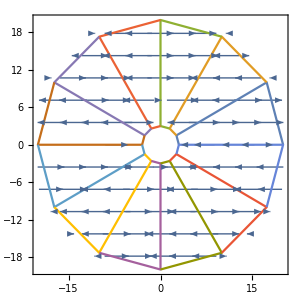

```mathematica
zoff=0;
Mplot=Table[{{x,y},{radFld[stage,"mx",{x,y,zoff}],radFld[stage,"my",{x,y,zoff}]}},{x,-25,25,1},{y,-25,25,1}];
p1=ListVectorPlot[Mplot,AspectRatio->1,ImageSize->300,ColorFunction->"Rainbow",PlotLegends->Automatic];
p2=ListPlot[allpolys,Joined->True];
Show[p1,p2,PlotRange->{{-20,20},{-20,20}}]
```

```mathematica
(* Special options for the Plot[] *)
RadPlot3DOptions[];
(* save the geometry in "dr" *)
dr = radObjDrw[stage];
(* draw the geometry *)
Show[Graphics3D[dr],FrameLabel->{"X","Y","Z"}]
```

-Graphics3D-

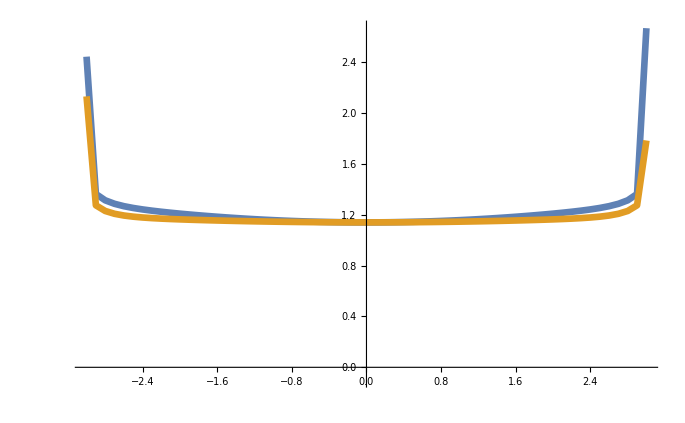

```mathematica
zoffset=10;
xlim=3;
BnormXcut=Table[{x,Sqrt[radFld[stage,"bx",{x,0,zoffset}]^2+radFld[stage,"by",{x,0,zoffset}]^2+radFld[stage,"bz",{x,0,zoffset}]^2]},{x,-xlim,xlim,0.1}];
BnormYcut=Table[{x,Sqrt[radFld[stage,"bx",{0,x,zoffset}]^2+radFld[stage,"by",{0,x,zoffset}]^2+radFld[stage,"bz",{0,x,zoffset}]^2]},{x,-xlim,xlim,0.1}];
ListPlot[{BnormXcut,BnormYcut},Joined->True,PlotStyle->{Thickness[0.007]},PlotRange->{-0.1,All}]
```

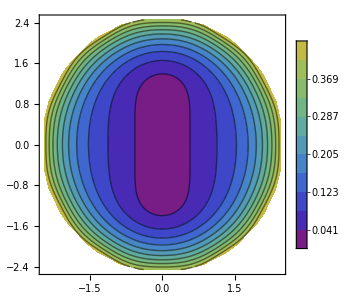

```mathematica
zoff=40;
contourKstage=Table[{x,y,
If[Abs[y]<Sqrt[2.5^2-x^2],Sqrt[radFld[stage,"hx",{x,y,zoff}]^2+radFld[stage,"hy",{x,y,zoff}]^2+radFld[stage,"hz",{x,y,zoff}]^2],Infinity]},{x,-2.5,2.5,0.05},{y,-2.5,2.5,0.05}];
contourKstage=ArrayReshape[contourKstage,{Dimensions[contourKstage][[1]]*Dimensions[contourKstage][[2]],3}];
ListContourPlot[contourKstage,Contours->10,AspectRatio->1,ImageSize->300,ColorFunction->ColorData[{"Rainbow",{0,1.5}}],PlotLegends->Automatic]
```

```mathematica
xlim=2.5;
ylim=2.5;
zmin=0;
zmax=130;

BnormXcut=Table[{x,Sqrt[radFld[stage,"bx",{x,0,0}]^2+radFld[stage,"by",{x,0,0}]^2+radFld[stage,"bz",{x,0,0}]^2]},{x,-xlim,xlim,1}];
BnormYcut=Table[{y,Sqrt[radFld[stage,"bx",{0,y,0}]^2+radFld[stage,"by",{0,y,0}]^2+radFld[stage,"bz",{0,y,0}]^2]},{y,-ylim,ylim,1}];
BnormZcut=Table[{z,Sqrt[radFld[stage,"bx",{0,0,z}]^2+radFld[stage,"by",{0,0,z}]^2+radFld[stage,"bz",{0,0,z}]^2]},{z,zmin,zmax,0.1}];
dnormBdz=Differences[BnormZcut[[;;,2]]]/.{x_,y_}->y/x;
dBtab=Table[{BnormZcut[[i,1]],60dnormBdz[[i]]},{i,1,Length[BnormZcut]-1}];
```

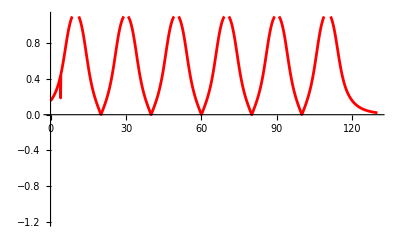

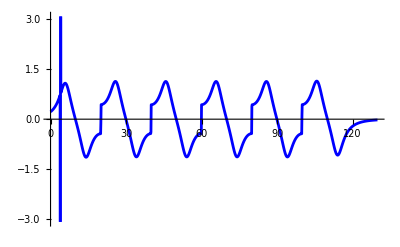

```mathematica
Bplot=ListPlot[BnormZcut,Joined->True,PlotStyle->{Red,Thickness[0.005]},PlotRange->{-1.2,1.1}]
dBplot=ListPlot[dBtab,Joined->True,PlotStyle->{Blue,Thickness[0.005]}]
```

```mathematica
contour2D=Table[{Sqrt[radFld[stage,"bx",{x,0,z}]^2+radFld[stage,"by",{x,0,z}]^2+radFld[stage,"bz",{x,0,z}]^2]},{z,0,130,0.5},{x,-2.5,2.5,0.05}];
```

```mathematica
ListContourPlot[Transpose[contour2D[[;;,;;,1]]],Contours->25,AspectRatio->0.5,ImageSize->600,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics-

```mathematica
(*zoff = 0;*)
din=6;
lensStart=-10;
lensEnd=130;
mxy=50;
mz=250;
bMatrix=Table[radFld[stage,"b",{x, y, z}], {x, -din/2, din/2, din/(mxy-1)}, {y, -din/2, din/2, din/(mxy-1)}, {z, lensStart, lensEnd, Abs[lensStart-lensEnd]/(mz-1)}];
normbMatrix=Table[Sqrt[radFld[stage,"bx",{x, y, z}]^2 + radFld[stage,"by",{x, y, z}]^2 +radFld[stage,"bz",{x, y, z}]^2], {x, -din/2, din/2, din/(mxy-1)}, {y, -din/2, din/2, din/(mxy-1)}, {z, lensStart, lensEnd, Abs[lensStart-lensEnd]/(mz-1)}];
SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/zeeman_sisyphus/b_matrix"];
Export["bMatrix_"<>ToString[m]<>".hdf",bMatrix];
Export["normbMatrix_"<>ToString[m]<>".hdf",normbMatrix];
```

((0.0212538
0.0235643
0.0262776
0.029596
0.0339386
0.040221
0.050468
0.0690254
0.104716
0.174095
0.299758
0.727625
0.685753
0.677763
0.679544
0.681668
0.682108
0.680835
0.678184
0.674472
0.669942
0.66485
0.659799
0.657009
0.664175
0.704027
0.631476
0.619814
0.642457
0.905389
0.850141
0.808264
0.782691
0.768379
0.760896
0.757554
0.757134
0.759644
0.766311
0.779789
0.804429
0.845431
0.901565
0.647929
0.6224
0.62164
0.677713
0.714886
0.703233
0.705797
0.713762
0.723914
0.735202
0.747267
0.759978
0.773323
0.787518
0.803549
0.82506
0.86385
0.946557
0.285864
0.366803
0.478971
0.559306
0.898509
0.838416
0.797935
0.773776
0.760333
0.753591
0.75128
0.752562
0.757894
0.769101
0.789663
0.824848
0.879532
0.947352
0.50649
0.399683
0.297361
0.98288
0.883117
0.835052
0.810434
0.793481
0.779
0.765528
0.752708
0.740503
0.729
0.718467
0.709688
0.70506
0.711581
0.741517
0.624141
0.609613
0.63235
0.911703
0.853619
0.806623
0.776991
0.760118
0.751224
0.747227
0.746582
0.749028
0.755541
0.768505
0.791998
0.831271
0.886931
0.641821
0.617376
0.610889
0.65929
0.721258
0.706019
0.707153
0.71463
0.72458
0.73574
0.74769
0.760279
0.773489
0.787494
0.803112
0.823404
0.858481
0.933127
0.284697
0.351014
0.464608
0.551478
0.90865
0.846337
0.803201
0.777163
0.762533
0.755036
0.752176
0.752933
0.757579
0.767732
0.786616
0.819276
0.871026
0.938153
0.519725
0.416843
0.308379
1.00275
0.894393
0.840627
0.813937
0.796312
0.781578
0.767967
0.755035
0.742715
0.731081
0.720363
0.711229
0.705736
0.709977
0.736191
0.630479
0.607795
0.62791
0.91885
0.861164
0.811624
0.779659
0.761236
0.751388
0.746788
0.745692
0.747667
0.75351
0.765392
0.787145
0.823991
0.877999
0.643379
0.620286
0.608193
0.647757
0.72773
0.708917
0.708504
0.715513
0.725392
0.736638
0.748754
0.761566
0.775044
0.789329
0.805116
0.82499
0.857609
0.925615
0.290744
0.342407
0.457353
0.55097
0.92405
0.860777
0.815768
0.788511
0.773311
0.765605
0.762626
0.763091
0.767
0.775633
0.791807
0.820182
0.866368
0.929455
0.536651
0.436526
0.316628
0.26648
0.94994
0.889891
0.861596
0.84509
0.83278
0.822222
0.812583
0.803509
0.794777
0.786346
0.778813
0.775096
0.785135
0.829872
0.247475
0.138673
0.0826659
0.0564574
0.0438412
0.03688
0.0322748
0.0287594
0.0258499
0.0233387
0.0211321) | (0.0214647
0.0238387
0.0266371
0.0300661
0.0345407
0.0409471
0.0512207
0.0695254
0.104445
0.172487
0.297382
0.723408
0.682379
0.674147
0.675199
0.676649
0.676599
0.675013
0.6722
0.668444
0.663949
0.658861
0.653472
0.649145
0.65219
0.695075
0.625356
0.622174
0.655479
0.905859
0.846132
0.802628
0.776834
0.76272
0.755472
0.752258
0.751807
0.754127
0.760495
0.773697
0.798433
0.840798
0.901093
0.662579
0.626024
0.615744
0.667068
0.702008
0.694918
0.69952
0.70812
0.718465
0.72989
0.74218
0.755276
0.769233
0.784362
0.801795
0.825365
0.866928
0.952292
0.311836
0.387901
0.498651
0.583247
0.89427
0.830907
0.789761
0.76588
0.752902
0.746525
0.744369
0.745566
0.750589
0.761343
0.781527
0.81698
0.873978
0.947525
0.527001
0.419596
0.322515
0.989042
0.887005
0.836063
0.809179
0.790662
0.775134
0.760971
0.74771
0.735241
0.723587
0.712906
0.703693
0.697597
0.700298
0.726121
0.616001
0.61026
0.643789
0.912646
0.849489
0.800411
0.770401
0.753705
0.745083
0.741273
0.740664
0.742983
0.749246
0.761958
0.785503
0.825926
0.88538
0.657967
0.622461
0.606134
0.648672
0.707767
0.697266
0.700726
0.708946
0.719114
0.730405
0.74256
0.755508
0.769292
0.784174
0.801112
0.823351
0.861106
0.938521
0.310454
0.372799
0.484007
0.574679
0.905207
0.839119
0.795076
0.769247
0.75508
0.74797
0.745298
0.746003
0.750368
0.760078
0.778548
0.81132
0.864963
0.937393
0.540814
0.436387
0.332755
1.00908
0.898688
0.842023
0.812959
0.79368
0.777836
0.763491
0.750088
0.737483
0.725686
0.714829
0.705335
0.698596
0.699409
0.721062
0.621432
0.607024
0.637731
0.920618
0.857548
0.805536
0.773037
0.75475
0.745172
0.740776
0.739738
0.741607
0.747211
0.758828
0.78056
0.818322
0.875674
0.660957
0.626913
0.60469
0.637399
0.713583
0.699617
0.701876
0.709773
0.719911
0.73129
0.743598
0.756746
0.770765
0.785884
0.802921
0.824648
0.859863
0.930737
0.316029
0.364899
0.476564
0.573384
0.921748
0.854256
0.808112
0.781019
0.766314
0.759056
0.756334
0.756821
0.760512
0.768739
0.784467
0.812762
0.860304
0.927914
0.557651
0.454577
0.338123
0.289289
0.9536
0.891055
0.860627
0.842607
0.829289
0.818086
0.80807
0.798828
0.790113
0.781857
0.774615
0.7711
0.780704
0.824234
0.237776
0.129632
0.0761134
0.0522588
0.0413392
0.0354231
0.0314163
0.0282451
0.0255357
0.023148
0.0210155) | (0.0216568
0.024088
0.0269631
0.0304916
0.0350852
0.0416036
0.0519008
0.0699662
0.104141
0.170945
0.29595
0.718893
0.678167
0.669621
0.669953
0.670756
0.670248
0.668385
0.665448
0.661693
0.657284
0.652269
0.646638
0.640897
0.639773
0.686816
0.618371
0.624148
0.669508
0.907271
0.842414
0.797296
0.77138
0.757531
0.750556
0.747487
0.747006
0.749122
0.755153
0.768015
0.792752
0.836446
0.901459
0.678598
0.629499
0.609026
0.656596
0.688452
0.686012
0.69255
0.701686
0.712144
0.723637
0.736089
0.749507
0.764012
0.780003
0.798753
0.824284
0.868605
0.957374
0.338576
0.409599
0.519446
0.609451
0.890491
0.823608
0.781905
0.758407
0.745958
0.739981
0.737993
0.739099
0.743785
0.754031
0.773743
0.809344
0.868727
0.948873
0.548944
0.440194
0.348221
0.995028
0.88957
0.83566
0.806605
0.786613
0.770111
0.755322
0.741682
0.72901
0.717271
0.706514
0.696957
0.689498
0.688379
0.710037
0.607038
0.610488
0.656117
0.914753
0.845692
0.794483
0.764193
0.747748
0.739442
0.735841
0.73527
0.737449
0.74343
0.75583
0.779333
0.820844
0.884516
0.675708
0.627564
0.600602
0.637886
0.693551
0.687907
0.693602
0.702467
0.712774
0.724128
0.736427
0.749672
0.763966
0.779656
0.797832
0.821922
0.862306
0.943061
0.337214
0.395163
0.504395
0.600022
0.902337
0.832108
0.787251
0.761742
0.748107
0.741425
0.738956
0.739605
0.743663
0.75288
0.770849
0.803612
0.859157
0.937651
0.56352
0.45667
0.357661
1.01549
0.901731
0.841993
0.810647
0.789805
0.772927
0.757914
0.7441
0.731272
0.719376
0.708452
0.698683
0.690804
0.688222
0.705196
0.611626
0.605724
0.648196
0.92372
0.854321
0.79972
0.766785
0.748712
0.739454
0.735285
0.73431
0.736062
0.741399
0.752697
0.774314
0.812916
0.873912
0.680313
0.633752
0.600481
0.6266
0.698683
0.689702
0.69456
0.703244
0.713559
0.725001
0.73744
0.750861
0.76536
0.781242
0.799449
0.822933
0.860674
0.934827
0.342588
0.387965
0.496666
0.597776
0.920162
0.847959
0.800745
0.773935
0.759795
0.753028
0.750582
0.751091
0.754546
0.762321
0.777525
0.805624
0.854478
0.927203
0.580423
0.47354
0.360485
0.313909
0.955979
0.890653
0.858164
0.838712
0.824445
0.812638
0.802273
0.792882
0.784189
0.776116
0.769153
0.765826
0.775047
0.817981
0.228971
0.120645
0.0695586
0.0481234
0.0389426
0.0340606
0.030628
0.0277815
0.0252569
0.0229783
0.0209138) | (0.0218304
0.0243125
0.0272555
0.0308722
0.0355708
0.0421873
0.0525002
0.0703321
0.103779
0.169419
0.295463
0.714159
0.673278
0.664401
0.664061
0.664267
0.66335
0.66126
0.658249
0.65455
0.65029
0.645426
0.639658
0.632633
0.627184
0.679284
0.610388
0.625678
0.684671
0.909784
0.83904
0.792363
0.766441
0.75293
0.746268
0.743362
0.742852
0.744745
0.750402
0.762856
0.787485
0.83243
0.902777
0.696206
0.632765
0.601387
0.646175
0.674356
0.676822
0.685186
0.694744
0.705221
0.716695
0.729225
0.742882
0.757844
0.774597
0.794542
0.821885
0.868881
0.961841
0.366244
0.431668
0.541183
0.638254
0.887265
0.816619
0.774494
0.75149
0.739636
0.734093
0.732286
0.733293
0.737615
0.747298
0.766442
0.802052
0.863857
0.951715
0.572248
0.461234
0.374478
1.00093
0.890797
0.833889
0.802816
0.781477
0.764106
0.748783
0.734847
0.722055
0.710313
0.699569
0.689772
0.681067
0.676053
0.693085
0.59708
0.610248
0.669399
0.91824
0.842274
0.788928
0.758478
0.742366
0.734421
0.731052
0.730524
0.732548
0.738211
0.750235
0.773592
0.816089
0.884418
0.695344
0.632629
0.59422
0.626737
0.678675
0.67824
0.686078
0.695477
0.705827
0.717159
0.729521
0.74298
0.757696
0.774099
0.793396
0.81919
0.862092
0.946756
0.365212
0.417897
0.525572
0.627766
0.900155
0.825399
0.779853
0.754781
0.74175
0.735531
0.733281
0.73387
0.737598
0.746271
0.763649
0.796268
0.853688
0.939184
0.587839
0.47745
0.383023
1.0221
0.903504
0.840576
0.807097
0.784827
0.767019
0.751432
0.737292
0.72432
0.712409
0.701508
0.691564
0.682661
0.676673
0.688448
0.600856
0.603847
0.659318
0.928429
0.851525
0.794261
0.761011
0.743238
0.73435
0.730435
0.729529
0.731152
0.73619
0.747107
0.768515
0.807839
0.872774
0.701817
0.64075
0.595508
0.615128
0.683019
0.679465
0.686848
0.696208
0.706605
0.718024
0.73051
0.744125
0.759013
0.775561
0.794826
0.819926
0.860055
0.937879
0.370725
0.411427
0.517438
0.624321
0.919445
0.84197
0.793795
0.767384
0.753893
0.747648
0.745501
0.746029
0.749225
0.756514
0.771116
0.798889
0.848975
0.92752
0.605039
0.493178
0.383543
0.340629
0.957032
0.888681
0.854266
0.8335
0.818363
0.806007
0.795336
0.785827
0.777174
0.769279
0.762581
0.759404
0.768232
0.811091
0.221131
0.111733
0.0630141
0.0440817
0.0366759
0.0328048
0.0299205
0.0273702
0.0250126
0.0228367
0.0208319) | (0.0219855
0.0245122
0.0275146
0.0312078
0.0359969
0.0426955
0.0530122
0.0706094
0.103335
0.167844
0.295869
0.709478
0.6681
0.658941
0.658009
0.657694
0.656435
0.654181
0.651161
0.647584
0.643548
0.638922
0.633134
0.624976
0.614974
0.672474
0.601255
0.626699
0.701109
0.913582
0.836071
0.787945
0.762147
0.749049
0.742742
0.740017
0.739478
0.741132
0.746375
0.758349
0.782746
0.828817
0.905167
0.715688
0.635745
0.592726
0.635576
0.660102
0.667904
0.677961
0.687808
0.698188
0.709536
0.722037
0.735822
0.751122
0.768503
0.789482
0.818427
0.867921
0.965874
0.395097
0.453857
0.563619
0.670153
0.884672
0.810053
0.767672
0.745279
0.734086
0.72901
0.727395
0.728298
0.732228
0.741295
0.75977
0.79523
0.859437
0.956461
0.596783
0.482434
0.401306
1.00704
0.89082
0.830987
0.798115
0.775602
0.757501
0.741765
0.727644
0.714836
0.703196
0.692576
0.682662
0.672849
0.663814
0.675131
0.585914
0.609492
0.683686
0.923376
0.839279
0.783855
0.753385
0.737693
0.730158
0.727043
0.726561
0.728417
0.733725
0.745304
0.768398
0.811738
0.885158
0.717299
0.637566
0.586922
0.614894
0.663425
0.668816
0.678687
0.688486
0.698767
0.709971
0.722291
0.735856
0.75088
0.767862
0.788125
0.815423
0.86064
0.949751
0.394833
0.440772
0.547266
0.658292
0.898769
0.819096
0.773023
0.748514
0.736159
0.73044
0.728423
0.728947
0.732322
0.740402
0.757098
0.789421
0.848629
0.942301
0.613743
0.49844
0.40877
1.02926
0.904131
0.837993
0.802605
0.779083
0.760491
0.744451
0.730097
0.717088
0.705266
0.694493
0.684495
0.67471
0.665284
0.670763
0.58884
0.601356
0.671071
0.935107
0.849198
0.78926
0.75584
0.738462
0.729998
0.726363
0.725531
0.727015
0.73172
0.742193
0.763281
0.803179
0.872302
0.726012
0.647824
0.589725
0.602624
0.666756
0.669445
0.679277
0.689176
0.699539
0.710828
0.723258
0.736956
0.752123
0.769209
0.78938
0.815898
0.858201
0.940011
0.40096
0.435094
0.538597
0.653254
0.919756
0.836394
0.787392
0.761519
0.748743
0.743071
0.741235
0.741785
0.744708
0.75146
0.76538
0.792695
0.843885
0.929093
0.631585
0.513203
0.407132
0.37004
0.956834
0.885324
0.849181
0.82725
0.811353
0.79853
0.787604
0.778014
0.769422
0.761711
0.755259
0.752174
0.760539
0.803674
0.214311
0.102915
0.0565066
0.0401603
0.0345611
0.0316729
0.0292903
0.0270116
0.0248078
0.0227153
0.020762) | (0.0221225
0.0246875
0.0277406
0.0314986
0.0363629
0.043126
0.053431
0.0707858
0.102785
0.166146
0.297003
0.705446
0.663363
0.654028
0.652617
0.651875
0.650357
0.648018
0.645065
0.641689
0.637961
0.633675
0.628003
0.618909
0.604142
0.666297
0.590814
0.627149
0.718956
0.918866
0.833568
0.784165
0.758635
0.746032
0.740121
0.737597
0.737029
0.738426
0.743214
0.754631
0.77866
0.825672
0.908727
0.737414
0.638344
0.582971
0.624364
0.646488
0.660166
0.671733
0.681705
0.691847
0.702936
0.715276
0.72905
0.744539
0.762375
0.784179
0.814454
0.866147
0.96988
0.425468
0.475871
0.586405
0.705912
0.882758
0.804029
0.761593
0.739931
0.729465
0.724889
0.723478
0.72427
0.727784
0.736178
0.753884
0.789013
0.855518
0.963646
0.622314
0.503468
0.428706
1.01392
0.890012
0.827471
0.793092
0.769627
0.750976
0.73498
0.720813
0.708121
0.696712
0.686349
0.676469
0.665729
0.652566
0.656126
0.573293
0.608185
0.69897
0.930491
0.836742
0.77938
0.749052
0.733871
0.726797
0.72396
0.723529
0.7252
0.730117
0.741179
0.763881
0.80787
0.886775
0.742183
0.64225
0.578682
0.601793
0.648468
0.660545
0.672287
0.682322
0.692395
0.703341
0.715488
0.729024
0.744208
0.761607
0.782634
0.811175
0.858397
0.952405
0.426632
0.463521
0.569117
0.692153
0.898247
0.813307
0.766913
0.743099
0.731488
0.726309
0.724538
0.724994
0.727993
0.73543
0.751351
0.783211
0.844048
0.94737
0.641123
0.5193
0.434797
1.03761
0.903963
0.834747
0.79775
0.773209
0.754016
0.737679
0.723252
0.710339
0.698733
0.688221
0.678319
0.667826
0.654972
0.652239
0.575214
0.598239
0.683353
0.944252
0.847359
0.784827
0.751414
0.734529
0.726543
0.723216
0.722466
0.723796
0.728134
0.738098
0.758749
0.79903
0.872515
0.753714
0.654826
0.58313
0.588518
0.650393
0.660564
0.672708
0.682976
0.693161
0.704193
0.716432
0.730083
0.74538
0.762842
0.783724
0.811411
0.855572
0.941558
0.434086
0.458731
0.559784
0.684885
0.921221
0.83131
0.78169
0.756491
0.744507
0.739447
0.737939
0.738507
0.741139
0.747326
0.760487
0.787194
0.839303
0.932151
0.660116
0.533261
0.431061
0.403136
0.955685
0.881028
0.843436
0.820539
0.804013
0.790822
0.779722
0.770098
0.761603
0.754086
0.747855
0.744802
0.75256
0.796096
0.208488
0.0942127
0.0500578
0.0364101
0.032629
0.0306692
0.0287488
0.0267082
0.0246327
0.0226197
0.02071) | (0.0222417
0.0248387
0.0279338
0.0317447
0.0366686
0.0434772
0.0537517
0.0708508
0.102108
0.16424
0.298513
0.703214
0.660294
0.650927
0.649163
0.648098
0.646417
0.64408
0.641281
0.638195
0.634871
0.631037
0.625643
0.615887
0.596369
0.660484
0.578948
0.626973
0.738245
0.925803
0.831578
0.781143
0.756039
0.744014
0.738545
0.736241
0.735645
0.736766
0.741056
0.751835
0.775346
0.823052
0.913481
0.761808
0.640441
0.572113
0.611705
0.635003
0.655005
0.667803
0.677695
0.687432
0.698104
0.710123
0.723717
0.73921
0.757291
0.779663
0.810929
0.864381
0.974618
0.457713
0.497374
0.609047
0.746778
0.881496
0.798658
0.756403
0.735599
0.725925
0.721883
0.720687
0.721361
0.724433
0.732101
0.748932
0.783531
0.852114
0.97399
0.648409
0.523968
0.456581
1.02265
0.889119
0.824275
0.788761
0.764618
0.745634
0.729567
0.715524
0.703108
0.692085
0.682138
0.672478
0.661062
0.643827
0.636203
0.558981
0.606318
0.715085
0.939967
0.834675
0.775614
0.745608
0.731036
0.724478
0.721943
0.721567
0.723039
0.727523
0.737994
0.760164
0.804558
0.889229
0.770878
0.646499
0.569538
0.586451
0.635157
0.654842
0.668183
0.678247
0.687944
0.698476
0.710293
0.723635
0.738802
0.756411
0.777957
0.807418
0.856211
0.955396
0.461352
0.48582
0.59065
0.730192
0.898575
0.808131
0.761667
0.738686
0.727894
0.723287
0.721777
0.722162
0.724762
0.731509
0.746557
0.777771
0.839983
0.954795
0.669692
0.539641
0.460898
1.04838
0.903706
0.831754
0.793537
0.768259
0.748691
0.732249
0.71792
0.705263
0.69403
0.68394
0.674307
0.663346
0.647239
0.633313
0.559543
0.594522
0.695897
0.956545
0.845995
0.781067
0.747854
0.731575
0.724123
0.72113
0.720473
0.721638
0.725571
0.734959
0.755041
0.795473
0.873354
0.786223
0.661516
0.575781
0.571924
0.635047
0.654249
0.668449
0.678871
0.688708
0.699324
0.711221
0.724654
0.739906
0.757543
0.778898
0.807441
0.853034
0.943171
0.471312
0.482036
0.580553
0.719587
0.923886
0.826811
0.776824
0.752448
0.741337
0.736929
0.735764
0.736352
0.738683
0.744251
0.756577
0.782519
0.8353
0.936888
0.69059
0.55294
0.455064
0.441565
0.954208
0.876667
0.837979
0.814356
0.797375
0.78394
0.772753
0.763169
0.754816
0.747508
0.741486
0.738403
0.745385
0.789173
0.203504
0.0856862
0.0437075
0.0328725
0.0309072
0.0298105
0.0283001
0.0264584
0.0245
0.0225445
0.0206707) | (0.0223434
0.0249663
0.0280948
0.0319467
0.0369139
0.0437482
0.0539705
0.0707955
0.101287
0.162046
0.299733
0.70491
0.660836
0.651567
0.649561
0.648275
0.646523
0.644278
0.641721
0.639014
0.636191
0.632931
0.628008
0.617984
0.594299
0.654383
0.565651
0.626139
0.758679
0.934415
0.830112
0.77897
0.75446
0.7431
0.738118
0.736054
0.735431
0.736256
0.740003
0.75006
0.772894
0.820981
0.919262
0.789227
0.641905
0.560268
0.595944
0.628232
0.654468
0.668073
0.677631
0.68677
0.696848
0.708364
0.721586
0.736868
0.754949
0.777591
0.809446
0.864063
0.981368
0.492026
0.517987
0.630862
0.794951
0.88074
0.794023
0.752215
0.732398
0.723584
0.720107
0.719138
0.719688
0.722293
0.72918
0.74503
0.778883
0.849177
0.988455
0.674283
0.543535
0.484597
1.0352
0.889482
0.822966
0.78676
0.762257
0.743198
0.727279
0.713555
0.701598
0.691135
0.681787
0.672571
0.660831
0.639988
0.61592
0.542844
0.603916
0.731497
0.952149
0.833045
0.772639
0.743151
0.729294
0.723304
0.721102
0.720784
0.72204
0.72605
0.735847
0.757339
0.801849
0.892317
0.804687
0.650076
0.559641
0.567151
0.626049
0.653793
0.668289
0.678115
0.687246
0.697187
0.708499
0.721456
0.736396
0.753977
0.775755
0.805758
0.855558
0.95989
0.499836
0.507287
0.611267
0.773703
0.899573
0.80364
0.757398
0.73539
0.725489
0.721492
0.720258
0.720566
0.722746
0.728754
0.742835
0.773207
0.836428
0.964931
0.698764
0.559036
0.486683
1.06393
0.904634
0.830561
0.791596
0.765916
0.746236
0.72991
0.715879
0.703659
0.692976
0.683485
0.674338
0.663235
0.644372
0.615188
0.541411
0.590287
0.708138
0.972934
0.845031
0.778058
0.745264
0.729698
0.722845
0.720219
0.719658
0.720641
0.724135
0.732871
0.752252
0.792574
0.874653
0.825768
0.667534
0.567821
0.551507
0.62307
0.652646
0.668423
0.67872
0.688009
0.698029
0.709404
0.722435
0.737435
0.755011
0.776552
0.805596
0.852087
0.945995
0.514425
0.50462
0.600382
0.757688
0.927601
0.822943
0.772909
0.749512
0.739348
0.73562
0.734821
0.735434
0.737439
0.74236
0.753773
0.778795
0.831918
0.943332
0.722617
0.57178
0.478753
0.488129
0.953592
0.873733
0.834398
0.810334
0.793093
0.779566
0.768411
0.758955
0.750791
0.74374
0.737942
0.734784
0.740836
0.784526
0.198966
0.0774072
0.0374959
0.029626
0.0294313
0.0291025
0.027936
0.0262711
0.0243974
0.0224943
0.0206527) | (0.022428
0.0250708
0.0282241
0.0321049
0.0370993
0.0439382
0.0540847
0.0706129
0.100307
0.159499
0.299521
0.714394
0.667905
0.658764
0.656566
0.655123
0.653372
0.651291
0.649047
0.646792
0.644552
0.641983
0.637751
0.627993
0.601733
0.646381
0.551139
0.62466
0.779013
0.944264
0.829104
0.777647
0.753903
0.743297
0.738851
0.737048
0.736398
0.736907
0.740065
0.749311
0.771305
0.819409
0.925512
0.819374
0.64262
0.547743
0.573554
0.630298
0.661415
0.675214
0.684139
0.69248
0.701788
0.71262
0.725271
0.740119
0.757937
0.780524
0.812533
0.867587
0.992099
0.527899
0.53731
0.650983
0.854892
0.88016
0.79013
0.749052
0.730352
0.722461
0.719582
0.718851
0.719272
0.721383
0.727436
0.742201
0.775086
0.846566
1.0082
0.698598
0.561772
0.511984
1.05516
0.893373
0.826052
0.789644
0.765129
0.746268
0.730728
0.717529
0.706211
0.696486
0.687924
0.679405
0.667817
0.644518
0.597032
0.525038
0.601062
0.746922
0.967006
0.831737
0.770453
0.741689
0.72865
0.723289
0.721443
0.72119
0.722213
0.725705
0.734747
0.755409
0.799709
0.895572
0.845465
0.652712
0.549282
0.540923
0.625627
0.660326
0.675295
0.684567
0.69292
0.702095
0.71272
0.725103
0.739596
0.756895
0.778592
0.808723
0.85887
0.967749
0.54253
0.527488
0.630274
0.824641
0.900793
0.799826
0.754128
0.733236
0.724299
0.720946
0.719998
0.720231
0.721968
0.727185
0.740204
0.769541
0.833295
0.97771
0.726837
0.577059
0.511478
1.08911
0.908932
0.833669
0.794479
0.768753
0.749242
0.733275
0.719745
0.70815
0.698192
0.689482
0.681062
0.670239
0.649635
0.601156
0.520676
0.585688
0.719039
0.994608
0.844295
0.775791
0.743646
0.728912
0.72272
0.72049
0.720032
0.720825
0.723836
0.731842
0.750386
0.790306
0.876051
0.876776
0.672411
0.559515
0.525522
0.619152
0.658757
0.675343
0.685165
0.693691
0.702935
0.713601
0.726038
0.74057
0.757838
0.779267
0.8084
0.855184
0.951975
0.5659
0.525995
0.618707
0.798921
0.93181
0.819683
0.769968
0.747691
0.738561
0.73555
0.735132
0.735767
0.737437
0.741677
0.752097
0.776036
0.82911
0.951029
0.754857
0.589307
0.501568
0.548058
0.955914
0.874721
0.835246
0.811039
0.793766
0.780318
0.769317
0.760095
0.75221
0.745465
0.739922
0.736756
0.741819
0.785314
0.194104
0.0695043
0.0315259
0.0267515
0.0282308
0.0285571
0.0276749
0.0261421
0.024334
0.022466
0.0206437) | (0.0224959
0.0251526
0.0283224
0.0322202
0.0372252
0.0440471
0.0540922
0.0702975
0.0991592
0.156562
0.296224
0.738037
0.685546
0.676344
0.673869
0.672251
0.670511
0.668614
0.666702
0.664919
0.663295
0.661494
0.658176
0.649351
0.623306
0.631287
0.535957
0.622624
0.79574
0.953825
0.828323
0.776981
0.754166
0.7444
0.740533
0.739011
0.738334
0.738509
0.741033
0.749387
0.770384
0.818121
0.931012
0.848881
0.642535
0.535066
0.53632
0.646785
0.679517
0.692713
0.700694
0.708075
0.716487
0.726506
0.738434
0.752665
0.769992
0.792234
0.823988
0.87871
1.00936
0.562927
0.554965
0.668462
0.938162
0.879206
0.786812
0.746742
0.729274
0.722364
0.720109
0.719624
0.719912
0.72151
0.726682
0.740268
0.771978
0.843987
1.03336
0.719368
0.578328
0.537375
1.08892
0.904443
0.837342
0.801196
0.776982
0.758564
0.743598
0.731081
0.720541
0.711675
0.704044
0.696474
0.685623
0.661854
0.585841
0.506226
0.597906
0.758874
0.982882
0.830481
0.768865
0.741021
0.728901
0.724223
0.72276
0.722574
0.723348
0.726282
0.734494
0.754182
0.797938
0.898142
0.894583
0.65419
0.538907
0.503339
0.640602
0.678199
0.692719
0.701086
0.708487
0.716767
0.72658
0.738238
0.752108
0.768906
0.790243
0.820119
0.86993
0.981746
0.587425
0.545988
0.646985
0.884801
0.90142
0.796518
0.751685
0.732041
0.724127
0.721451
0.7208
0.720954
0.722228
0.726612
0.738486
0.766606
0.830356
0.991387
0.751048
0.593336
0.534318
1.13599
0.920136
0.844881
0.805971
0.780528
0.761436
0.746029
0.733168
0.722329
0.713225
0.705438
0.697966
0.687938
0.667189
0.601093
0.497899
0.580941
0.72706
1.02187
0.843463
0.774081
0.742806
0.72901
0.72353
0.721735
0.721387
0.721976
0.724463
0.731676
0.749246
0.788479
0.876964
0.950471
0.675655
0.551216
0.49259
0.631617
0.676445
0.692751
0.70169
0.709268
0.717597
0.727438
0.739127
0.75301
0.769754
0.790794
0.819661
0.866119
0.964172
0.627448
0.545619
0.635
0.839997
0.935316
0.816844
0.767817
0.746823
0.738773
0.736531
0.736498
0.737145
0.738481
0.741996
0.751356
0.774081
0.826679
0.95844
0.783549
0.605099
0.522808
0.632593
0.964663
0.883531
0.84439
0.820344
0.803264
0.790061
0.779354
0.770474
0.76295
0.756608
0.751442
0.748387
0.752643
0.797308
0.18773
0.062133
0.0258721
0.024377
0.0273331
0.0281769
0.0275029
0.0260666
0.0243082
0.0224662
0.0206506) | (0.0225476
0.0252125
0.0283903
0.0322934
0.0372925
0.0440753
0.0539918
0.0698455
0.0978392
0.153241
0.288256
0.781992
0.718459
0.708662
0.705598
0.703638
0.701803
0.700003
0.698341
0.696946
0.695864
0.694817
0.692582
0.685412
0.663016
0.575771
0.520966
0.620219
0.80213
0.959931
0.827209
0.776384
0.754628
0.745764
0.742509
0.741282
0.740579
0.740408
0.74227
0.749672
0.769552
0.816575
0.933865
0.864225
0.64173
0.522936
0.468484
0.682995
0.712619
0.724333
0.731132
0.737519
0.745056
0.754283
0.765487
0.779062
0.79582
0.817583
0.848855
0.902641
1.03537
0.591607
0.570656
0.682545
1.0974
0.877091
0.783568
0.744722
0.72856
0.722664
0.721046
0.720811
0.720963
0.722038
0.726305
0.738652
0.769036
0.840897
1.0546
0.734462
0.592954
0.559033
1.13955
0.92787
0.861944
0.82634
0.802582
0.7847
0.770359
0.758539
0.748762
0.740736
0.734051
0.727587
0.718089
0.696357
0.627998
0.487673
0.594673
0.76407
0.993797
0.828722
0.767312
0.740543
0.729417
0.725459
0.724396
0.724281
0.724793
0.727141
0.734467
0.753071
0.795999
0.898843
0.936007
0.65446
0.529058
0.452544
0.677705
0.711347
0.724364
0.731529
0.737923
0.745324
0.754343
0.765277
0.778485
0.794707
0.81556
0.84497
0.893954
1.0056
0.624862
0.562423
0.660895
0.939183
0.900333
0.793219
0.749519
0.731201
0.724348
0.722362
0.722015
0.722083
0.722891
0.726422
0.7371
0.763867
0.827094
0.999875
0.767441
0.607604
0.554146
1.25415
0.943334
0.869344
0.831021
0.806036
0.787467
0.772666
0.760501
0.750417
0.742135
0.735273
0.728881
0.720162
0.70122
0.646679
0.474779
0.576335
0.730666
1.04593
0.841931
0.772365
0.742124
0.72936
0.724648
0.723299
0.723066
0.723438
0.725386
0.731748
0.748252
0.78655
0.876542
1.097
0.677011
0.54336
0.454514
0.670372
0.709718
0.724454
0.732165
0.738711
0.746139
0.755172
0.76612
0.779312
0.795452
0.815991
0.844384
0.890082
0.987114
0.686668
0.563014
0.648891
0.867038
0.9363
0.813932
0.765921
0.746284
0.739376
0.737905
0.73825
0.738934
0.739906
0.74269
0.750955
0.772355
0.824127
0.962429
0.801267
0.618862
0.541773
0.760965
0.985057
0.905607
0.867142
0.843438
0.826658
0.813808
0.803489
0.795003
0.787921
0.782054
0.777406
0.774779
0.778792
0.827914
0.17877
0.0555665
0.0207926
0.0226117
0.0267444
0.0279561
0.02742
0.0260374
0.0243175
0.0224711
0.0206714) | (0.0225837
0.025251
0.0284289
0.0323256
0.0373023
0.0440235
0.0537832
0.0692544
0.0963461
0.149585
0.275579
1.12624
1.14194
1.17508
1.19859
1.21638
1.23156
1.24593
1.26042
1.27544
1.29083
1.30567
1.31743
1.32028
1.30221
0.408573
0.507148
0.617738
0.793906
1.36817
1.27247
1.24473
1.2373
1.237
1.23848
1.23927
1.23837
1.23576
1.2324
1.23067
1.23558
1.25894
1.33974
0.847683
0.640465
0.51207
0.387685
1.25001
1.26772
1.25995
1.24067
1.21668
1.19086
1.16431
1.13724
1.10944
1.08042
1.04955
1.01675
0.986788
1.00768
0.608358
0.584219
0.693031
0.956832
1.28699
1.2299
1.21409
1.21205
1.21446
1.21727
1.21863
1.21793
1.2155
1.21276
1.21297
1.22333
1.26323
1.41601
0.743016
0.605539
0.575758
1.07288
0.97965
1.00481
1.03753
1.06876
1.09796
1.12574
1.15263
1.17896
1.20463
1.22888
1.24949
1.26109
1.25185
1.27444
0.470907
0.591652
0.761213
1.38252
1.26193
1.22769
1.21825
1.21777
1.21996
1.22188
1.22227
1.2209
1.21858
1.21739
1.22185
1.24226
1.31045
0.892346
0.653771
0.520276
0.402003
1.23781
1.26045
1.2558
1.23809
1.21498
1.18973
1.16362
1.13696
1.10959
1.08106
1.05072
1.01836
0.98734
0.991179
0.639906
0.576582
0.671881
0.906748
1.304
1.23561
1.21645
1.21322
1.21531
1.21818
1.21977
1.21932
1.21704
1.21415
1.21358
1.22171
1.25502
1.37752
0.773872
0.619773
0.570291
1.1427
0.978267
0.999502
1.03212
1.06364
1.0931
1.12104
1.14803
1.17442
1.20021
1.22474
1.24609
1.25949
1.25424
1.23518
0.453761
0.572188
0.729598
1.42024
1.27013
1.22949
1.21782
1.2165
1.2185
1.22052
1.22112
1.21994
1.21763
1.21607
1.21929
1.23638
1.29365
0.938448
0.676668
0.536385
0.418841
1.23044
1.25671
1.25481
1.23817
1.21535
1.19006
1.16379
1.13696
1.10946
1.08086
1.05058
1.0183
0.98647
0.979366
0.695559
0.577882
0.660287
0.860089
1.33352
1.25211
1.22996
1.22632
1.22901
1.23296
1.23583
1.23671
1.23558
1.23342
1.23266
1.23866
1.26505
1.36143
0.80236
0.630532
0.557974
0.74702
0.911059
0.920029
0.944911
0.968098
0.987825
1.00443
1.01828
1.02956
1.03805
1.04299
1.04271
1.034
1.01218
1.0005
0.167406
0.0501012
0.0166536
0.0215535
0.0264858
0.0279041
0.0274378
0.0260698
0.0243349
0.0225195
0.0207122) | (0.0226048
0.025269
0.0284389
0.0323179
0.0372559
0.0438928
0.0534666
0.0685228
0.094682
0.145674
0.260519
1.11616
1.11519
1.14483
1.16752
1.18514
1.20038
1.2149
1.22961
1.24491
1.26067
1.27605
1.28875
1.29372
1.28391
0.357304
0.495281
0.615551
0.778298
1.35846
1.26417
1.2375
1.23104
1.23146
1.2334
1.23441
1.23349
1.23064
1.2268
1.22434
1.22827
1.25052
1.33033
0.817611
0.639168
0.503017
0.34754
1.23416
1.24114
1.23094
1.21058
1.18591
1.15958
1.13257
1.10508
1.07689
1.04754
1.01652
0.984197
0.956928
0.98634
0.614797
0.595642
0.700457
0.856143
1.27663
1.22071
1.2062
1.20521
1.20836
1.21161
1.21315
1.21235
1.20956
1.20617
1.20542
1.21454
1.25317
1.3922
0.746528
0.616122
0.587818
1.03208
0.95161
0.972611
1.00451
1.03577
1.06527
1.09342
1.12073
1.1475
1.17367
1.19853
1.22004
1.23348
1.23057
1.27212
0.457036
0.589161
0.753595
1.36917
1.25297
1.21979
1.21138
1.21169
1.21441
1.21662
1.21705
1.2155
1.21275
1.21089
1.21441
1.23372
1.30108
0.831237
0.652664
0.512996
0.369
1.22625
1.23445
1.22695
1.20807
1.18425
1.15847
1.1319
1.10481
1.07705
1.04817
1.01766
0.985615
0.956756
0.969189
0.636978
0.588441
0.680288
0.850276
1.29346
1.22626
1.20841
1.20628
1.20914
1.2125
1.21431
1.2138
1.21119
1.2077
1.20621
1.21312
1.24514
1.36241
0.773166
0.629917
0.582848
1.05811
0.951484
0.967576
0.999124
1.03062
1.06035
1.08866
1.11606
1.14289
1.16917
1.19429
1.21647
1.23149
1.23129
1.2463
0.436656
0.568801
0.725678
1.39873
1.26104
1.22141
1.21078
1.2103
1.21285
1.2152
1.21587
1.21456
1.21186
1.20965
1.21199
1.22797
1.28437
0.836425
0.675389
0.530647
0.392537
1.22509
1.23147
1.22621
1.20826
1.18469
1.15885
1.13212
1.10485
1.07695
1.048
1.0175
0.985423
0.955337
0.955723
0.670094
0.590198
0.669418
0.835828
1.32287
1.24286
1.22202
1.21954
1.22307
1.22756
1.23071
1.23161
1.23023
1.22756
1.22594
1.2308
1.2559
1.35029
0.793263
0.640215
0.571379
0.673013
0.883786
0.886581
0.910182
0.933236
0.953151
0.970006
0.984061
0.995544
1.00419
1.0093
1.0093
1.00137
0.982756
0.988421
0.155733
0.0460792
0.0141338
0.0212954
0.0265457
0.0279885
0.0275176
0.0261501
0.024414
0.0225649
0.0207539) | (0.0226113
0.0252672
0.0284216
0.0322716
0.0371549
0.0436848
0.0530429
0.0676504
0.0928507
0.141602
0.246159
1.0852
1.06904
1.09442
1.11586
1.13308
1.14823
1.16282
1.1777
1.19326
1.20943
1.22544
1.23927
1.24677
1.24576
0.334046
0.485753
0.614051
0.765442
1.3438
1.25151
1.22584
1.22024
1.22129
1.22364
1.22484
1.22392
1.22085
1.2166
1.21349
1.21657
1.23781
1.3161
0.796515
0.638347
0.496068
0.327812
1.19881
1.19466
1.18161
1.15999
1.1346
1.10777
1.0804
1.05266
1.02432
0.994997
0.964377
0.933396
0.910362
0.950079
0.617818
0.605041
0.705871
0.820034
1.2622
1.20753
1.19412
1.19401
1.19778
1.20141
1.20309
1.20222
1.19911
1.19518
1.19362
1.2017
1.23916
1.37057
0.747895
0.624862
0.59665
0.989289
0.907476
0.922531
0.95257
0.983254
1.01265
1.04091
1.06845
1.09554
1.12216
1.14766
1.17023
1.18583
1.18987
1.25224
0.44639
0.587523
0.74635
1.35201
1.23973
1.20756
1.20004
1.20104
1.20423
1.20669
1.20716
1.20545
1.20233
1.19987
1.20258
1.22092
1.28708
0.799744
0.651851
0.507495
0.349025
1.19479
1.18865
1.17785
1.15758
1.13298
1.10669
1.07975
1.0524
1.02447
0.995577
0.965383
0.934485
0.909208
0.932032
0.632818
0.598135
0.686794
0.821186
1.27875
1.21295
1.19621
1.19499
1.19852
1.20228
1.20426
1.20371
1.20083
1.19682
1.19456
1.20047
1.23132
1.34427
0.770686
0.638261
0.592517
1.00859
0.908917
0.917982
0.947341
0.978139
1.00772
1.03612
1.06374
1.09088
1.11757
1.1433
1.16645
1.18339
1.18883
1.22841
0.423738
0.566469
0.721695
1.37824
1.24763
1.20902
1.19932
1.19955
1.20261
1.20523
1.20598
1.20452
1.20149
1.1987
1.20025
1.21528
1.27061
0.799089
0.674214
0.526395
0.374599
1.19853
1.18656
1.1774
1.15792
1.1335
1.10714
1.08001
1.05246
1.02437
0.9954
0.965157
0.934076
0.907024
0.916894
0.654031
0.600175
0.676733
0.818127
1.30789
1.22963
1.20996
1.20842
1.21264
1.21762
1.221
1.22188
1.22029
1.21715
1.21485
1.21875
1.24268
1.33482
0.784678
0.648239
0.582239
0.645024
0.841611
0.836036
0.857042
0.879274
0.898919
0.915703
0.929845
0.941411
0.950196
0.955549
0.956002
0.949252
0.934672
0.95668
0.146484
0.0437681
0.0139853
0.0218101
0.0269061
0.0282364
0.0276965
0.0262681
0.0244968
0.0226374
0.0208054) | (0.0226041
0.0252465
0.0283781
0.0321884
0.037001
0.0434015
0.0525136
0.0666375
0.0908555
0.137449
0.234389
1.04277
1.01175
1.03264
1.05256
1.06919
1.08414
1.09871
1.11371
1.12951
1.14607
1.16276
1.17784
1.188
1.19515
0.310008
0.478657
0.613586
0.759226
1.32754
1.23656
1.21181
1.20695
1.20854
1.21123
1.21261
1.21168
1.20843
1.20383
1.20019
1.20255
1.2229
1.29985
0.787191
0.63848
0.491318
0.310381
1.15082
1.13677
1.12075
1.09779
1.07167
1.04443
1.01683
0.988996
0.960749
0.931784
0.902046
0.873128
0.855322
0.90721
0.621772
0.612589
0.710386
0.807901
1.24597
1.19246
1.17993
1.18051
1.18478
1.18871
1.19051
1.18957
1.18622
1.18185
1.17965
1.1869
1.22333
1.35364
0.749579
0.631981
0.603619
0.949343
0.85514
0.863257
0.890634
0.920197
0.949124
0.977231
1.00481
1.03209
1.05906
1.08518
1.10885
1.12675
1.13742
1.2222
0.438778
0.587014
0.742642
1.33519
1.22433
1.19308
1.18632
1.1879
1.19147
1.19415
1.19466
1.19282
1.18938
1.18642
1.18846
1.20594
1.27091
0.787517
0.651995
0.503903
0.333534
1.14978
1.13146
1.11724
1.09549
1.07011
1.04337
1.01617
0.988713
0.960847
0.932272
0.902861
0.873785
0.853054
0.887268
0.634066
0.605863
0.692169
0.810639
1.26229
1.19776
1.18192
1.18142
1.18547
1.18957
1.19169
1.1911
1.18799
1.18358
1.18071
1.18581
1.21567
1.3271
0.770089
0.645089
0.600066
0.970616
0.85825
0.859339
0.88566
0.915196
0.944244
0.972454
1.00008
1.02739
1.05442
1.08072
1.10488
1.12385
1.13481
1.19499
0.414386
0.565407
0.719782
1.36167
1.23206
1.19442
1.18549
1.18632
1.18979
1.19266
1.19347
1.1919
1.18857
1.18532
1.18621
1.20042
1.25465
0.785709
0.674092
0.523816
0.361307
1.15717
1.13023
1.11712
1.096
1.07074
1.04388
1.01649
0.98881
0.960769
0.932055
0.902526
0.873075
0.850049
0.870233
0.652069
0.608074
0.682768
0.810975
1.29135
1.21452
1.19578
1.19499
1.1998
1.20514
1.20869
1.20958
1.20782
1.20432
1.20145
1.20457
1.22753
1.31828
0.781267
0.654958
0.590985
0.643125
0.791973
0.776958
0.794459
0.815203
0.83416
0.850664
0.86466
0.876215
0.885102
0.890703
0.891754
0.886405
0.876088
0.91365
0.1411
0.0432517
0.0160084
0.0229715
0.0275358
0.0286174
0.0279277
0.0264351
0.0246154
0.0227319
0.0208886) | (0.0225838
0.025208
0.0283096
0.0320698
0.0367965
0.0430451
0.0518807
0.065485
0.0886987
0.133265
0.225614
0.998238
0.953537
0.970356
0.988744
1.00473
1.01941
1.03392
1.04899
1.06499
1.08194
1.09928
1.11559
1.12831
1.14222
0.284939
0.473988
0.614418
0.759661
1.31257
1.22215
1.19833
1.19413
1.19619
1.19918
1.2007
1.19977
1.19638
1.19147
1.18738
1.1891
1.2086
1.28454
0.787349
0.639928
0.488784
0.293254
1.10005
1.07816
1.05934
1.03509
1.0083
0.980717
0.952986
0.925207
0.897221
0.868832
0.840238
0.813661
0.801102
0.865459
0.62715
0.618454
0.714837
0.809127
1.23068
1.17827
1.1665
1.16765
1.17232
1.1765
1.17839
1.1774
1.17385
1.16912
1.16641
1.17295
1.2084
1.34154
0.752865
0.637699
0.609303
0.914814
0.803455
0.804852
0.829312
0.857479
0.885702
0.913474
0.940944
0.968302
0.995546
1.02221
1.04695
1.06705
1.08335
1.18934
0.43399
0.587839
0.743397
1.32099
1.20955
1.17923
1.17315
1.17523
1.17914
1.18199
1.18254
1.18057
1.17687
1.17349
1.17492
1.19161
1.25548
0.787625
0.653579
0.502285
0.32027
1.10112
1.07347
1.05608
1.0329
1.00679
0.979677
0.95232
0.924889
0.897249
0.869196
0.840827
0.813859
0.797786
0.842958
0.639772
0.611799
0.697047
0.811904
1.24689
1.18345
1.16841
1.16851
1.17298
1.17734
1.17958
1.17896
1.17568
1.17093
1.16757
1.17199
1.20092
1.31297
0.772669
0.650686
0.605907
0.940822
0.808105
0.801582
0.824639
0.852629
0.880899
0.908729
0.936226
0.963585
0.990853
1.01765
1.04278
1.06372
1.0795
1.15671
0.408142
0.565773
0.720927
1.34946
1.2171
1.18044
1.17221
1.17357
1.1774
1.18047
1.18133
1.17966
1.17609
1.17244
1.17276
1.1862
1.23934
0.78588
0.675684
0.523001
0.351082
1.11117
1.07301
1.05628
1.03358
1.00753
0.98026
0.952671
0.925005
0.897162
0.868942
0.840377
0.812855
0.794002
0.823943
0.65892
0.614108
0.688006
0.812475
1.2761
1.20025
1.18236
1.18221
1.18746
1.19308
1.1968
1.19769
1.19578
1.192
1.18866
1.19112
1.21319
1.30341
0.78349
0.660718
0.597837
0.654344
0.743152
0.719203
0.732876
0.751845
0.769918
0.785906
0.799663
0.811128
0.82006
0.82589
0.82753
0.823583
0.817129
0.868505
0.139459
0.0443738
0.0194566
0.0246455
0.0283867
0.0290959
0.0282332
0.0266291
0.024764
0.0228294
0.0209572) | (0.0225511
0.0251527
0.0282177
0.0319177
0.0365435
0.0426185
0.0511469
0.0641944
0.0863806
0.129063
0.21936
0.956326
0.900319
0.913983
0.931056
0.946435
0.960845
0.975265
0.990372
1.00654
1.0238
1.04175
1.05917
1.07413
1.09305
0.261835
0.471773
0.616695
0.765838
1.30033
1.21006
1.18723
1.18369
1.18619
1.18947
1.19112
1.19019
1.18666
1.18148
1.17695
1.17806
1.19665
1.2718
0.794931
0.642899
0.488483
0.278432
1.05254
1.02514
1.00393
0.978518
0.951168
0.923334
0.895569
0.867945
0.840328
0.812617
0.785226
0.760853
0.752698
0.828132
0.632788
0.62275
0.719693
0.819477
1.21799
1.16668
1.15566
1.15733
1.16234
1.16673
1.1687
1.16767
1.16395
1.15891
1.15573
1.16161
1.19602
1.33397
0.758144
0.642185
0.613607
0.8863
0.757077
0.752986
0.774787
0.801532
0.828955
0.856283
0.883542
0.910878
0.938299
0.965423
0.991098
1.01312
1.03372
1.15798
0.432001
0.590127
0.748474
1.31023
1.19713
1.16781
1.16241
1.16496
1.16918
1.17219
1.17277
1.1707
1.16675
1.16297
1.16382
1.17967
1.24248
0.796678
0.656867
0.502679
0.31006
1.05494
1.02096
1.00088
0.976438
0.949706
0.922304
0.894892
0.867588
0.840284
0.812857
0.785597
0.760646
0.748546
0.802935
0.647308
0.616042
0.701834
0.821528
1.23415
1.17174
1.15749
1.15813
1.16297
1.16756
1.1699
1.16925
1.16581
1.16078
1.15698
1.16077
1.18873
1.30251
0.778477
0.655258
0.610069
0.918068
0.762962
0.750286
0.770406
0.796847
0.824246
0.851588
0.878845
0.90616
0.93357
0.960772
0.986758
1.00942
1.02901
1.11923
0.40496
0.567667
0.725323
1.34155
1.20449
1.16889
1.16138
1.16324
1.1674
1.17064
1.17156
1.16981
1.166
1.16198
1.16174
1.1744
1.2264
0.795594
0.679283
0.523987
0.344149
1.06678
1.02113
1.00138
0.977275
0.950528
0.922945
0.895282
0.867727
0.840195
0.812563
0.785042
0.759396
0.744177
0.782094
0.669633
0.618364
0.692775
0.820648
1.26362
1.18854
1.17151
1.17194
1.17759
1.18346
1.1873
1.1882
1.18617
1.18212
1.17838
1.18024
1.20137
1.29151
0.790575
0.665761
0.602872
0.671024
0.699364
0.668118
0.67842
0.69564
0.712721
0.728144
0.741563
0.752865
0.761783
0.767799
0.769933
0.767142
0.763591
0.825979
0.140546
0.0468307
0.023565
0.0267129
0.0294308
0.0296893
0.0285866
0.0268647
0.0249149
0.0229433
0.0210365) | (0.022507
0.0250815
0.0281036
0.0317342
0.0362449
0.0421247
0.0503153
0.0627675
0.0838994
0.124822
0.214837
0.918026
0.854058
0.865806
0.881931
0.896817
0.910973
0.925284
0.94039
0.956661
0.974182
0.992618
1.01096
1.0277
1.04978
0.243114
0.472081
0.620459
0.776913
1.29116
1.20103
1.17931
1.17646
1.17941
1.18296
1.18474
1.1838
1.18015
1.1747
1.16975
1.17021
1.1878
1.26215
0.80865
0.647459
0.490454
0.26803
1.01046
0.979925
0.956848
0.93052
0.902752
0.874792
0.847106
0.819738
0.792578
0.765593
0.739334
0.716748
0.711563
0.795285
0.637342
0.625516
0.725124
0.837193
1.20849
1.15839
1.14817
1.15034
1.15569
1.16026
1.1623
1.16123
1.15736
1.15204
1.14842
1.15359
1.18686
1.33039
0.765362
0.64553
0.616125
0.862764
0.717219
0.709578
0.729328
0.754787
0.781384
0.808188
0.835136
0.862342
0.889823
0.917266
0.943679
0.967226
0.990623
1.12961
0.432926
0.593913
0.757433
1.30286
1.18778
1.15959
1.15491
1.15793
1.16245
1.16563
1.16623
1.16406
1.15987
1.15569
1.15594
1.17087
1.23257
0.813098
0.661925
0.505104
0.304272
1.01342
0.976096
0.95399
0.928533
0.901332
0.873772
0.846413
0.819342
0.792464
0.765722
0.739525
0.716251
0.706896
0.767666
0.654484
0.618602
0.706711
0.837852
1.22462
1.1633
1.14993
1.1511
1.15629
1.16109
1.16351
1.16284
1.15926
1.15397
1.14975
1.15288
1.17977
1.29557
0.787161
0.658928
0.612345
0.90104
0.723905
0.707278
0.725197
0.750264
0.776785
0.803564
0.830476
0.857635
0.885076
0.912552
0.939198
0.963244
0.985447
1.08427
0.405065
0.571115
0.732803
1.3375
1.19494
1.16053
1.15378
1.15615
1.16063
1.16405
1.16501
1.16318
1.15916
1.15476
1.15396
1.16574
1.21653
0.813231
0.684944
0.526798
0.341304
1.02619
0.976695
0.954734
0.929511
0.902237
0.874466
0.846835
0.819496
0.792373
0.765397
0.738901
0.714856
0.702223
0.745403
0.681058
0.620806
0.697244
0.834186
1.25438
1.18008
1.16399
1.165
1.17102
1.17712
1.18107
1.18198
1.17984
1.17556
1.17142
1.17267
1.19276
1.28282
0.801711
0.670218
0.605996
0.68931
0.661475
0.625578
0.633427
0.649142
0.665265
0.68006
0.693085
0.704147
0.712983
0.719074
0.721521
0.719476
0.717528
0.787185
0.143211
0.0502364
0.027955
0.02904
0.0306313
0.030372
0.029003
0.0271312
0.0250967
0.0230615
0.0211205) | (0.0224521
0.0249958
0.0279691
0.0315214
0.0359033
0.0415673
0.0493895
0.0612065
0.0812519
0.120498
0.211251
0.882738
0.815114
0.826411
0.842051
0.856589
0.87052
0.884699
0.89975
0.916052
0.933721
0.952497
0.97151
0.989458
1.01279
0.230769
0.474997
0.625648
0.792267
1.28506
1.19538
1.17491
1.17281
1.17622
1.18004
1.18195
1.18101
1.17723
1.17151
1.16612
1.16588
1.18235
1.25572
0.827794
0.653544
0.494733
0.263857
0.974245
0.942951
0.918677
0.89174
0.863761
0.835845
0.808384
0.781405
0.754806
0.72859
0.703338
0.68196
0.677895
0.765808
0.639666
0.626724
0.731097
0.861857
1.20242
1.15369
1.14435
1.14705
1.15271
1.15746
1.15958
1.15847
1.15444
1.14885
1.14478
1.1492
1.18117
1.3303
0.774289
0.647746
0.616356
0.842626
0.683872
0.675163
0.693688
0.71807
0.743834
0.77002
0.796533
0.823464
0.850844
0.878411
0.905294
0.929851
0.954477
1.10431
0.436936
0.599149
0.769824
1.29862
1.18181
1.15488
1.15099
1.15451
1.15934
1.16267
1.1633
1.16103
1.1566
1.15202
1.15162
1.1655
1.22592
0.836323
0.668672
0.509566
0.304171
0.977009
0.93933
0.915965
0.889833
0.862379
0.834835
0.807679
0.780976
0.754634
0.728629
0.703409
0.681325
0.673126
0.736379
0.65972
0.619414
0.711684
0.86026
1.21846
1.15844
1.14602
1.14776
1.15329
1.15828
1.16079
1.1601
1.15639
1.15084
1.1462
1.14863
1.17431
1.29182
0.798316
0.661715
0.612419
0.888464
0.690783
0.673049
0.689746
0.7137
0.739351
0.765485
0.791939
0.818795
0.84611
0.87367
0.900725
0.925694
0.949217
1.05177
0.408756
0.576076
0.743078
1.3369
1.18874
1.15566
1.14976
1.15266
1.15747
1.16107
1.16208
1.16016
1.15592
1.15114
1.14973
1.16055
1.20996
0.838446
0.692549
0.531417
0.343361
0.989753
0.940167
0.916893
0.890919
0.863359
0.835572
0.808129
0.781147
0.75455
0.7283
0.702771
0.679919
0.668503
0.713358
0.69128
0.621328
0.701431
0.852364
1.24843
1.17514
1.1601
1.16171
1.16811
1.17443
1.17849
1.1794
1.17716
1.17265
1.16815
1.16875
1.18767
1.27729
0.816287
0.674092
0.607037
0.707374
0.629245
0.592159
0.598824
0.613411
0.62864
0.642775
0.655332
0.666074
0.674709
0.680731
0.683261
0.681405
0.679472
0.751646
0.146576
0.054314
0.032433
0.0315137
0.0319481
0.0311162
0.0294545
0.0274169
0.0252877
0.0231996
0.0212259) | (0.0223874
0.0248966
0.027816
0.0312816
0.0355221
0.0409503
0.0483737
0.0595141
0.0784343
0.116038
0.207919
0.84952
0.783826
0.796321
0.811989
0.826337
0.840064
0.854068
0.868985
0.885207
0.902878
0.921789
0.941148
0.959648
0.982252
0.226899
0.480583
0.632102
0.811463
1.2821
1.19342
1.17436
1.17306
1.17695
1.18105
1.18309
1.18216
1.17824
1.17225
1.16638
1.16539
1.1806
1.25265
0.852012
0.66097
0.501327
0.267664
0.944142
0.91451
0.889809
0.862668
0.834765
0.807129
0.780106
0.753704
0.727821
0.702446
0.678079
0.657257
0.652146
0.738563
0.638759
0.626292
0.737431
0.894067
1.19997
1.15286
1.14451
1.14775
1.15374
1.15867
1.16085
1.15971
1.15554
1.14967
1.14513
1.14872
1.17921
1.33337
0.784627
0.648772
0.613777
0.824231
0.657269
0.650465
0.668706
0.692238
0.717133
0.742566
0.768461
0.794914
0.821964
0.849386
0.876379
0.901329
0.925545
1.08168
0.444199
0.605697
0.785236
1.2974
1.17948
1.15399
1.15097
1.15502
1.16017
1.16367
1.16433
1.16195
1.15727
1.15226
1.15115
1.16387
1.22275
0.866457
0.676897
0.516024
0.310926
0.945916
0.91094
0.887197
0.860825
0.833418
0.806132
0.779394
0.753251
0.727607
0.702429
0.678099
0.656664
0.647774
0.708332
0.661728
0.618363
0.716611
0.888841
1.21585
1.15743
1.14608
1.14841
1.15429
1.15948
1.16207
1.16135
1.15752
1.15171
1.14664
1.14831
1.17261
1.2911
0.81157
0.663553
0.609928
0.879329
0.663672
0.648294
0.664885
0.688018
0.712787
0.738146
0.763963
0.790322
0.81728
0.844669
0.871787
0.897116
0.920579
1.02105
0.416335
0.58243
0.755798
1.33946
1.18616
1.1546
1.14963
1.1531
1.15826
1.16205
1.1631
1.1611
1.15663
1.15145
1.14938
1.15912
1.20693
0.87187
0.70185
0.537772
0.351079
0.957564
0.91181
0.888238
0.861988
0.834447
0.806906
0.779869
0.75344
0.727537
0.702122
0.67751
0.655402
0.643622
0.685544
0.698876
0.619757
0.70523
0.874834
1.2459
1.17402
1.16015
1.16241
1.16918
1.17573
1.17989
1.1808
1.17846
1.17374
1.16885
1.16877
1.18639
1.27494
0.833884
0.677299
0.605774
0.724294
0.602662
0.568775
0.575765
0.589675
0.604106
0.617533
0.629499
0.639791
0.648081
0.653855
0.656157
0.653852
0.650118
0.718608
0.150149
0.0588473
0.0368949
0.0340902
0.0333417
0.0319196
0.029947
0.0277288
0.0254978
0.0233364
0.0213214) | (0.0223139
0.0247854
0.0276459
0.0310175
0.0351046
0.040278
0.0472729
0.057694
0.0754433
0.111394
0.204309
0.81775
0.761541
0.777028
0.793252
0.807555
0.821073
0.834824
0.849484
0.865465
0.88293
0.901698
0.920985
0.939266
0.959043
0.234039
0.488849
0.639554
0.83414
1.28266
1.19571
1.17821
1.1778
1.1822
1.1866
1.18877
1.18783
1.18378
1.17749
1.17113
1.1693
1.1831
1.25337
0.88116
0.669433
0.510184
0.281381
0.921117
0.895685
0.871466
0.844651
0.817222
0.790204
0.763924
0.738378
0.713445
0.689058
0.665504
0.644592
0.636055
0.713029
0.633599
0.624115
0.743811
0.935572
1.20164
1.15646
1.1492
1.15304
1.15936
1.16448
1.16672
1.16554
1.16123
1.15508
1.15003
1.15271
1.18149
1.33952
0.795992
0.648499
0.607841
0.805856
0.638911
0.637436
0.65635
0.679215
0.703142
0.727606
0.752617
0.778294
0.804686
0.831588
0.858211
0.882797
0.904855
1.06117
0.454831
0.613322
0.803249
1.2994
1.18135
1.15748
1.15542
1.16006
1.16555
1.16922
1.1699
1.16742
1.16248
1.157
1.15512
1.16653
1.22352
0.904144
0.686256
0.524372
0.325737
0.921038
0.892012
0.868906
0.842859
0.815909
0.789225
0.763217
0.737914
0.713208
0.689021
0.665554
0.64424
0.632661
0.683654
0.659177
0.61532
0.721231
0.924238
1.21726
1.16081
1.15067
1.15364
1.15988
1.16527
1.16794
1.16721
1.16324
1.15717
1.15164
1.15248
1.1752
1.2936
0.826547
0.664307
0.604486
0.872902
0.643874
0.634947
0.652588
0.675155
0.698968
0.723348
0.748263
0.773827
0.800111
0.826953
0.853684
0.878678
0.900584
0.991388
0.428057
0.589971
0.77053
1.34514
1.18773
1.1579
1.15397
1.15807
1.1636
1.16758
1.16868
1.16658
1.16187
1.15626
1.15348
1.162
1.20793
0.915259
0.712468
0.545719
0.365207
0.930308
0.892703
0.869977
0.844052
0.816958
0.790011
0.763711
0.738124
0.71317
0.688774
0.665083
0.643298
0.629468
0.662598
0.702331
0.615913
0.708425
0.901483
1.24722
1.17725
1.16469
1.16765
1.17483
1.1816
1.18587
1.18679
1.18434
1.17941
1.17412
1.1733
1.18946
1.27616
0.85417
0.679659
0.601969
0.739329
0.583021
0.557752
0.566679
0.58037
0.594045
0.606661
0.617912
0.627577
0.635336
0.640615
0.642342
0.638893
0.631363
0.687787
0.153777
0.0637075
0.0413019
0.0366925
0.0347992
0.0327603
0.0304579
0.0280519
0.0257107
0.0234849
0.0214274) | (0.0222325
0.0246635
0.0274608
0.0307317
0.0346546
0.0395554
0.0460926
0.0557502
0.0722774
0.106531
0.200039
0.787997
0.751881
0.772216
0.789492
0.803855
0.81711
0.830472
0.844682
0.860178
0.877134
0.895366
0.914024
0.931143
0.945782
0.25559
0.499703
0.647624
0.859876
1.28778
1.20338
1.18765
1.1882
1.19316
1.19787
1.20019
1.19924
1.19504
1.18844
1.18153
1.17878
1.19097
1.25889
0.915164
0.678492
0.521149
0.307427
0.907905
0.889447
0.866826
0.841058
0.814667
0.788759
0.763671
0.739391
0.715768
0.692629
0.669924
0.648384
0.634017
0.690322
0.622969
0.620101
0.749748
0.989986
1.20845
1.1656
1.15959
1.16407
1.17075
1.17606
1.17838
1.17716
1.17269
1.16623
1.16064
1.16231
1.18909
1.34918
0.807802
0.646797
0.597972
0.78561
0.632996
0.640536
0.660978
0.683256
0.706002
0.729161
0.752891
0.777357
0.802617
0.828461
0.854052
0.877314
0.895266
1.04218
0.468844
0.621688
0.823291
1.30544
1.18849
1.16652
1.16553
1.1708
1.17666
1.18051
1.18122
1.17863
1.1734
1.16742
1.16469
1.17461
1.22925
0.950511
0.696242
0.53441
0.349992
0.905016
0.885514
0.86427
0.839304
0.813392
0.787807
0.762983
0.738934
0.715538
0.692617
0.67009
0.648481
0.632247
0.66461
0.650391
0.610176
0.725137
0.967604
1.22369
1.16971
1.16093
1.16461
1.17124
1.17684
1.1796
1.17884
1.17474
1.1684
1.16235
1.16227
1.18317
1.30014
0.842713
0.663803
0.595718
0.868669
0.635354
0.637482
0.657239
0.679372
0.702053
0.725134
0.748756
0.773093
0.798233
0.824006
0.849705
0.873461
0.892126
0.962644
0.444092
0.598406
0.786646
1.35436
1.19452
1.16671
1.16396
1.16873
1.17466
1.17884
1.17999
1.17781
1.17284
1.16677
1.16319
1.17034
1.21399
0.972218
0.723827
0.555021
0.386551
0.910366
0.885792
0.865265
0.840478
0.814421
0.788588
0.763482
0.739166
0.715551
0.692462
0.66982
0.648048
0.630534
0.647592
0.699502
0.609648
0.710699
0.932278
1.25339
1.18595
1.17489
1.17863
1.18622
1.19323
1.19762
1.19855
1.19601
1.19083
1.18512
1.18351
1.19802
1.28195
0.876757
0.680926
0.595421
0.7513
0.574494
0.564177
0.576519
0.590374
0.603314
0.614984
0.625298
0.634103
0.641095
0.645613
0.646376
0.641038
0.627726
0.660423
0.157636
0.0688319
0.0456355
0.0392885
0.0362778
0.0336295
0.0309918
0.0283977
0.0259258
0.0236358
0.0215295) | (0.0221441
0.0245324
0.0272628
0.0304272
0.0341763
0.0387879
0.0448392
0.0536881
0.0689374
0.101441
0.194876
0.764638
0.763669
0.790585
0.809313
0.823758
0.836608
0.849344
0.862794
0.877422
0.893402
0.910508
0.927736
0.94244
0.949238
0.297258
0.512887
0.655823
0.88781
1.29973
1.21891
1.2052
1.20684
1.21243
1.21748
1.21995
1.21901
1.21464
1.20768
1.20015
1.19635
1.20665
1.27144
0.953764
0.687562
0.533913
0.349291
0.911485
0.903192
0.883665
0.859984
0.835473
0.811414
0.78819
0.76579
0.744022
0.722561
0.700917
0.67845
0.656215
0.676426
0.605303
0.614222
0.754526
1.06494
1.22272
1.18277
1.17819
1.18341
1.19051
1.19604
1.19844
1.19717
1.19253
1.18573
1.17951
1.18
1.20439
1.36397
0.819035
0.643559
0.583619
0.761924
0.649726
0.669701
0.692253
0.713838
0.735024
0.756367
0.778224
0.800825
0.824242
0.848225
0.87182
0.89244
0.903947
1.02382
0.486042
0.630363
0.844291
1.31769
1.20333
1.18359
1.18385
1.18983
1.19611
1.20016
1.20092
1.19819
1.19265
1.18609
1.18238
1.19057
1.24219
1.00708
0.706156
0.545809
0.385426
0.904743
0.898841
0.881066
0.858264
0.834241
0.810504
0.787533
0.76536
0.743827
0.722619
0.701275
0.679176
0.656694
0.659198
0.63296
0.602905
0.727787
1.02049
1.23743
1.18659
1.1794
1.18388
1.19096
1.19681
1.19966
1.19887
1.19463
1.18796
1.18135
1.1802
1.19892
1.3129
0.85904
0.661855
0.583335
0.866074
0.648204
0.665897
0.688515
0.710204
0.731389
0.752661
0.774413
0.79688
0.820168
0.844087
0.867825
0.8891
0.902414
0.937088
0.464405
0.60734
0.803064
1.36874
1.20891
1.18355
1.18213
1.18768
1.19406
1.19848
1.19969
1.19738
1.19214
1.18553
1.18105
1.1866
1.22742
1.05039
0.735094
0.565333
0.415903
0.904304
0.898442
0.881844
0.859313
0.835209
0.811231
0.788033
0.765625
0.743893
0.722593
0.701291
0.679417
0.656965
0.649722
0.686835
0.600915
0.71166
0.966997
1.26666
1.20257
1.19324
1.19787
1.20596
1.21324
1.21775
1.21868
1.21603
1.21063
1.20443
1.20192
1.21453
1.29465
0.900801
0.680827
0.58604
0.757364
0.587861
0.598787
0.615716
0.629929
0.642054
0.652567
0.661715
0.669393
0.675297
0.678716
0.678128
0.670271
0.649406
0.642559
0.162113
0.0741263
0.0498416
0.0418617
0.03777
0.0344988
0.0315363
0.0287293
0.0261546
0.0237922
0.0216198) | (0.0220499
0.0243934
0.0270541
0.030107
0.033674
0.0379817
0.04352
0.051514
0.0654272
0.0961433
0.188745
0.76709
0.821154
0.855936
0.876318
0.890711
0.902847
0.914526
0.926677
0.939783
0.95399
0.968974
0.983455
0.993806
0.989146
0.371773
0.527873
0.663583
0.915494
1.32443
1.2488
1.23761
1.24059
1.24693
1.25241
1.25507
1.25411
1.24954
1.24214
1.23384
1.22872
1.23665
1.29685
0.995379
0.695947
0.547963
0.412518
0.952023
0.958048
0.94394
0.92404
0.902791
0.881779
0.86149
0.841935
0.822873
0.803806
0.783718
0.760433
0.729287
0.695279
0.578693
0.606566
0.757202
1.17958
1.25059
1.21453
1.21177
1.21795
1.22557
1.23138
1.23388
1.23256
1.2277
1.22046
1.21344
1.21244
1.23371
1.38936
0.827882
0.638742
0.564489
0.739792
0.716294
0.750793
0.775524
0.796025
0.814995
0.833718
0.852784
0.872499
0.892922
0.913739
0.933769
0.949664
0.951443
1.00435
0.505842
0.638842
0.863942
1.34179
1.23224
1.21539
1.2172
1.22408
1.23086
1.23517
1.23595
1.23308
1.22715
1.21988
1.21495
1.22096
1.26834
1.07525
0.715127
0.558085
0.433913
0.94041
0.953109
0.941241
0.922341
0.901616
0.880948
0.860899
0.841574
0.822742
0.803986
0.784365
0.761935
0.732478
0.694028
0.603199
0.593634
0.728529
1.08428
1.26449
1.21798
1.21281
1.21833
1.22597
1.23214
1.23511
1.23429
1.22984
1.22277
1.21543
1.21292
1.22887
1.33766
0.873244
0.658334
0.567317
0.863166
0.709898
0.746155
0.771862
0.792727
0.811798
0.830473
0.849443
0.869048
0.889362
0.910152
0.930375
0.947177
0.952191
0.928353
0.488475
0.616313
0.817878
1.39363
1.23721
1.21502
1.21531
1.22182
1.22877
1.23346
1.23472
1.23229
1.22674
1.21946
1.21382
1.21738
1.25432
1.16896
0.745135
0.57619
0.453571
0.932116
0.951635
0.941563
0.923178
0.902431
0.881613
0.86134
0.84177
0.822927
0.804093
0.784719
0.762952
0.735065
0.696537
0.657779
0.589829
0.710881
1.004
1.29291
1.23356
1.2265
1.23225
1.24097
1.24857
1.25325
1.25422
1.25137
1.24568
1.23889
1.23528
1.24554
1.32025
0.923851
0.679099
0.573901
0.749136
0.652458
0.688564
0.710516
0.725098
0.736235
0.745267
0.753011
0.759136
0.763617
0.765598
0.763162
0.752362
0.722764
0.657847
0.167611
0.079587
0.0539093
0.0443959
0.039265
0.0354316
0.0320985
0.0290857
0.0263884
0.0239568
0.0217994) | (0.021951
0.0242482
0.0268368
0.0297745
0.0331526
0.0371435
0.0421434
0.0492358
0.0617536
0.0906873
0.181775
0.91139
1.03727
1.08042
1.1023
1.11611
1.12676
1.13637
1.14598
1.15606
1.16665
1.1772
1.18588
1.18749
1.1639
0.513768
0.543797
0.670329
0.936116
1.38927
1.32356
1.31646
1.32159
1.32916
1.33531
1.33825
1.33728
1.33238
1.32427
1.3147
1.30741
1.31137
1.36281
1.03093
0.702938
0.562559
0.503019
1.12903
1.15784
1.1544
1.14208
1.12716
1.11179
1.0967
1.08198
1.06737
1.05218
1.03482
1.0116
0.972157
0.874166
0.541921
0.597378
0.756793
1.40104
1.32099
1.29172
1.29209
1.29993
1.30848
1.31478
1.31743
1.31602
1.31078
1.30277
1.29436
1.29076
1.30675
1.45021
0.831708
0.632424
0.540969
0.812668
0.952922
1.00146
1.02757
1.04589
1.0613
1.07575
1.09014
1.10483
1.11978
1.13455
1.14758
1.15398
1.13905
0.998654
0.527094
0.646601
0.877839
1.4033
1.30516
1.29316
1.29758
1.30592
1.31351
1.3182
1.3191
1.31594
1.30938
1.30098
1.29404
1.2964
1.33599
1.14958
0.722234
0.570646
0.494725
1.11148
1.15201
1.15149
1.14037
1.12611
1.11106
1.09622
1.08171
1.06723
1.05244
1.03571
1.01372
0.978145
0.895384
0.556429
0.582654
0.726787
1.15314
1.33338
1.29456
1.29275
1.30017
1.30881
1.3154
1.31866
1.31787
1.3131
1.30518
1.29655
1.29179
1.30283
1.40013
0.88105
0.65325
0.548201
0.853805
0.941646
0.995913
1.0241
1.04323
1.05887
1.07301
1.08785
1.10222
1.1173
1.13172
1.14533
1.15326
1.14378
1.03136
0.514766
0.624842
0.828319
1.45376
1.30912
1.29225
1.29518
1.30368
1.31122
1.31639
1.31798
1.31528
1.30903
1.30054
1.29341
1.29344
1.32347
1.39561
0.752623
0.587109
0.497755
1.09326
1.14882
1.15122
1.14081
1.12649
1.11143
1.0965
1.08196
1.06742
1.05234
1.03682
1.01584
0.983227
0.912641
0.598668
0.576698
0.708084
1.03391
1.35994
1.30952
1.30596
1.31365
1.3237
1.33198
1.33665
1.33745
1.33506
1.32824
1.32033
1.31512
1.32143
1.38619
0.939225
0.675621
0.559473
0.696951
0.893188
0.953305
0.980788
0.994739
1.00473
1.01066
1.01648
1.02112
1.02407
1.02331
1.01864
1.00427
0.965786
0.834383
0.175193
0.0846881
0.0577538
0.0468294
0.0405079
0.0361156
0.0322391
0.0291477
0.0268306
0.0237821
0.0221851) | (0.0218483
0.0240984
0.0266134
0.0294333
0.0326173
0.0362806
0.0407191
0.046863
0.0579257
0.0851466
0.174477
0.833923
0.966161
1.00463
1.01919
1.02399
1.02408
1.02159
1.01742
1.01185
1.00466
0.994928
0.980201
0.953846
0.893585
0.697315
0.559527
0.67559
0.939034
1.38622
1.32149
1.31508
1.32066
1.32849
1.33479
1.3378
1.33683
1.33188
1.32363
1.31382
1.30611
1.30943
1.35996
1.03403
0.707992
0.576812
0.599236
0.912441
0.983332
1.01597
1.03664
1.05293
1.06764
1.08202
1.0966
1.11152
1.12658
1.14071
1.15097
1.14866
1.09316
0.497671
0.587084
0.75269
1.39562
1.32356
1.29344
1.29323
1.30072
1.30907
1.31526
1.31788
1.31648
1.31133
1.3035
1.29538
1.29231
1.30909
1.45362
0.828293
0.624823
0.51479
1.0314
1.14336
1.15335
1.14551
1.13203
1.11722
1.10228
1.08771
1.07334
1.05881
1.04325
1.02421
0.99618
0.941699
0.853792
0.548132
0.653198
0.881022
1.40012
1.303
1.29171
1.29658
1.30525
1.31301
1.31776
1.31868
1.31546
1.30882
1.30012
1.29279
1.2946
1.33331
1.15311
0.726787
0.582669
0.556433
0.895361
0.978296
1.01393
1.0357
1.05225
1.0674
1.08172
1.09618
1.11113
1.12605
1.14044
1.15154
1.15203
1.1114
0.494602
0.570603
0.722233
1.1496
1.33598
1.29654
1.2941
1.30092
1.3095
1.31601
1.31919
1.31823
1.31363
1.30581
1.29745
1.29326
1.30514
1.40334
0.877866
0.646601
0.527024
0.998618
1.13895
1.15418
1.14724
1.13445
1.11986
1.10452
1.08991
1.07566
1.0614
1.04599
1.02739
1.00129
0.953296
0.812781
0.540956
0.63241
0.831689
1.45024
1.30673
1.29086
1.29417
1.30284
1.31095
1.316
1.31742
1.31465
1.3086
1.29997
1.29186
1.29191
1.32102
1.40091
0.756849
0.597466
0.541744
0.873547
0.97197
1.01138
1.03478
1.0522
1.06716
1.08167
1.09612
1.11138
1.12751
1.14152
1.15482
1.15744
1.12818
0.502384
0.56253
0.702863
1.03099
1.36263
1.31152
1.30745
1.31471
1.32412
1.33242
1.33758
1.33809
1.33525
1.32921
1.32136
1.31619
1.32372
1.38929
0.936212
0.670398
0.543728
0.51272
1.16312
1.18757
1.18525
1.17644
1.16653
1.15551
1.14679
1.13629
1.12697
1.11636
1.10116
1.08027
1.03763
0.911725
0.18173
0.0899971
0.0622281
0.048944
0.0425605
0.0369997
0.0332783
0.0301799
0.0266137
0.0244335
0.0218342) | (0.0217431
0.0239455
0.0263863
0.0290868
0.0320737
0.0354015
0.0392582
0.044407
0.0539545
0.0796048
0.167722
0.657893
0.722802
0.752317
0.763224
0.765634
0.763676
0.75918
0.752968
0.745347
0.736254
0.725143
0.710501
0.688623
0.652438
0.749152
0.5739
0.679101
0.923841
1.32025
1.24551
1.23523
1.23888
1.24567
1.25141
1.25419
1.25325
1.24857
1.24094
1.23223
1.22648
1.23357
1.29293
1.00401
0.710867
0.589825
0.657796
0.696539
0.735104
0.762986
0.784735
0.804138
0.822907
0.841846
0.861358
0.881599
0.902447
0.923169
0.941602
0.951637
0.932129
0.453574
0.576206
0.745137
1.16896
1.25433
1.21738
1.21382
1.21944
1.2267
1.23231
1.23474
1.23346
1.22876
1.22182
1.21531
1.21503
1.23722
1.39364
0.817887
0.616312
0.488451
0.928353
0.952182
0.947212
0.930398
0.910155
0.889369
0.869056
0.849464
0.830499
0.811802
0.792731
0.771875
0.746185
0.709894
0.863172
0.567317
0.658334
0.873245
1.33766
1.22887
1.21291
1.21542
1.22277
1.22983
1.23428
1.2351
1.23213
1.22597
1.21833
1.21281
1.21798
1.26449
1.08428
0.728526
0.593638
0.60319
0.694029
0.732466
0.761926
0.784365
0.803992
0.82274
0.841575
0.860905
0.880949
0.901619
0.922346
0.94124
0.953096
0.940415
0.433906
0.558083
0.715125
1.07525
1.26834
1.22096
1.21496
1.21988
1.22715
1.23308
1.23596
1.23516
1.23087
1.22407
1.2172
1.21538
1.23224
1.34181
0.863948
0.638838
0.505843
1.00435
0.951445
0.949664
0.933795
0.91374
0.892937
0.872491
0.852778
0.833723
0.814998
0.79604
0.775502
0.750784
0.716265
0.739786
0.564489
0.638732
0.827883
1.38936
1.23371
1.21243
1.21342
1.22046
1.2277
1.23255
1.23387
1.23139
1.22556
1.21794
1.2118
1.21452
1.2506
1.17959
0.757202
0.606582
0.578677
0.695319
0.729267
0.760411
0.783689
0.803755
0.822887
0.841901
0.861434
0.881804
0.902761
0.924055
0.943913
0.958016
0.951971
0.412536
0.547958
0.695953
0.995384
1.29685
1.23667
1.22876
1.23384
1.24213
1.24954
1.25413
1.25509
1.25236
1.24694
1.24055
1.2376
1.24882
1.32443
0.915478
0.663612
0.527871
0.371774
0.989154
0.993864
0.98339
0.969001
0.954037
0.93972
0.92661
0.914499
0.902917
0.890756
0.876431
0.855952
0.821049
0.767061
0.188636
0.0961599
0.0654304
0.0514651
0.0435282
0.037956
0.0336895
0.0300948
0.0270722
0.0243641
0.0220468) | (0.0216364
0.0237914
0.0261579
0.0287392
0.0315277
0.0345152
0.0377737
0.0418818
0.0498521
0.0741422
0.162129
0.642574
0.649388
0.67027
0.678115
0.678738
0.675315
0.669393
0.661707
0.652577
0.642061
0.629955
0.615707
0.598784
0.587877
0.75737
0.586024
0.680827
0.900804
1.29466
1.21452
1.2019
1.20442
1.21061
1.21604
1.21868
1.21775
1.21324
1.20595
1.19786
1.19325
1.20255
1.26667
0.966994
0.711657
0.600907
0.686838
0.649726
0.656978
0.679413
0.701298
0.722596
0.7439
0.765621
0.788027
0.811254
0.835215
0.859324
0.881847
0.898438
0.904311
0.415905
0.565336
0.735091
1.05039
1.22742
1.1866
1.18105
1.18553
1.19214
1.19739
1.19969
1.19848
1.19406
1.18768
1.18213
1.18355
1.20891
1.36874
0.803063
0.607339
0.464405
0.937099
0.902422
0.889102
0.867825
0.844091
0.820173
0.796886
0.774415
0.752664
0.731388
0.710204
0.688531
0.665897
0.648209
0.866069
0.583336
0.661857
0.859042
1.31291
1.19893
1.18019
1.18135
1.18796
1.19462
1.19887
1.19966
1.19681
1.19096
1.18389
1.1794
1.18659
1.23743
1.02049
0.727785
0.602906
0.632965
0.659196
0.656698
0.679178
0.701287
0.72262
0.74383
0.765359
0.787532
0.810505
0.834249
0.858262
0.881064
0.898839
0.904741
0.385429
0.54581
0.706155
1.00708
1.24219
1.19058
1.18238
1.18609
1.19265
1.19819
1.20092
1.20017
1.19611
1.18983
1.18385
1.18359
1.20333
1.31768
0.844294
0.630364
0.486045
1.02382
0.903938
0.89244
0.871821
0.848233
0.824247
0.800825
0.778213
0.756365
0.735023
0.713835
0.692262
0.669697
0.649722
0.761923
0.583618
0.643561
0.81903
1.36397
1.20439
1.18
1.17952
1.18572
1.19253
1.19717
1.19843
1.19604
1.19051
1.18341
1.17819
1.18277
1.22272
1.06494
0.754524
0.614214
0.605304
0.676427
0.656208
0.678445
0.700915
0.722565
0.744024
0.76578
0.788188
0.811423
0.835471
0.859955
0.883647
0.903179
0.911482
0.349289
0.533911
0.687566
0.953765
1.27142
1.20664
1.19634
1.20015
1.20769
1.21463
1.219
1.21994
1.21748
1.21244
1.20683
1.20519
1.21892
1.29973
0.887823
0.65583
0.512894
0.297232
0.949237
0.942434
0.927738
0.910506
0.893391
0.877433
0.86276
0.849339
0.8366
0.823741
0.809329
0.790585
0.76368
0.764644
0.194839
0.101424
0.0689279
0.0536697
0.044829
0.038787
0.0341583
0.0304102
0.027266
0.0245228
0.0221498) | (0.0215296
0.0236377
0.0259311
0.0283943
0.0309857
0.0336319
0.0362809
0.0393047
0.0456312
0.0688258
0.15763
0.660436
0.627725
0.641052
0.646371
0.64562
0.641106
0.634114
0.625299
0.614982
0.603313
0.590385
0.576531
0.564169
0.574498
0.751301
0.59542
0.680927
0.876755
1.28195
1.19802
1.1835
1.18512
1.19084
1.196
1.19854
1.19762
1.19323
1.18622
1.17862
1.17489
1.18594
1.25339
0.932278
0.710701
0.609647
0.699505
0.647599
0.63054
0.648042
0.669823
0.692459
0.715547
0.739169
0.763481
0.788592
0.814429
0.840476
0.865265
0.885795
0.910363
0.386554
0.555021
0.723825
0.97222
1.214
1.17034
1.16319
1.16676
1.17284
1.17781
1.18
1.17885
1.17466
1.16873
1.16396
1.16672
1.19452
1.35436
0.786647
0.598404
0.444092
0.962643
0.892123
0.873464
0.849705
0.824007
0.798232
0.773097
0.748758
0.725133
0.702055
0.679379
0.657239
0.637482
0.635357
0.868668
0.595718
0.663803
0.842715
1.30014
1.18317
1.16227
1.16236
1.16839
1.17474
1.17884
1.1796
1.17684
1.17124
1.16461
1.16093
1.16971
1.22369
0.967604
0.725137
0.610176
0.65039
0.664608
0.632248
0.64848
0.67009
0.692617
0.715539
0.738934
0.76298
0.787812
0.813392
0.839306
0.864272
0.885516
0.905016
0.349992
0.53441
0.696242
0.950512
1.22925
1.17461
1.16469
1.16742
1.1734
1.17863
1.18123
1.18051
1.17666
1.1708
1.16553
1.16652
1.18849
1.30544
0.823291
0.621688
0.468845
1.04218
0.895264
0.877314
0.854054
0.828457
0.802616
0.777356
0.752894
0.729158
0.706004
0.683257
0.660974
0.640531
0.632991
0.78561
0.597972
0.646798
0.807801
1.34919
1.18909
1.16231
1.16064
1.16623
1.17269
1.17716
1.17838
1.17606
1.17075
1.16407
1.15959
1.1656
1.20845
0.989986
0.749748
0.620101
0.622973
0.690322
0.634009
0.648377
0.669917
0.692628
0.71577
0.739386
0.763667
0.788759
0.814665
0.841057
0.866825
0.889451
0.907909
0.307421
0.52115
0.678492
0.915164
1.2589
1.19096
1.17877
1.18153
1.18844
1.19505
1.19924
1.2002
1.19787
1.19316
1.1882
1.18765
1.20338
1.28777
0.859873
0.647623
0.499701
0.255597
0.945775
0.931142
0.914022
0.895356
0.877151
0.860165
0.844673
0.830475
0.817113
0.803852
0.789489
0.772223
0.751889
0.788
0.200013
0.106532
0.0722749
0.0557441
0.0460846
0.039541
0.0346506
0.0307379
0.027458
0.0246674
0.0222408) | (0.0214237
0.0234862
0.0257083
0.0280564
0.0304546
0.0327629
0.0347975
0.0366979
0.0413062
0.0637094
0.153776
0.687785
0.631367
0.638893
0.642343
0.640625
0.635342
0.627576
0.617912
0.606666
0.594048
0.580371
0.566681
0.557762
0.583023
0.739326
0.601969
0.679658
0.854169
1.27615
1.18946
1.1733
1.17412
1.17941
1.18435
1.18679
1.18587
1.1816
1.17482
1.16766
1.1647
1.17725
1.24722
0.901483
0.708426
0.615913
0.702331
0.662598
0.629467
0.643302
0.665086
0.688771
0.713173
0.738126
0.76371
0.790013
0.81696
0.844056
0.869976
0.892703
0.930307
0.365212
0.545719
0.712467
0.915259
1.20793
1.162
1.15348
1.15626
1.16187
1.16658
1.16868
1.16758
1.1636
1.15807
1.15398
1.1579
1.18773
1.34514
0.770531
0.589971
0.428055
0.991389
0.900586
0.878676
0.853683
0.826956
0.800111
0.773828
0.748264
0.723349
0.698969
0.675155
0.65259
0.634946
0.643873
0.872904
0.604486
0.664307
0.826547
1.2936
1.1752
1.15248
1.15164
1.15717
1.16324
1.1672
1.16794
1.16527
1.15988
1.15364
1.15067
1.16081
1.21725
0.924238
0.721231
0.615319
0.659176
0.683655
0.632661
0.644242
0.665555
0.689021
0.713209
0.737913
0.763216
0.789224
0.815909
0.842859
0.868905
0.892011
0.921038
0.325737
0.524372
0.686257
0.904144
1.22352
1.16653
1.15512
1.157
1.16248
1.16742
1.1699
1.16921
1.16555
1.16006
1.15542
1.15748
1.18135
1.2994
0.803249
0.613322
0.454831
1.06117
0.904857
0.882797
0.858211
0.831588
0.804688
0.778295
0.752616
0.727606
0.703144
0.679215
0.65635
0.637436
0.638909
0.805858
0.60784
0.648499
0.795992
1.33952
1.18149
1.15271
1.15003
1.15508
1.16123
1.16554
1.16672
1.16448
1.15936
1.15304
1.14921
1.15646
1.20163
0.93557
0.743813
0.624117
0.633598
0.713024
0.636053
0.644592
0.665504
0.689056
0.713447
0.738377
0.763921
0.790203
0.817218
0.84465
0.871462
0.895683
0.921116
0.281381
0.510184
0.669436
0.881161
1.25337
1.1831
1.16931
1.17113
1.17749
1.18378
1.18783
1.18877
1.1866
1.1822
1.17779
1.17821
1.19571
1.28266
0.834142
0.639554
0.488845
0.234038
0.959044
0.939263
0.920985
0.901694
0.882928
0.86546
0.84949
0.834821
0.821063
0.807551
0.793246
0.77702
0.761543
0.817759
0.204303
0.111393
0.0754421
0.0576908
0.0472728
0.040279
0.0351054
0.0310226
0.0276489
0.024785
0.0223168) | (0.0213199
0.0233387
0.0254924
0.0277299
0.0299416
0.0319203
0.0333444
0.03409
0.0368957
0.0588467
0.15015
0.718608
0.650118
0.653857
0.656155
0.653857
0.648087
0.639788
0.629502
0.617529
0.604105
0.589678
0.575767
0.568778
0.602663
0.724292
0.605773
0.677299
0.833883
1.27494
1.18639
1.16877
1.16885
1.17374
1.17846
1.1808
1.17989
1.17573
1.16918
1.16241
1.16015
1.17402
1.24591
0.874835
0.70523
0.619756
0.698874
0.685544
0.64362
0.655403
0.677509
0.702124
0.727539
0.753442
0.779871
0.806903
0.834447
0.86199
0.888239
0.911811
0.957563
0.35108
0.537773
0.701851
0.871871
1.20693
1.15912
1.14938
1.15145
1.15663
1.1611
1.1631
1.16205
1.15827
1.15311
1.14963
1.1546
1.18617
1.33946
0.755798
0.58243
0.416335
1.02105
0.92058
0.897117
0.871787
0.844668
0.817281
0.790322
0.763963
0.738148
0.712789
0.688019
0.664885
0.648294
0.663674
0.879329
0.609928
0.663552
0.81157
1.2911
1.17261
1.14831
1.14664
1.15172
1.15752
1.16135
1.16207
1.15948
1.15429
1.14841
1.14608
1.15743
1.21585
0.888841
0.716611
0.618363
0.661728
0.708332
0.647773
0.656664
0.6781
0.702429
0.727606
0.75325
0.779395
0.806132
0.833418
0.860825
0.887196
0.91094
0.945916
0.310925
0.516024
0.676897
0.866458
1.22275
1.16387
1.15115
1.15226
1.15727
1.16195
1.16433
1.16367
1.16017
1.15502
1.15097
1.15399
1.17948
1.2974
0.785236
0.605696
0.444198
1.08168
0.925545
0.901329
0.876379
0.849386
0.821963
0.794914
0.768462
0.742566
0.717132
0.692237
0.668706
0.650463
0.657271
0.82423
0.613777
0.648772
0.784626
1.33337
1.17921
1.14873
1.14513
1.14967
1.15554
1.15971
1.16085
1.15867
1.15374
1.14775
1.14451
1.15286
1.19997
0.894068
0.737432
0.626291
0.638758
0.738563
0.652145
0.657254
0.678076
0.702446
0.727819
0.753705
0.780106
0.807131
0.834764
0.862662
0.889809
0.914512
0.944141
0.267666
0.501328
0.66097
0.852012
1.25265
1.1806
1.16539
1.16638
1.17225
1.17824
1.18216
1.1831
1.18105
1.17696
1.17306
1.17435
1.19342
1.2821
0.811463
0.632103
0.480582
0.226895
0.982249
0.959644
0.941144
0.921785
0.902874
0.885211
0.868984
0.854067
0.840066
0.826334
0.811988
0.796322
0.783828
0.849519
0.207916
0.116044
0.0784369
0.0595155
0.0483702
0.0409531
0.0355195
0.0312826
0.0278198
0.0248958
0.0223866) | (0.0212195
0.0231969
0.0252862
0.0274192
0.0294541
0.0311177
0.0319461
0.0315195
0.0324282
0.0543138
0.146581
0.751644
0.679474
0.68141
0.68326
0.680734
0.674711
0.666072
0.655335
0.642784
0.628647
0.613412
0.598826
0.592158
0.629246
0.707374
0.607038
0.674092
0.816287
1.27729
1.18767
1.16874
1.16815
1.17265
1.17715
1.1794
1.17849
1.17443
1.1681
1.16171
1.1601
1.17515
1.24843
0.852363
0.701431
0.621327
0.69128
0.713357
0.668502
0.679918
0.702771
0.728303
0.75455
0.781148
0.808132
0.835573
0.863359
0.890921
0.916893
0.940167
0.989756
0.343361
0.531418
0.692548
0.838446
1.20996
1.16055
1.14973
1.15114
1.15592
1.16016
1.16208
1.16108
1.15747
1.15266
1.14976
1.15566
1.18874
1.3369
0.743079
0.576077
0.408758
1.05177
0.949216
0.925694
0.900725
0.873672
0.84611
0.818797
0.791938
0.765485
0.739352
0.713701
0.689746
0.673051
0.690784
0.888465
0.612419
0.661714
0.798316
1.29182
1.17431
1.14863
1.1462
1.15084
1.15639
1.16009
1.16079
1.15828
1.15329
1.14776
1.14602
1.15844
1.21846
0.860261
0.711683
0.619414
0.659721
0.736379
0.673126
0.681325
0.703409
0.72863
0.754636
0.780976
0.80768
0.834834
0.862379
0.889833
0.915965
0.939329
0.977009
0.30417
0.509566
0.668672
0.836323
1.22592
1.1655
1.15161
1.15202
1.1566
1.16103
1.1633
1.16267
1.15934
1.15451
1.15099
1.15488
1.18181
1.29862
0.769823
0.599148
0.436937
1.10431
0.954477
0.929852
0.905293
0.87841
0.850843
0.823464
0.796533
0.770022
0.743834
0.718069
0.693686
0.675162
0.683872
0.842626
0.616357
0.647746
0.77429
1.3303
1.18117
1.1492
1.14478
1.14886
1.15445
1.15847
1.15958
1.15747
1.15271
1.14705
1.14435
1.15369
1.20242
0.861857
0.731097
0.626724
0.639666
0.765808
0.677894
0.681961
0.70334
0.72859
0.754804
0.7814
0.808386
0.835844
0.863757
0.891741
0.918678
0.942951
0.974244
0.263858
0.494731
0.653544
0.827794
1.25572
1.18236
1.16588
1.16612
1.17151
1.17723
1.18101
1.18195
1.18004
1.17622
1.17281
1.17491
1.19538
1.28506
0.792268
0.625651
0.474996
0.230768
1.01279
0.989454
0.971506
0.952499
0.933717
0.916053
0.899744
0.884697
0.870518
0.85659
0.842044
0.826412
0.815118
0.882738
0.21125
0.120493
0.0812494
0.0612068
0.0493903
0.0415631
0.0359007
0.0315235
0.0279719
0.0249924
0.0224478) | (0.0211236
0.0230626
0.0250923
0.0271289
0.0290001
0.0303695
0.030631
0.0290382
0.0279534
0.0502377
0.143212
0.787185
0.717529
0.719478
0.721523
0.719071
0.712982
0.704149
0.693087
0.680062
0.665265
0.649142
0.63343
0.625581
0.661477
0.689308
0.605996
0.670215
0.80171
1.28282
1.19275
1.17267
1.17143
1.17555
1.17984
1.18198
1.18107
1.17712
1.17102
1.16499
1.16398
1.18008
1.25438
0.834185
0.697244
0.620807
0.681057
0.745405
0.702224
0.714857
0.738906
0.765401
0.792374
0.819498
0.846837
0.874467
0.902244
0.92951
0.954734
0.976697
1.02619
0.341305
0.526798
0.684944
0.813231
1.21653
1.16575
1.15396
1.15476
1.15916
1.16318
1.16501
1.16406
1.16063
1.15615
1.15378
1.16053
1.19494
1.3375
0.732804
0.571116
0.405066
1.08427
0.985448
0.963246
0.939199
0.912554
0.885077
0.857635
0.830478
0.803563
0.776784
0.750263
0.725198
0.707279
0.723904
0.901042
0.612345
0.658927
0.787161
1.29557
1.17977
1.15288
1.14975
1.15397
1.15926
1.16284
1.16351
1.16109
1.15629
1.1511
1.14993
1.1633
1.22462
0.837851
0.706711
0.618602
0.654484
0.767667
0.706896
0.716252
0.739526
0.765722
0.792464
0.819342
0.846413
0.873773
0.901332
0.928532
0.95399
0.976096
1.01342
0.304272
0.505104
0.661924
0.813099
1.23257
1.17087
1.15594
1.1557
1.15987
1.16406
1.16623
1.16563
1.16245
1.15793
1.15491
1.15959
1.18778
1.30286
0.757433
0.593914
0.432925
1.12961
0.990623
0.967226
0.943679
0.917266
0.889823
0.862341
0.835135
0.808188
0.781386
0.754786
0.729327
0.709577
0.717219
0.862763
0.616125
0.645531
0.765364
1.33039
1.18686
1.15359
1.14842
1.15204
1.15736
1.16123
1.1623
1.16026
1.15568
1.15035
1.14817
1.15839
1.2085
0.837193
0.725122
0.625518
0.637343
0.795284
0.711559
0.716746
0.739334
0.765593
0.792575
0.819734
0.847107
0.874793
0.902751
0.93052
0.956847
0.97992
1.01046
0.268025
0.490454
0.647459
0.808648
1.26216
1.1878
1.17021
1.16975
1.1747
1.18015
1.18381
1.18474
1.18296
1.17941
1.17646
1.17931
1.20103
1.29116
0.776915
0.620459
0.472081
0.243112
1.04978
1.02769
1.01096
0.992618
0.974179
0.956659
0.940382
0.925284
0.910968
0.896819
0.88193
0.865804
0.854061
0.918024
0.214836
0.124825
0.0839017
0.0627691
0.0503182
0.0421255
0.0362449
0.031733
0.0281077
0.0250831
0.0225041) | (0.0210334
0.0229377
0.0249136
0.0268634
0.0285874
0.0296909
0.0294315
0.026717
0.0235661
0.0468257
0.140545
0.825983
0.763601
0.767148
0.769933
0.7678
0.761789
0.752867
0.741571
0.728147
0.712728
0.695643
0.678425
0.668125
0.699362
0.671023
0.602869
0.665759
0.790576
1.29151
1.20136
1.18023
1.17838
1.18212
1.18617
1.1882
1.1873
1.18346
1.17759
1.17194
1.17151
1.18855
1.26362
0.820646
0.692775
0.618361
0.669632
0.782095
0.744178
0.759398
0.785047
0.812564
0.840194
0.867727
0.895282
0.922945
0.950533
0.977276
1.00138
1.02112
1.06678
0.344151
0.523986
0.679283
0.795595
1.2264
1.1744
1.16175
1.16198
1.166
1.1698
1.17156
1.17065
1.1674
1.16324
1.16138
1.16889
1.20449
1.34155
0.725323
0.567667
0.404962
1.11923
1.02902
1.00943
0.986755
0.960774
0.93357
0.906158
0.878845
0.851591
0.824249
0.796848
0.770406
0.750285
0.762964
0.918069
0.610069
0.655257
0.778477
1.30251
1.18873
1.16077
1.15698
1.16078
1.16581
1.16925
1.1699
1.16756
1.16297
1.15813
1.15749
1.17173
1.23415
0.821528
0.701834
0.616042
0.647308
0.802934
0.748545
0.760648
0.785597
0.812858
0.840284
0.867589
0.894891
0.922304
0.949706
0.976437
1.00088
1.02096
1.05494
0.31006
0.502679
0.656866
0.796678
1.24248
1.17967
1.16382
1.16297
1.16675
1.1707
1.17277
1.17219
1.16918
1.16496
1.16241
1.16781
1.19713
1.31023
0.748472
0.590127
0.432002
1.15798
1.03372
1.01312
0.991096
0.965425
0.938298
0.910877
0.88354
0.856283
0.828954
0.801534
0.774785
0.752986
0.757074
0.886299
0.613607
0.642185
0.758144
1.33397
1.19602
1.16161
1.15573
1.15891
1.16395
1.16767
1.1687
1.16673
1.16235
1.15733
1.15566
1.16668
1.21799
0.819479
0.719694
0.622751
0.63279
0.828131
0.752697
0.760854
0.785225
0.81261
0.840329
0.867941
0.895568
0.923336
0.95117
0.978515
1.00393
1.02514
1.05254
0.27843
0.48848
0.6429
0.79493
1.2718
1.19666
1.17806
1.17695
1.18148
1.18665
1.19018
1.19111
1.18946
1.18619
1.18369
1.18723
1.21005
1.30033
0.765837
0.616695
0.471775
0.261836
1.09305
1.07412
1.05916
1.04175
1.0238
1.00654
0.990367
0.975269
0.960837
0.946436
0.931051
0.913973
0.900317
0.95632
0.219359
0.129064
0.0863755
0.06419
0.0511412
0.0426109
0.0365395
0.031915
0.0282145
0.0251536
0.0225492) | (0.02095
0.0228238
0.0247528
0.0266274
0.0282242
0.0290979
0.0283842
0.0246513
0.0194566
0.0443771
0.139459
0.868506
0.817135
0.82359
0.827533
0.825893
0.820061
0.811128
0.799669
0.785912
0.769915
0.751845
0.732876
0.719202
0.743162
0.654336
0.597835
0.660714
0.783492
1.30341
1.21319
1.19112
1.18866
1.19199
1.19579
1.1977
1.1968
1.19308
1.18746
1.18221
1.18236
1.20026
1.27609
0.812476
0.688005
0.614106
0.658921
0.823947
0.794003
0.812855
0.840381
0.868942
0.897165
0.925011
0.952675
0.980256
1.00753
1.03358
1.05628
1.07302
1.11117
0.351082
0.523001
0.675684
0.785881
1.23934
1.1862
1.17276
1.17244
1.17609
1.17967
1.18133
1.18047
1.17741
1.17358
1.17221
1.18044
1.2171
1.34946
0.720928
0.565773
0.408144
1.15671
1.0795
1.06372
1.04278
1.01765
0.990853
0.963587
0.936225
0.90873
0.8809
0.852631
0.824639
0.801585
0.808106
0.940821
0.605907
0.650684
0.772668
1.31297
1.20092
1.17199
1.16756
1.17093
1.17567
1.17896
1.17958
1.17734
1.17298
1.16851
1.16841
1.18345
1.24689
0.811904
0.697047
0.611799
0.639772
0.842957
0.797785
0.813859
0.840827
0.869196
0.897249
0.924891
0.952321
0.979676
1.00679
1.0329
1.05607
1.07347
1.10112
0.320271
0.502285
0.653581
0.787624
1.25548
1.19161
1.17492
1.17349
1.17687
1.18057
1.18254
1.18199
1.17914
1.17523
1.17315
1.17923
1.20955
1.32099
0.743397
0.587842
0.433992
1.18933
1.08335
1.06705
1.04695
1.02221
0.995544
0.968301
0.940941
0.913473
0.885699
0.857478
0.82931
0.804854
0.803457
0.914814
0.609304
0.637699
0.752865
1.34155
1.2084
1.17296
1.16641
1.16912
1.17385
1.1774
1.17839
1.17651
1.17232
1.16765
1.1665
1.17827
1.23068
0.809127
0.714838
0.618455
0.62715
0.86546
0.801102
0.813663
0.840235
0.86883
0.897215
0.925203
0.952979
0.980717
1.0083
1.03508
1.05934
1.07815
1.10004
0.29325
0.48878
0.639927
0.787346
1.28453
1.2086
1.1891
1.18737
1.19147
1.19638
1.19977
1.2007
1.19918
1.19618
1.19412
1.19831
1.22215
1.31257
0.759661
0.614411
0.473993
0.284928
1.14221
1.12831
1.11559
1.09928
1.08193
1.065
1.04899
1.03392
1.0194
1.00473
0.988743
0.970356
0.953529
0.998226
0.225614
0.133268
0.088703
0.0654858
0.0518689
0.043037
0.0367919
0.0320666
0.0283052
0.0252101
0.0225853) | (0.0208745
0.0227226
0.0246126
0.0264253
0.0279184
0.0286066
0.0275279
0.0229637
0.0160154
0.0432518
0.141099
0.913661
0.876102
0.886412
0.891755
0.890703
0.885107
0.876222
0.864668
0.850658
0.834175
0.815198
0.794457
0.776984
0.791979
0.643125
0.590981
0.654955
0.78127
1.31827
1.22754
1.20456
1.20144
1.20431
1.20781
1.20958
1.20868
1.20512
1.19979
1.195
1.19578
1.21452
1.29135
0.810974
0.682767
0.608072
0.65207
0.870239
0.850047
0.873078
0.902533
0.932057
0.960762
0.988811
1.01648
1.04388
1.07074
1.096
1.11712
1.13023
1.15717
0.361311
0.523825
0.674095
0.785709
1.25465
1.20042
1.18622
1.18532
1.18857
1.1919
1.19347
1.19266
1.1898
1.18632
1.18548
1.19441
1.23206
1.36167
0.719785
0.565405
0.41439
1.19499
1.13481
1.12386
1.10488
1.08071
1.05442
1.02739
1.00008
0.972452
0.944246
0.915199
0.885662
0.859335
0.858248
0.970616
0.600066
0.645089
0.770089
1.3271
1.21567
1.18581
1.18071
1.18358
1.18799
1.1911
1.19169
1.18957
1.18547
1.18142
1.18192
1.19776
1.26229
0.810638
0.692169
0.605862
0.634066
0.887269
0.853057
0.873786
0.902858
0.932269
0.960843
0.988712
1.01617
1.04337
1.07012
1.09549
1.11723
1.13145
1.14978
0.333536
0.503903
0.651995
0.787516
1.27091
1.20594
1.18846
1.18642
1.18938
1.19281
1.19466
1.19415
1.19147
1.1879
1.18632
1.19308
1.22433
1.33519
0.742641
0.587012
0.438775
1.2222
1.13741
1.12675
1.10885
1.08518
1.05905
1.03208
1.0048
0.977227
0.949121
0.920194
0.890634
0.863258
0.855135
0.949343
0.603619
0.63198
0.74958
1.35364
1.22333
1.1869
1.17965
1.18185
1.18622
1.18957
1.19051
1.18872
1.18478
1.18051
1.17993
1.19246
1.24596
0.8079
0.710389
0.612588
0.621771
0.907208
0.855325
0.873125
0.902035
0.931779
0.960742
0.988992
1.01683
1.04443
1.07167
1.09779
1.12076
1.13677
1.15082
0.310379
0.491317
0.638476
0.787191
1.29985
1.22291
1.20256
1.2002
1.20382
1.20843
1.21168
1.21261
1.21123
1.20853
1.20693
1.21182
1.23656
1.32753
0.75922
0.61358
0.478657
0.310002
1.19515
1.188
1.17783
1.16275
1.14607
1.1295
1.11371
1.09871
1.08413
1.06917
1.05254
1.03263
1.01175
1.04276
0.234388
0.137443
0.0908471
0.0666396
0.052501
0.0434088
0.0370056
0.0321921
0.0283781
0.0252406
0.0226083) | (0.0208081
0.0226358
0.0244955
0.0262612
0.0276778
0.0282328
0.0269025
0.0217984
0.0139634
0.0437714
0.146486
0.956681
0.934668
0.949257
0.956016
0.955541
0.950199
0.941409
0.929844
0.915708
0.898915
0.87927
0.857057
0.83604
0.841615
0.645024
0.582245
0.648235
0.784672
1.33482
1.24269
1.21874
1.21484
1.21715
1.22029
1.22188
1.22099
1.2176
1.21265
1.20842
1.20995
1.22963
1.30788
0.818128
0.67673
0.600173
0.65403
0.916893
0.907031
0.934072
0.965165
0.995396
1.02438
1.05247
1.08002
1.10714
1.13351
1.15792
1.1774
1.18656
1.19854
0.374605
0.526405
0.674212
0.799091
1.27061
1.21529
1.20026
1.19871
1.20148
1.20453
1.20599
1.20523
1.20261
1.19955
1.19932
1.20902
1.24764
1.37824
0.721696
0.56647
0.423738
1.22842
1.18883
1.1834
1.16646
1.1433
1.11758
1.09088
1.06374
1.03613
1.00773
0.978143
0.947341
0.917981
0.908916
1.0086
0.592517
0.63826
0.770686
1.34427
1.23132
1.20046
1.19456
1.19682
1.20082
1.20371
1.20426
1.20228
1.19851
1.19499
1.19621
1.21295
1.27875
0.821186
0.686793
0.598134
0.632819
0.932034
0.909205
0.934489
0.965383
0.995575
1.02447
1.0524
1.07975
1.10669
1.13298
1.15758
1.17785
1.18865
1.19478
0.349024
0.507494
0.651848
0.799742
1.28708
1.22092
1.20258
1.19987
1.20233
1.20546
1.20717
1.20669
1.20422
1.20104
1.20004
1.20755
1.23973
1.35201
0.74635
0.587525
0.446393
1.25225
1.18987
1.18583
1.17022
1.14766
1.12215
1.09554
1.06844
1.04091
1.01265
0.983245
0.952569
0.922528
0.907476
0.989287
0.596651
0.624864
0.747898
1.37057
1.23916
1.2017
1.19362
1.19518
1.19912
1.20223
1.2031
1.20142
1.19778
1.194
1.19412
1.20754
1.2622
0.820037
0.705873
0.605042
0.617818
0.950075
0.91036
0.933398
0.964373
0.99499
1.02431
1.05266
1.0804
1.10777
1.13459
1.15999
1.18162
1.19466
1.19881
0.327814
0.49606
0.638347
0.796515
1.31609
1.23781
1.21656
1.21349
1.21658
1.22086
1.22392
1.22483
1.22364
1.22127
1.22023
1.22583
1.25151
1.34379
0.765435
0.614039
0.485744
0.334029
1.24576
1.24678
1.23927
1.22544
1.20943
1.19326
1.17769
1.16281
1.14823
1.13307
1.11585
1.09443
1.06905
1.0852
0.246161
0.141597
0.0928495
0.0676451
0.0530245
0.0436835
0.0371501
0.0322729
0.0284088
0.0252679
0.0226103) | (0.0207517
0.0225648
0.0244039
0.0261392
0.0275093
0.027991
0.0265447
0.0212973
0.0141405
0.0460862
0.155743
0.988429
0.982767
1.00139
1.00932
1.00931
1.0042
0.99555
0.98408
0.969992
0.953156
0.933247
0.910189
0.886594
0.883802
0.673011
0.571371
0.640215
0.793262
1.3503
1.25589
1.2308
1.22594
1.22754
1.23022
1.2316
1.23072
1.22756
1.22307
1.21954
1.22203
1.24286
1.32287
0.835828
0.669416
0.5902
0.670094
0.955728
0.955328
0.985427
1.01751
1.048
1.07695
1.10486
1.13212
1.15886
1.18469
1.20826
1.22621
1.23148
1.22509
0.392536
0.530647
0.675391
0.836428
1.28437
1.22797
1.21198
1.20965
1.21186
1.21456
1.21588
1.2152
1.21286
1.2103
1.21079
1.22141
1.26104
1.39873
0.72568
0.568807
0.436659
1.2463
1.23129
1.23149
1.21647
1.19429
1.16916
1.14289
1.11606
1.08866
1.06035
1.03062
0.999123
0.967578
0.951485
1.05811
0.582845
0.629916
0.773166
1.36242
1.24513
1.21313
1.20621
1.2077
1.21119
1.2138
1.2143
1.2125
1.20914
1.20628
1.20841
1.22626
1.29346
0.850276
0.680287
0.58844
0.636979
0.96919
0.956753
0.985618
1.01766
1.04817
1.07705
1.10482
1.1319
1.15847
1.18425
1.20807
1.22696
1.23445
1.22625
0.369
0.512997
0.652664
0.831235
1.30108
1.23372
1.21441
1.21089
1.21275
1.2155
1.21705
1.21662
1.21441
1.21169
1.21138
1.21979
1.25298
1.36917
0.753595
0.58916
0.457037
1.27212
1.23057
1.23347
1.22004
1.19853
1.17367
1.14749
1.12072
1.09342
1.06526
1.03577
1.00451
0.972612
0.951608
1.03208
0.587818
0.616125
0.746529
1.3922
1.25318
1.21454
1.20542
1.20617
1.20957
1.21236
1.21315
1.21161
1.20837
1.20521
1.20621
1.22071
1.27662
0.85614
0.700456
0.595642
0.614799
0.986338
0.95692
0.984198
1.01653
1.04754
1.07689
1.10508
1.13257
1.15957
1.18591
1.21058
1.23094
1.24112
1.23415
0.347537
0.503013
0.639163
0.817608
1.33033
1.25052
1.22826
1.22435
1.22679
1.23063
1.23348
1.2344
1.2334
1.23145
1.23104
1.23751
1.26418
1.35846
0.778297
0.615538
0.495286
0.357293
1.28391
1.29372
1.28876
1.27604
1.26068
1.2449
1.22959
1.2149
1.20038
1.18514
1.16752
1.14482
1.11518
1.11617
0.26052
0.145676
0.0946708
0.0685091
0.0534628
0.0438832
0.0372657
0.0323128
0.0284307
0.0252685
0.0225751) | (0.0207064
0.0225112
0.02434
0.0260629
0.0274195
0.0278938
0.026485
0.0215597
0.0166507
0.0501094
0.167406
1.00049
1.01218
1.034
1.04273
1.043
1.03805
1.02957
1.01829
1.00443
0.987829
0.968099
0.944923
0.920034
0.911062
0.747019
0.557975
0.630525
0.802355
1.36143
1.26505
1.23866
1.23266
1.23343
1.23559
1.23671
1.23584
1.23295
1.229
1.22631
1.22995
1.25211
1.33352
0.860084
0.660288
0.577879
0.695558
0.979367
0.986481
1.01831
1.05059
1.08087
1.10946
1.13696
1.1638
1.19007
1.21535
1.23817
1.25483
1.25671
1.23045
0.418845
0.536387
0.676674
0.938452
1.29365
1.23638
1.2193
1.21607
1.21764
1.21994
1.22112
1.22052
1.2185
1.21651
1.21782
1.22949
1.27013
1.42024
0.729601
0.572189
0.453761
1.23518
1.25425
1.25949
1.24609
1.22475
1.20021
1.17443
1.14803
1.12104
1.0931
1.06364
1.03212
0.9995
0.978269
1.1427
0.57029
0.619771
0.773872
1.37752
1.25502
1.22171
1.21358
1.21416
1.21704
1.21932
1.21977
1.21818
1.2153
1.21322
1.21644
1.23561
1.304
0.906749
0.671881
0.576582
0.639907
0.99118
0.987339
1.01836
1.05073
1.08106
1.10959
1.13696
1.16362
1.18973
1.21498
1.23809
1.25579
1.26045
1.23781
0.402001
0.520277
0.653771
0.892345
1.31045
1.24226
1.22185
1.21739
1.21858
1.2209
1.22227
1.22189
1.21996
1.21777
1.21826
1.22769
1.26193
1.38252
0.761213
0.591652
0.470907
1.27444
1.25185
1.26109
1.24949
1.22888
1.20464
1.17896
1.15264
1.12574
1.09797
1.06876
1.03753
1.00481
0.979648
1.07288
0.575758
0.605536
0.743014
1.41601
1.26324
1.22334
1.21296
1.21276
1.2155
1.21794
1.21864
1.21727
1.21447
1.21205
1.21409
1.2299
1.28699
0.956838
0.693029
0.584221
0.608359
1.00768
0.986787
1.01675
1.04954
1.08043
1.10944
1.13723
1.1643
1.19087
1.21667
1.24066
1.25994
1.26771
1.25001
0.387678
0.51206
0.640468
0.847683
1.33974
1.25894
1.23559
1.23067
1.23239
1.23575
1.23836
1.23926
1.23849
1.237
1.23729
1.24473
1.27247
1.36817
0.793899
0.617739
0.507143
0.408572
1.3022
1.32027
1.31743
1.30567
1.29084
1.27543
1.26042
1.24592
1.23157
1.21638
1.19858
1.17507
1.14194
1.12625
0.275574
0.149581
0.096348
0.0692591
0.0537695
0.0440268
0.0372971
0.0323352
0.0284251
0.0252372
0.0225825) | (0.0206729
0.0224762
0.0243059
0.0260355
0.0274137
0.0279515
0.0267433
0.0226063
0.0207908
0.0555724
0.17878
0.827908
0.778802
0.774782
0.777406
0.78205
0.78792
0.794991
0.803484
0.813805
0.826668
0.843443
0.867147
0.905599
0.98505
0.760963
0.541768
0.618862
0.801265
0.962427
0.824124
0.772352
0.750963
0.74269
0.739905
0.738935
0.738262
0.737898
0.739369
0.746283
0.765913
0.81393
0.936293
0.867037
0.648888
0.563011
0.686668
0.987113
0.890085
0.844384
0.815988
0.795458
0.77932
0.766114
0.75517
0.746141
0.738711
0.732172
0.72446
0.709707
0.670373
0.454513
0.543365
0.677013
1.09699
0.876542
0.786551
0.748249
0.731748
0.72539
0.723439
0.723069
0.723297
0.724654
0.72936
0.742133
0.772368
0.841929
1.04593
0.730666
0.576339
0.474779
0.646681
0.701222
0.720161
0.728881
0.735271
0.742132
0.750417
0.760495
0.772666
0.787465
0.806032
0.831019
0.869342
0.943333
1.25416
0.554146
0.607605
0.767442
0.999874
0.827093
0.763869
0.737098
0.726424
0.722891
0.722084
0.722013
0.72236
0.724348
0.7312
0.749516
0.793219
0.900335
0.939184
0.660895
0.562423
0.624861
1.0056
0.893953
0.844969
0.815556
0.794706
0.778484
0.765275
0.754343
0.745327
0.737926
0.73153
0.724366
0.711348
0.677704
0.452543
0.529058
0.654459
0.936007
0.898843
0.796
0.753069
0.734467
0.727144
0.724794
0.724282
0.724396
0.725459
0.729414
0.740544
0.767315
0.828721
0.993797
0.764069
0.594673
0.487674
0.627998
0.696357
0.718085
0.727587
0.734054
0.740734
0.748761
0.758538
0.770357
0.784702
0.802582
0.826338
0.86194
0.927872
1.13955
0.559034
0.592956
0.734464
1.0546
0.840899
0.769032
0.738652
0.726303
0.722043
0.720963
0.72081
0.721051
0.72267
0.728556
0.744724
0.783569
0.877092
1.09741
0.682549
0.57066
0.591608
1.03538
0.902646
0.848856
0.817589
0.795816
0.779059
0.765495
0.754281
0.745056
0.737522
0.73113
0.72433
0.712606
0.682998
0.468483
0.522933
0.641729
0.864223
0.933863
0.816573
0.769546
0.749674
0.742268
0.74041
0.740576
0.741283
0.742506
0.745765
0.754628
0.77638
0.827207
0.959928
0.802126
0.620219
0.520953
0.575762
0.663004
0.685406
0.692588
0.69481
0.695867
0.696954
0.698328
0.700005
0.701804
0.703628
0.705585
0.708652
0.718461
0.781993
0.28825
0.15324
0.0978433
0.0698335
0.0539748
0.0440726
0.0372827
0.0322875
0.0283901
0.0252086
0.0225398) | (0.0206523
0.0224611
0.0243033
0.0260597
0.0274964
0.0281705
0.0273263
0.0243759
0.0258788
0.0621406
0.187739
0.79731
0.752646
0.748375
0.75143
0.756598
0.762953
0.770462
0.779358
0.790055
0.803263
0.820351
0.844398
0.883537
0.964666
0.632595
0.522809
0.605094
0.783552
0.958445
0.826683
0.774074
0.751359
0.741992
0.738474
0.73715
0.736498
0.73653
0.738774
0.746817
0.767814
0.816844
0.935318
0.839999
0.634996
0.545619
0.627448
0.964174
0.866117
0.819661
0.790794
0.769753
0.753015
0.739129
0.72744
0.717596
0.709264
0.701693
0.69275
0.67644
0.631617
0.492595
0.551218
0.67566
0.950475
0.876966
0.78848
0.749248
0.731677
0.724469
0.721975
0.72139
0.721734
0.723537
0.729008
0.742803
0.774082
0.843462
1.02187
0.727062
0.580944
0.497902
0.601093
0.667191
0.687939
0.697966
0.705436
0.713223
0.722336
0.733168
0.746028
0.761439
0.780529
0.805968
0.844882
0.920136
1.13599
0.534318
0.593336
0.751047
0.991387
0.830353
0.766605
0.738486
0.726613
0.722228
0.720952
0.720801
0.72145
0.724128
0.73204
0.751686
0.796516
0.901421
0.884799
0.646985
0.545988
0.587425
0.981746
0.869933
0.82012
0.790245
0.768906
0.75211
0.738239
0.726582
0.71677
0.708485
0.701085
0.692719
0.678198
0.640601
0.503336
0.538907
0.654189
0.894584
0.898143
0.797939
0.754182
0.734495
0.726283
0.723347
0.722576
0.722759
0.724223
0.728903
0.74102
0.768865
0.830483
0.982881
0.758872
0.597905
0.506225
0.585841
0.661855
0.685624
0.696473
0.704049
0.711676
0.720541
0.73108
0.743597
0.758565
0.776981
0.801194
0.837343
0.904442
1.08892
0.537375
0.578329
0.719368
1.03336
0.843988
0.77198
0.740268
0.726685
0.72151
0.719908
0.719625
0.720113
0.722368
0.729277
0.746742
0.786813
0.87921
0.938159
0.668464
0.554966
0.562927
1.00936
0.878709
0.823992
0.792236
0.769999
0.752668
0.738431
0.726505
0.716483
0.708078
0.700695
0.692711
0.679519
0.646785
0.536319
0.535068
0.642534
0.848883
0.931017
0.818118
0.77038
0.749387
0.741035
0.738504
0.738335
0.739007
0.740536
0.744399
0.754162
0.776981
0.828329
0.953826
0.79574
0.622622
0.535956
0.631288
0.623313
0.649347
0.658175
0.661495
0.663286
0.664911
0.666699
0.668608
0.670512
0.672246
0.673866
0.676333
0.685549
0.738041
0.296223
0.156556
0.0991548
0.0703012
0.0540911
0.0440327
0.0372249
0.0322249
0.0283213
0.0251522
0.0224966) | (0.0206451
0.0224669
0.0243337
0.0261378
0.0276704
0.0285541
0.0282279
0.0267571
0.0315193
0.0695029
0.194101
0.785316
0.741818
0.736754
0.739932
0.745467
0.752213
0.760091
0.769323
0.780315
0.793766
0.811037
0.835243
0.874725
0.955914
0.548061
0.501568
0.589304
0.754854
0.951033
0.82911
0.776036
0.752095
0.741672
0.737437
0.735764
0.735134
0.735557
0.738558
0.747694
0.769962
0.819682
0.931809
0.798921
0.618706
0.525994
0.5659
0.951969
0.855184
0.808402
0.779265
0.757836
0.74057
0.726039
0.713605
0.70293
0.693689
0.685162
0.675347
0.658757
0.619153
0.525524
0.559514
0.672409
0.876776
0.876053
0.790307
0.750386
0.731844
0.723837
0.720825
0.720034
0.72049
0.722719
0.728911
0.743646
0.775793
0.844297
0.994605
0.719041
0.585687
0.520677
0.601153
0.649636
0.67024
0.68106
0.689481
0.69819
0.708151
0.719746
0.733274
0.749242
0.768753
0.794477
0.833668
0.908933
1.0891
0.511479
0.57706
0.726837
0.977711
0.833295
0.76954
0.740204
0.727184
0.721969
0.720232
0.719999
0.720947
0.724299
0.733237
0.754127
0.799825
0.900793
0.824641
0.630275
0.527488
0.542529
0.967747
0.858871
0.808724
0.778594
0.756897
0.739597
0.725104
0.712721
0.702096
0.692917
0.684568
0.675296
0.660325
0.625626
0.540924
0.549281
0.652713
0.845464
0.895572
0.799709
0.755409
0.73475
0.725705
0.722211
0.72119
0.721444
0.723289
0.728651
0.74169
0.770454
0.831737
0.967006
0.746923
0.601061
0.525037
0.597034
0.644522
0.667816
0.679406
0.687925
0.696485
0.706212
0.717531
0.730726
0.746267
0.765128
0.789644
0.826052
0.893373
1.05516
0.511984
0.561772
0.698598
1.0082
0.846569
0.775087
0.742198
0.727433
0.721383
0.71927
0.718851
0.719579
0.72246
0.73035
0.749052
0.790133
0.880159
0.854895
0.650984
0.53731
0.527899
0.992101
0.86759
0.812533
0.780526
0.757939
0.740119
0.725268
0.712617
0.701789
0.692479
0.684138
0.675216
0.661413
0.630295
0.573553
0.547742
0.642619
0.819373
0.925512
0.819411
0.771303
0.749308
0.740056
0.736904
0.736398
0.73705
0.738847
0.743296
0.753898
0.777649
0.829105
0.944264
0.779007
0.624655
0.551138
0.64638
0.601727
0.627992
0.637749
0.641984
0.64455
0.646789
0.649047
0.651301
0.653374
0.655128
0.656568
0.658761
0.667907
0.714393
0.299519
0.159494
0.100303
0.0706156
0.0540828
0.0439369
0.0371013
0.032105
0.0282311
0.0250706
0.0224296) | (0.020652
0.0224945
0.0243985
0.0262712
0.0279374
0.0291015
0.02943
0.0296269
0.0375012
0.0774119
0.198966
0.784526
0.740833
0.734786
0.737936
0.743737
0.750792
0.75895
0.76841
0.779565
0.793094
0.810331
0.8344
0.873733
0.95359
0.48813
0.478752
0.57178
0.722617
0.943332
0.831915
0.778796
0.753774
0.742361
0.73744
0.735431
0.734821
0.735622
0.739348
0.749509
0.772909
0.822943
0.927597
0.757687
0.600383
0.50462
0.514425
0.945998
0.852087
0.805593
0.776553
0.755011
0.737434
0.722434
0.709403
0.698028
0.688011
0.67872
0.668425
0.652645
0.62307
0.551507
0.567823
0.667534
0.825771
0.874653
0.792573
0.752252
0.73287
0.724135
0.720643
0.719659
0.720219
0.722846
0.729699
0.745264
0.778058
0.845031
0.972932
0.708138
0.590288
0.541413
0.615187
0.644371
0.663234
0.674337
0.683483
0.692976
0.703659
0.715879
0.72991
0.746234
0.765915
0.791596
0.830561
0.904635
1.06393
0.486683
0.559036
0.698764
0.964931
0.836427
0.773208
0.742834
0.728752
0.722747
0.720568
0.720257
0.721493
0.72549
0.73539
0.757398
0.803639
0.899573
0.773703
0.611267
0.507287
0.499836
0.959889
0.855557
0.805757
0.775755
0.753977
0.736396
0.721457
0.708498
0.697186
0.687245
0.678115
0.668288
0.653793
0.62605
0.567152
0.55964
0.650075
0.804686
0.892317
0.801848
0.75734
0.735848
0.726051
0.722041
0.720784
0.721102
0.723304
0.729294
0.743153
0.772639
0.833046
0.952149
0.731497
0.603916
0.542844
0.615919
0.639987
0.660831
0.67257
0.681788
0.691136
0.701598
0.713554
0.727279
0.743197
0.762258
0.786761
0.822965
0.889481
1.0352
0.484596
0.543534
0.674283
0.988453
0.849177
0.778884
0.745029
0.729179
0.722293
0.719687
0.719136
0.720107
0.723581
0.732398
0.752214
0.794024
0.880741
0.794952
0.630863
0.517987
0.492025
0.98137
0.864064
0.809446
0.777595
0.754949
0.736865
0.721587
0.708364
0.696848
0.686769
0.677629
0.668073
0.654472
0.628233
0.595944
0.560269
0.641905
0.789227
0.919262
0.820982
0.772893
0.750058
0.740003
0.736253
0.735431
0.736055
0.73812
0.7431
0.754458
0.778972
0.83011
0.934414
0.758678
0.626139
0.565649
0.654381
0.594296
0.617985
0.628008
0.632933
0.636189
0.639013
0.641721
0.644281
0.646522
0.64827
0.649559
0.651569
0.660831
0.704912
0.299725
0.162042
0.101291
0.0707921
0.0539694
0.0437422
0.0369155
0.0319456
0.0280978
0.0249637
0.0223388) | (0.0206737
0.0225446
0.0244984
0.0264609
0.0282976
0.0298086
0.0309067
0.0328747
0.0437053
0.0856891
0.203503
0.789173
0.745384
0.7384
0.741486
0.747507
0.754811
0.763169
0.772754
0.783941
0.797375
0.814357
0.83798
0.876665
0.954208
0.441565
0.455065
0.55294
0.690588
0.936889
0.835301
0.782523
0.756579
0.744252
0.738681
0.736351
0.735763
0.736925
0.741338
0.752449
0.776826
0.826811
0.923884
0.719586
0.580553
0.482036
0.471311
0.94317
0.853033
0.80744
0.778895
0.757542
0.739906
0.724653
0.71122
0.699322
0.68871
0.678871
0.668448
0.654249
0.635047
0.571923
0.575782
0.661516
0.78622
0.873355
0.795474
0.755041
0.734958
0.725571
0.721637
0.720473
0.721131
0.724123
0.731575
0.747855
0.781068
0.845995
0.956544
0.695897
0.594522
0.559543
0.633311
0.647239
0.663346
0.674306
0.683939
0.694031
0.705262
0.717921
0.732249
0.748692
0.768259
0.793538
0.831752
0.903705
1.04838
0.460898
0.539641
0.669691
0.954795
0.839982
0.777771
0.746557
0.731509
0.724762
0.722162
0.721776
0.723286
0.727894
0.738685
0.761668
0.808132
0.898575
0.730192
0.59065
0.485821
0.461352
0.955397
0.85621
0.807418
0.777957
0.75641
0.738802
0.723636
0.710294
0.698476
0.687944
0.678246
0.668182
0.654842
0.635158
0.586451
0.569538
0.646499
0.770878
0.889229
0.804559
0.760164
0.737993
0.727523
0.723039
0.721568
0.721944
0.724476
0.731038
0.745609
0.775614
0.834676
0.939967
0.715085
0.606317
0.558981
0.636202
0.643826
0.661062
0.672478
0.682138
0.692087
0.703108
0.715523
0.729567
0.745634
0.764619
0.78876
0.824274
0.88912
1.02265
0.456581
0.523968
0.648409
0.97399
0.852117
0.783531
0.748933
0.732101
0.724432
0.72136
0.720687
0.721883
0.725926
0.7356
0.756404
0.798657
0.881498
0.746779
0.609047
0.497374
0.457713
0.974618
0.864381
0.810929
0.779665
0.757288
0.739212
0.723719
0.710119
0.698103
0.687435
0.677694
0.667805
0.655003
0.635003
0.611702
0.572114
0.64044
0.761809
0.913481
0.823051
0.775346
0.751839
0.741055
0.736765
0.735647
0.736245
0.738546
0.744015
0.756043
0.78114
0.831577
0.925807
0.738246
0.626972
0.578947
0.660483
0.596368
0.615888
0.625645
0.631037
0.634871
0.638192
0.641279
0.644077
0.646417
0.648097
0.649165
0.650925
0.660296
0.703213
0.298513
0.164236
0.102109
0.0708463
0.0537497
0.0434777
0.0366646
0.0317447
0.0279353
0.0248365
0.022239) | (0.0207106
0.0226179
0.0246341
0.0267073
0.0287497
0.0306682
0.0326275
0.0364106
0.0500569
0.0942149
0.208485
0.796097
0.752561
0.7448
0.747854
0.754086
0.761602
0.770098
0.779722
0.790823
0.804014
0.820539
0.843435
0.881031
0.955683
0.403137
0.431061
0.53326
0.660115
0.932152
0.839304
0.787194
0.760488
0.747324
0.741143
0.738507
0.737939
0.739447
0.744508
0.75649
0.78169
0.831311
0.92122
0.684885
0.559783
0.45873
0.434086
0.941558
0.855571
0.811411
0.783724
0.762842
0.74538
0.730082
0.716433
0.704191
0.693162
0.682976
0.672707
0.660562
0.650393
0.58852
0.583132
0.654826
0.753713
0.872513
0.799029
0.758749
0.7381
0.728134
0.723796
0.722466
0.723214
0.726542
0.73453
0.751413
0.784827
0.847359
0.944252
0.683353
0.598239
0.575215
0.652239
0.654973
0.667825
0.678318
0.688222
0.698734
0.710338
0.723252
0.737679
0.754016
0.773208
0.79775
0.834746
0.903963
1.03761
0.434797
0.5193
0.641123
0.94737
0.844048
0.78321
0.751351
0.735431
0.727993
0.724994
0.724537
0.726308
0.731489
0.743099
0.766913
0.813307
0.898246
0.692154
0.569117
0.463521
0.426632
0.952405
0.858397
0.811175
0.782633
0.761606
0.744209
0.729024
0.715488
0.70334
0.692395
0.682322
0.672287
0.660544
0.648468
0.601793
0.578682
0.64225
0.742183
0.886775
0.80787
0.763881
0.741179
0.730117
0.725199
0.723529
0.72396
0.726797
0.733871
0.749052
0.77938
0.836743
0.930492
0.69897
0.608185
0.573292
0.656126
0.652566
0.665729
0.676469
0.686349
0.696713
0.70812
0.720812
0.734979
0.750976
0.769627
0.793092
0.82747
0.890012
1.01392
0.428706
0.503468
0.622314
0.963646
0.855517
0.789014
0.753883
0.736178
0.727785
0.72427
0.723478
0.724888
0.729463
0.73993
0.761594
0.804029
0.882756
0.70591
0.586405
0.475871
0.425468
0.96988
0.866148
0.814455
0.784178
0.762373
0.744539
0.729049
0.715277
0.702936
0.691845
0.681706
0.671734
0.660168
0.646487
0.624364
0.582971
0.638343
0.737413
0.90873
0.825672
0.778661
0.75463
0.743216
0.738425
0.737028
0.737597
0.740123
0.746029
0.758635
0.784167
0.833568
0.918864
0.718956
0.627147
0.590814
0.666295
0.604141
0.618907
0.628004
0.633672
0.637963
0.641688
0.645063
0.648015
0.650359
0.651874
0.652618
0.654027
0.663362
0.705446
0.297005
0.166146
0.102788
0.0707861
0.0534274
0.0431273
0.0363611
0.0315
0.0277373
0.024687
0.0221197) | (0.020763
0.0227147
0.0248058
0.02701
0.0292915
0.0316708
0.0345607
0.0401646
0.0565058
0.102912
0.21431
0.803672
0.760539
0.752176
0.75526
0.761714
0.769423
0.778012
0.787606
0.798529
0.811351
0.827251
0.84918
0.885325
0.956833
0.37004
0.407133
0.513202
0.631584
0.929094
0.843888
0.792697
0.765383
0.751462
0.744708
0.741783
0.741235
0.743072
0.748742
0.761519
0.787393
0.836392
0.919756
0.653255
0.538596
0.435093
0.40096
0.94001
0.858201
0.815899
0.78938
0.769208
0.752122
0.736956
0.723257
0.710828
0.699538
0.689176
0.679278
0.669446
0.666757
0.602626
0.589726
0.647825
0.72601
0.872302
0.80318
0.763282
0.742194
0.731719
0.727015
0.725532
0.726362
0.729998
0.738463
0.755841
0.78926
0.849197
0.935108
0.671071
0.601356
0.588841
0.670762
0.665283
0.67471
0.684496
0.694493
0.705266
0.717088
0.730097
0.744451
0.760492
0.779082
0.802605
0.837993
0.904131
1.02926
0.40877
0.49844
0.613743
0.942301
0.84863
0.789421
0.757098
0.740402
0.732322
0.728947
0.728422
0.73044
0.736158
0.748514
0.773023
0.819096
0.898769
0.658291
0.547266
0.440772
0.394833
0.949752
0.860641
0.815423
0.788125
0.767863
0.750879
0.735856
0.72229
0.70997
0.698767
0.688485
0.678687
0.668816
0.663426
0.614894
0.586922
0.637566
0.717299
0.885157
0.811737
0.768398
0.745304
0.733726
0.728417
0.726561
0.727043
0.730159
0.737693
0.753384
0.783856
0.839279
0.923376
0.683686
0.609492
0.585913
0.67513
0.663814
0.672849
0.682662
0.692575
0.703195
0.714836
0.727644
0.741765
0.757502
0.775603
0.798116
0.830988
0.89082
1.00704
0.401306
0.482434
0.596783
0.95646
0.859437
0.79523
0.75977
0.741293
0.732229
0.728298
0.727395
0.72901
0.734087
0.745279
0.767674
0.810052
0.884671
0.670154
0.563619
0.453857
0.395097
0.965872
0.867921
0.818427
0.789482
0.768503
0.751119
0.735822
0.722037
0.709535
0.698188
0.687808
0.677958
0.667903
0.660102
0.635576
0.592725
0.635745
0.715687
0.905167
0.828819
0.782747
0.758349
0.746376
0.741131
0.739476
0.740019
0.742744
0.749051
0.762146
0.787944
0.836072
0.913585
0.701109
0.626698
0.601253
0.672475
0.614977
0.624979
0.633133
0.638923
0.64355
0.647587
0.651161
0.654181
0.656437
0.657695
0.65801
0.65894
0.668101
0.709478
0.295864
0.167845
0.103333
0.0706081
0.0530113
0.0426963
0.0359968
0.0312047
0.0275133
0.0245119
0.0219867) | (0.0208313
0.0228351
0.0250135
0.0273681
0.0299195
0.0328054
0.0366755
0.0440832
0.0630155
0.111733
0.221133
0.811089
0.768232
0.759404
0.762583
0.76928
0.777173
0.785824
0.795336
0.806008
0.818362
0.833499
0.854266
0.888682
0.957029
0.34063
0.383543
0.493178
0.60504
0.927522
0.848976
0.79889
0.771115
0.756513
0.749228
0.746029
0.745502
0.747651
0.753891
0.767386
0.793794
0.841973
0.919446
0.624321
0.517437
0.411427
0.370727
0.937877
0.860055
0.819926
0.794827
0.77556
0.759013
0.744125
0.73051
0.718024
0.706605
0.696208
0.686849
0.679465
0.683019
0.615129
0.595508
0.640751
0.701816
0.872772
0.807839
0.768514
0.747106
0.736189
0.731152
0.729529
0.730435
0.73435
0.743238
0.76101
0.794261
0.851525
0.928429
0.659318
0.603847
0.600856
0.688448
0.676673
0.682662
0.691564
0.701507
0.71241
0.72432
0.737292
0.751432
0.767019
0.784825
0.807098
0.840576
0.903504
1.0221
0.383023
0.47745
0.587839
0.939184
0.853688
0.796268
0.763649
0.746272
0.737598
0.73387
0.733281
0.735531
0.741751
0.754781
0.779853
0.825399
0.900155
0.627766
0.525572
0.417897
0.365212
0.946756
0.862092
0.81919
0.793396
0.774098
0.757696
0.74298
0.729521
0.717158
0.705827
0.695477
0.686078
0.678241
0.678675
0.626737
0.594219
0.632629
0.695344
0.884418
0.81609
0.773592
0.750235
0.738211
0.732549
0.730525
0.731052
0.734421
0.742367
0.758478
0.788929
0.842273
0.91824
0.669399
0.610247
0.597079
0.693086
0.676053
0.681067
0.689772
0.699569
0.710313
0.722055
0.734847
0.748782
0.764107
0.781477
0.802816
0.833888
0.890797
1.00093
0.374478
0.461234
0.572248
0.951715
0.863856
0.802053
0.766442
0.747298
0.737614
0.733293
0.732286
0.734093
0.739636
0.75149
0.774493
0.816619
0.887265
0.638255
0.541184
0.431668
0.366244
0.961841
0.868881
0.821884
0.794542
0.774597
0.757842
0.742883
0.729226
0.716695
0.705221
0.694745
0.685185
0.676822
0.674356
0.646174
0.601386
0.632765
0.696205
0.902778
0.83243
0.787483
0.762856
0.750402
0.744745
0.742855
0.743363
0.746268
0.75293
0.76644
0.792362
0.83904
0.909785
0.684671
0.625678
0.610387
0.679283
0.627184
0.632632
0.639657
0.645424
0.650289
0.654548
0.658245
0.661258
0.663349
0.664268
0.66406
0.664401
0.673276
0.714157
0.29546
0.169419
0.103779
0.0703301
0.0524995
0.0421866
0.0355705
0.0308715
0.0272556
0.0243128
0.0218296) | (0.0209156
0.0229794
0.0252569
0.0277802
0.0306294
0.03406
0.0389435
0.048125
0.0695588
0.120646
0.228972
0.817982
0.775046
0.765825
0.769155
0.776117
0.78419
0.792882
0.802273
0.812637
0.824445
0.838713
0.858163
0.890652
0.955979
0.313908
0.360485
0.47354
0.580423
0.927204
0.854478
0.805624
0.777525
0.762322
0.754544
0.751091
0.750583
0.753028
0.759797
0.773936
0.800746
0.847959
0.920161
0.597776
0.496665
0.387965
0.342588
0.934827
0.860673
0.822934
0.799449
0.78124
0.76536
0.750862
0.73744
0.725002
0.713559
0.703244
0.694559
0.689703
0.698684
0.626599
0.600482
0.633752
0.680315
0.873912
0.812915
0.774314
0.752696
0.741398
0.736061
0.73431
0.735285
0.739453
0.748711
0.766784
0.79972
0.854321
0.92372
0.648197
0.605724
0.611626
0.705195
0.688223
0.690805
0.698683
0.708452
0.719376
0.731271
0.7441
0.757914
0.772927
0.789805
0.810647
0.841993
0.901731
1.01549
0.357661
0.456669
0.563519
0.937651
0.859158
0.803612
0.770848
0.75288
0.743662
0.739604
0.738956
0.741424
0.748107
0.761742
0.787251
0.832108
0.902337
0.600022
0.504395
0.395163
0.337214
0.943061
0.862306
0.821922
0.797832
0.779656
0.763965
0.749672
0.736427
0.724127
0.712774
0.702467
0.693601
0.687907
0.693551
0.637886
0.600602
0.627564
0.675708
0.884516
0.820844
0.779333
0.75583
0.74343
0.737449
0.73527
0.735841
0.739442
0.747748
0.764193
0.794483
0.845692
0.914753
0.656118
0.610488
0.607038
0.710037
0.688379
0.689498
0.696957
0.706515
0.71727
0.729011
0.741682
0.755322
0.770111
0.786612
0.806605
0.83566
0.88957
0.995028
0.348221
0.440194
0.548944
0.948872
0.868727
0.809343
0.773743
0.754031
0.743785
0.739099
0.737993
0.739981
0.745958
0.758406
0.781904
0.823607
0.890491
0.609451
0.519446
0.409598
0.338575
0.957374
0.868605
0.824284
0.798753
0.780003
0.764012
0.749508
0.73609
0.723638
0.712143
0.701687
0.692548
0.686012
0.688452
0.656595
0.609026
0.6295
0.678597
0.901459
0.836445
0.792753
0.768017
0.755153
0.74912
0.747008
0.747487
0.750557
0.757531
0.77138
0.797296
0.842415
0.907272
0.669508
0.624149
0.618372
0.686816
0.639771
0.640896
0.646636
0.652268
0.657282
0.661692
0.665447
0.668387
0.670247
0.670754
0.669952
0.669619
0.678166
0.718891
0.295949
0.170944
0.104141
0.0699661
0.0519016
0.0416031
0.0350859
0.0304896
0.0269636
0.0240878
0.0216564) | (0.021016
0.0231473
0.0255354
0.0282446
0.0314162
0.0354226
0.0413393
0.0522577
0.0761146
0.129632
0.237777
0.824234
0.780705
0.771099
0.774615
0.781857
0.790111
0.798827
0.808069
0.818085
0.82929
0.842607
0.860626
0.891056
0.9536
0.289289
0.338123
0.454577
0.557652
0.927914
0.860304
0.812762
0.784466
0.768739
0.760512
0.756822
0.756335
0.759056
0.766315
0.781021
0.808111
0.854255
0.921747
0.573384
0.476563
0.364899
0.316029
0.930737
0.859863
0.824648
0.802921
0.785883
0.770766
0.756747
0.743599
0.73129
0.719911
0.709774
0.701877
0.699616
0.713584
0.637398
0.604691
0.626914
0.660958
0.875673
0.818324
0.78056
0.758829
0.747212
0.741607
0.739738
0.740777
0.745173
0.75475
0.773037
0.805536
0.857548
0.920618
0.637731
0.607024
0.621432
0.721063
0.69941
0.698596
0.705335
0.714829
0.725686
0.737483
0.750088
0.763491
0.777836
0.793681
0.81296
0.842023
0.898688
1.00908
0.332755
0.436386
0.540814
0.937393
0.864963
0.81132
0.778548
0.760078
0.750367
0.746003
0.745298
0.74797
0.75508
0.769247
0.795076
0.839119
0.905207
0.574679
0.484006
0.372799
0.310454
0.938521
0.861105
0.823351
0.801112
0.784174
0.769292
0.755508
0.742561
0.730405
0.719114
0.708946
0.700725
0.697265
0.707767
0.648672
0.606134
0.622461
0.657967
0.88538
0.825926
0.785503
0.761958
0.749246
0.742983
0.740663
0.741274
0.745083
0.753705
0.770402
0.800412
0.849489
0.912645
0.643789
0.61026
0.616001
0.726121
0.700297
0.697597
0.703693
0.712906
0.723587
0.735241
0.747709
0.76097
0.775133
0.790662
0.80918
0.836063
0.887006
0.989042
0.322515
0.419596
0.527
0.947525
0.873977
0.816979
0.781527
0.761342
0.750589
0.745565
0.744368
0.746525
0.752902
0.76588
0.789762
0.830908
0.894269
0.583245
0.498651
0.387902
0.311836
0.952292
0.866927
0.825365
0.801794
0.784362
0.769233
0.755276
0.742181
0.729891
0.718465
0.708119
0.699521
0.694919
0.702006
0.667068
0.615744
0.626024
0.662579
0.901092
0.840799
0.798434
0.773698
0.760495
0.754128
0.751807
0.752259
0.755473
0.76272
0.776833
0.802627
0.84613
0.905859
0.655479
0.622175
0.625356
0.695076
0.652189
0.649145
0.653473
0.658861
0.663948
0.668445
0.672199
0.675011
0.676596
0.67665
0.675198
0.674146
0.68238
0.723408
0.297383
0.172485
0.104443
0.0695253
0.0512209
0.0409472
0.0345409
0.0300658
0.0266377
0.0238382
0.0214631) | (0.0211324
0.0233386
0.0258481
0.0287589
0.0322746
0.036881
0.0438406
0.0564558
0.0826662
0.138675
0.247474
0.829871
0.785136
0.775095
0.778814
0.786347
0.794778
0.803509
0.812583
0.82222
0.83278
0.84509
0.861596
0.889891
0.94994
0.26648
0.316628
0.436526
0.536651
0.929455
0.866366
0.820182
0.791806
0.775633
0.766999
0.763091
0.762625
0.765605
0.773311
0.788511
0.815768
0.860777
0.924051
0.55097
0.457353
0.342406
0.290745
0.925615
0.85761
0.82499
0.805116
0.78933
0.775044
0.761567
0.748754
0.736639
0.725392
0.715513
0.708504
0.708917
0.72773
0.647758
0.608193
0.620287
0.643379
0.877999
0.823992
0.787144
0.765391
0.75351
0.747667
0.745692
0.746788
0.751388
0.761236
0.779658
0.811624
0.861164
0.918849
0.627911
0.607795
0.63048
0.736191
0.709977
0.705735
0.71123
0.720362
0.731082
0.742716
0.755035
0.767967
0.781577
0.796312
0.813938
0.840627
0.894393
1.00275
0.308379
0.416842
0.519725
0.938153
0.871026
0.819276
0.786616
0.767732
0.757579
0.752933
0.752176
0.755036
0.762533
0.777163
0.803201
0.846337
0.90865
0.551477
0.464608
0.351014
0.284697
0.933126
0.858481
0.823404
0.803111
0.787493
0.773489
0.76028
0.747689
0.735741
0.72458
0.71463
0.707153
0.706018
0.721258
0.65929
0.610889
0.617376
0.641822
0.88693
0.831271
0.791998
0.768505
0.755541
0.749029
0.746582
0.747227
0.751223
0.760118
0.776991
0.806623
0.853619
0.911703
0.632349
0.609613
0.624142
0.741517
0.71158
0.70506
0.709688
0.718467
0.729001
0.740503
0.752708
0.765528
0.779
0.793482
0.810434
0.835052
0.883117
0.98288
0.297361
0.399683
0.50649
0.947352
0.879531
0.824847
0.789663
0.769101
0.757894
0.752562
0.75128
0.75359
0.760333
0.773776
0.797935
0.838416
0.898508
0.559305
0.478971
0.366803
0.285864
0.946558
0.86385
0.825061
0.803548
0.787518
0.773323
0.759978
0.747268
0.735203
0.723914
0.713761
0.705796
0.703233
0.714884
0.677713
0.621639
0.6224
0.647929
0.901565
0.845432
0.804428
0.779788
0.766311
0.759644
0.757134
0.757554
0.760897
0.76838
0.782691
0.808263
0.850142
0.90539
0.642457
0.619814
0.631477
0.704026
0.664175
0.65701
0.6598
0.664849
0.669942
0.674471
0.678184
0.680834
0.68211
0.681668
0.679545
0.677763
0.685753
0.727625
0.299758
0.174095
0.104717
0.0690257
0.0504662
0.0402199
0.0339378
0.0295957
0.0262776
0.0235643
0.0212533)
(0.0210374
0.0232545
0.0258222
0.0289084
0.0328767
0.0385636
0.0479195
0.0653187
0.0998842
0.169063
0.297443
0.728359
0.682451
0.67455
0.677013
0.679473
0.679921
0.678432
0.675407
0.67119
0.666044
0.660285
0.654783
0.652711
0.663967
0.716664
0.638313
0.622333
0.641514
0.915418
0.861642
0.821925
0.79855
0.78598
0.779642
0.776846
0.776392
0.778289
0.783745
0.795412
0.817764
0.856457
0.910939
0.645145
0.623342
0.627108
0.689763
0.71578
0.699277
0.700864
0.709418
0.720511
0.732737
0.745647
0.759081
0.772984
0.787464
0.803278
0.823719
0.860798
0.945032
0.258716
0.356799
0.477005
0.556863
0.907872
0.850243
0.812232
0.790204
0.778327
0.772547
0.770608
0.771688
0.776235
0.786055
0.804641
0.83742
0.889635
0.954641
0.505234
0.393228
0.275077
0.983392
0.879916
0.833288
0.810017
0.793491
0.778842
0.76488
0.751384
0.738371
0.725956
0.714462
0.704907
0.700561
0.710598
0.74683
0.631571
0.6116
0.630866
0.9208
0.864226
0.819399
0.792103
0.777164
0.769611
0.766339
0.765821
0.7678
0.773236
0.78451
0.805796
0.842733
0.896617
0.638327
0.617889
0.615563
0.670605
0.723089
0.702469
0.702269
0.710241
0.721122
0.733229
0.746034
0.759362
0.773152
0.787485
0.802974
0.822336
0.855696
0.930974
0.2564
0.339148
0.462225
0.54959
0.917676
0.857832
0.817177
0.793333
0.78035
0.773896
0.771489
0.772123
0.776067
0.784918
0.801906
0.832202
0.881475
0.945934
0.51855
0.411748
0.288907
1.00447
0.891234
0.838608
0.813395
0.796311
0.781475
0.76741
0.753824
0.740714
0.72818
0.716496
0.70653
0.701062
0.708197
0.740797
0.638922
0.610352
0.626976
0.927749
0.871524
0.824068
0.794459
0.778045
0.769625
0.765835
0.764949
0.766538
0.77139
0.781664
0.801264
0.835752
0.887875
0.639071
0.620296
0.612065
0.658182
0.730535
0.705842
0.703637
0.711008
0.721804
0.73401
0.747001
0.760573
0.774658
0.789317
0.805053
0.824121
0.855052
0.92292
0.262034
0.328552
0.454409
0.549524
0.932642
0.871833
0.829313
0.804335
0.790898
0.784365
0.781978
0.782481
0.785868
0.793403
0.807894
0.834098
0.877947
0.938701
0.537724
0.436435
0.306446
0.243463
0.949514
0.889942
0.863222
0.847554
0.83549
0.824857
0.814994
0.805589
0.796436
0.78744
0.779139
0.774571
0.784835
0.834052
0.25256
0.141913
0.0851467
0.0584133
0.0452785
0.0378747
0.0329433
0.0292039
0.0261479
0.0235405
0.021268) | (0.0212527
0.0235366
0.0261953
0.029403
0.0335226
0.0393645
0.0487865
0.0659578
0.099714
0.167323
0.293889
0.722844
0.677753
0.669455
0.671107
0.672851
0.672784
0.670964
0.66776
0.663486
0.658363
0.652605
0.646771
0.643187
0.650463
0.707068
0.633204
0.625536
0.654578
0.915368
0.857345
0.8162
0.792757
0.780486
0.774443
0.771804
0.771319
0.773
0.778096
0.789387
0.811684
0.851538
0.909931
0.659649
0.627633
0.622202
0.678828
0.701634
0.689529
0.69309
0.702254
0.713541
0.725922
0.739087
0.752944
0.767507
0.782986
0.800299
0.822967
0.863087
0.949954
0.28347
0.376447
0.495463
0.579542
0.903289
0.842617
0.804119
0.782496
0.771165
0.765793
0.764026
0.765013
0.769215
0.778514
0.796608
0.829491
0.883809
0.954317
0.524515
0.411757
0.298939
0.988549
0.883088
0.833315
0.807581
0.789379
0.773611
0.758907
0.744929
0.731619
0.719031
0.707382
0.697412
0.691649
0.697996
0.73031
0.624279
0.613079
0.642386
0.921146
0.859745
0.813053
0.785545
0.770899
0.763688
0.760638
0.760161
0.761991
0.767124
0.778052
0.799244
0.837136
0.894569
0.654226
0.623533
0.611806
0.660004
0.70837
0.69231
0.694359
0.703043
0.71414
0.726393
0.739434
0.753156
0.767566
0.782839
0.799739
0.821202
0.857499
0.935625
0.280786
0.359454
0.480385
0.571519
0.913854
0.850468
0.80909
0.78559
0.773157
0.767139
0.764938
0.765516
0.769146
0.777493
0.793959
0.824211
0.875172
0.944698
0.538396
0.429952
0.311908
1.00968
0.894835
0.83906
0.811258
0.792401
0.776378
0.761526
0.747425
0.733996
0.721276
0.709447
0.699133
0.692465
0.696286
0.724523
0.630588
0.61048
0.637001
0.9289
0.867524
0.817818
0.787849
0.771693
0.76362
0.760075
0.759255
0.76072
0.765285
0.775207
0.794646
0.829863
0.885088
0.656325
0.627367
0.609546
0.648121
0.715197
0.695161
0.695542
0.703765
0.714811
0.727166
0.740376
0.754319
0.76899
0.78454
0.801615
0.82268
0.856452
0.927346
0.285688
0.349542
0.472354
0.570668
0.929912
0.865129
0.821663
0.796993
0.784144
0.778112
0.776011
0.776534
0.77968
0.786755
0.800707
0.826688
0.871704
0.936754
0.557485
0.453098
0.325974
0.263651
0.952637
0.89037
0.861276
0.843957
0.830811
0.819489
0.809215
0.799628
0.790488
0.781692
0.773746
0.769507
0.77954
0.827473
0.241481
0.13259
0.0786241
0.0543032
0.0428381
0.0364486
0.0321007
0.0287008
0.0258384
0.023352
0.0211549) | (0.0214496
0.0237939
0.026535
0.0298527
0.0341099
0.0400943
0.0495805
0.066544
0.0995309
0.165689
0.291349
0.716591
0.671585
0.662831
0.663693
0.664752
0.664203
0.662092
0.658753
0.654471
0.649431
0.643749
0.637681
0.632697
0.636047
0.698501
0.627382
0.628418
0.668679
0.916219
0.853321
0.81078
0.787378
0.775477
0.769769
0.767302
0.766788
0.768236
0.772937
0.783784
0.805922
0.846888
0.909727
0.675512
0.631834
0.616597
0.668433
0.686405
0.678604
0.68404
0.693716
0.705112
0.717574
0.730926
0.745142
0.7603
0.776707
0.79544
0.820242
0.863379
0.953674
0.308856
0.396898
0.515189
0.604428
0.899129
0.835182
0.796321
0.775218
0.764501
0.759573
0.757991
0.758877
0.762707
0.771426
0.788929
0.821781
0.878256
0.955088
0.545347
0.431172
0.32337
0.993055
0.884336
0.83134
0.803235
0.783438
0.766623
0.751242
0.736845
0.723305
0.710613
0.698888
0.688593
0.681513
0.684251
0.71307
0.616366
0.614193
0.654839
0.92261
0.855582
0.806989
0.77938
0.765105
0.75828
0.755475
0.755043
0.75671
0.761506
0.772024
0.793022
0.831793
0.893181
0.671676
0.629261
0.607367
0.64959
0.692586
0.680962
0.685167
0.694468
0.705696
0.718023
0.731232
0.745285
0.760251
0.776396
0.79463
0.818103
0.857283
0.938848
0.306003
0.380533
0.499702
0.595571
0.910563
0.843291
0.8013
0.778264
0.766455
0.760911
0.758936
0.759451
0.762745
0.770532
0.786385
0.816457
0.8691
0.944412
0.55995
0.449089
0.335525
1.01454
0.896583
0.837496
0.807198
0.786649
0.769513
0.753938
0.739388
0.725705
0.712866
0.700968
0.690395
0.682629
0.683217
0.707409
0.621744
0.610133
0.647731
0.93133
0.863892
0.811839
0.781618
0.765805
0.758128
0.75485
0.754103
0.755433
0.75968
0.769191
0.788374
0.824224
0.882843
0.675278
0.634718
0.606392
0.637946
0.698842
0.683293
0.686169
0.695148
0.70636
0.718785
0.73215
0.746402
0.761594
0.777969
0.796306
0.819279
0.855818
0.930154
0.310433
0.371281
0.491367
0.593815
0.927854
0.858623
0.814302
0.790063
0.77788
0.772391
0.770588
0.771133
0.774019
0.78059
0.79392
0.819548
0.865672
0.935575
0.579073
0.470857
0.346573
0.285582
0.953891
0.888633
0.857238
0.838348
0.824166
0.812193
0.801538
0.79179
0.78267
0.774075
0.766469
0.762539
0.7724
0.819901
0.231312
0.123317
0.0720982
0.0502577
0.0405012
0.0351124
0.0313253
0.0282391
0.0255616
0.0231826
0.021054) | (0.0216281
0.0240265
0.0268414
0.0302575
0.0346376
0.0407496
0.0502929
0.0670605
0.0993094
0.164121
0.289862
0.709491
0.663945
0.654764
0.654909
0.655346
0.654376
0.652031
0.648617
0.644392
0.639509
0.633991
0.627791
0.621504
0.62082
0.691081
0.620758
0.630927
0.683936
0.918129
0.84965
0.805789
0.782554
0.7711
0.765765
0.763489
0.762946
0.764146
0.768413
0.778746
0.800606
0.842586
0.91045
0.692928
0.635897
0.610217
0.658564
0.67007
0.666688
0.673915
0.683991
0.695392
0.707838
0.721283
0.735765
0.75142
0.76865
0.788679
0.815459
0.861511
0.956053
0.334937
0.417915
0.53604
0.631806
0.895504
0.828066
0.788998
0.768534
0.758498
0.75405
0.752664
0.753443
0.756873
0.764957
0.781764
0.81443
0.873074
0.957257
0.567681
0.451234
0.348301
0.996826
0.883481
0.827255
0.796938
0.775678
0.757924
0.741964
0.72724
0.71356
0.70086
0.689157
0.678644
0.670341
0.669435
0.694849
0.607714
0.614895
0.668296
0.925398
0.851806
0.801329
0.77375
0.759931
0.75354
0.751
0.750616
0.752108
0.756531
0.766573
0.787264
0.826793
0.892546
0.69093
0.635028
0.602186
0.639281
0.67565
0.668593
0.674889
0.684701
0.695957
0.708262
0.721546
0.73584
0.751267
0.768181
0.787629
0.812964
0.854897
0.940482
0.332163
0.40216
0.52
0.621974
0.907933
0.836419
0.793962
0.771519
0.760406
0.755378
0.753639
0.75409
0.757021
0.764199
0.779344
0.809087
0.863357
0.945324
0.583225
0.468929
0.35963
1.019
0.896296
0.8338
0.801165
0.77906
0.760922
0.744724
0.729814
0.715967
0.703106
0.691235
0.680509
0.671742
0.669096
0.689211
0.612257
0.609266
0.65919
0.93529
0.860699
0.806239
0.775906
0.760525
0.753296
0.75031
0.749643
0.750828
0.754725
0.763763
0.782586
0.818938
0.881216
0.696233
0.642313
0.602555
0.627539
0.681322
0.670388
0.675711
0.685344
0.69662
0.709018
0.722446
0.736911
0.752538
0.769631
0.789112
0.813846
0.853006
0.931167
0.33642
0.393562
0.51125
0.61912
0.926625
0.85243
0.807374
0.783703
0.772263
0.76736
0.765877
0.766442
0.769047
0.775074
0.7877
0.812834
0.85995
0.935367
0.602572
0.489498
0.368012
0.309338
0.953061
0.884566
0.851013
0.830663
0.81553
0.802956
0.791967
0.78208
0.773004
0.764607
0.757314
0.75364
0.763316
0.811133
0.222148
0.11411
0.0655842
0.0463066
0.0382826
0.03388
0.0306236
0.0278272
0.0253172
0.0230368
0.0209654) | (0.0217886
0.0242349
0.0271147
0.0306173
0.0351051
0.0413279
0.0509166
0.0674921
0.0990243
0.162566
0.289423
0.701577
0.655049
0.645586
0.645144
0.64506
0.643754
0.641255
0.637846
0.633764
0.62913
0.623876
0.617658
0.610157
0.605141
0.684924
0.613206
0.633003
0.7005
0.921291
0.846427
0.801385
0.778462
0.767534
0.762615
0.760547
0.759976
0.760911
0.764704
0.774449
0.795896
0.838737
0.91224
0.71216
0.639756
0.602971
0.649144
0.652811
0.654225
0.663169
0.673516
0.684791
0.697091
0.710503
0.725122
0.74114
0.759043
0.780188
0.80872
0.857474
0.957059
0.361902
0.439248
0.557815
0.66209
0.892529
0.821421
0.782336
0.76264
0.753354
0.749418
0.74824
0.748906
0.751909
0.759301
0.775307
0.807606
0.868371
0.961208
0.591429
0.471678
0.373725
0.999912
0.880477
0.821131
0.788844
0.76631
0.747773
0.731368
0.716446
0.702751
0.690166
0.678613
0.668008
0.658583
0.653855
0.675415
0.59816
0.615137
0.682831
0.92977
0.848495
0.79622
0.768828
0.755557
0.749649
0.747398
0.747066
0.748367
0.752382
0.761879
0.782135
0.822252
0.892765
0.712357
0.640767
0.596198
0.628901
0.657644
0.655629
0.663972
0.674172
0.68533
0.697487
0.710723
0.725133
0.740889
0.758425
0.778916
0.805893
0.850346
0.940468
0.359546
0.424104
0.541047
0.651053
0.906104
0.829996
0.787264
0.765551
0.755211
0.750733
0.749246
0.749629
0.752175
0.758691
0.77303
0.802273
0.858058
0.947745
0.608221
0.489203
0.384137
1.02317
0.893912
0.828028
0.793298
0.769834
0.750854
0.734171
0.719031
0.705145
0.692383
0.680666
0.669913
0.660254
0.654272
0.669746
0.601923
0.607837
0.671385
0.94112
0.858011
0.801165
0.770883
0.756036
0.749308
0.746643
0.74606
0.747086
0.750602
0.759105
0.777447
0.814129
0.880282
0.719647
0.650093
0.597986
0.616674
0.662615
0.656852
0.664617
0.674778
0.685994
0.698242
0.711603
0.726161
0.742083
0.759758
0.780216
0.806498
0.848035
0.930307
0.364022
0.41619
0.531749
0.646799
0.926404
0.846678
0.801066
0.778107
0.767491
0.763214
0.762065
0.762649
0.76496
0.770393
0.782234
0.806721
0.854681
0.936368
0.628078
0.508761
0.390114
0.335299
0.950028
0.878165
0.842667
0.821019
0.80505
0.791971
0.780702
0.77072
0.761698
0.753504
0.746495
0.742989
0.752345
0.801064
0.214069
0.104988
0.0591042
0.0424731
0.0362084
0.0327558
0.0299941
0.0274673
0.025108
0.0229136
0.0209001) | (0.0219312
0.0244191
0.0273552
0.0309321
0.0355119
0.0418271
0.0514454
0.0678254
0.0986512
0.16096
0.28994
0.693134
0.64546
0.635991
0.635151
0.634683
0.633155
0.630609
0.627309
0.623476
0.619203
0.614336
0.608229
0.599619
0.589803
0.680096
0.604575
0.634582
0.718545
0.925926
0.843767
0.797758
0.775308
0.764991
0.76053
0.75869
0.758091
0.758743
0.762022
0.771097
0.791979
0.835462
0.915234
0.733564
0.643323
0.594768
0.639958
0.635166
0.642049
0.652623
0.663081
0.674063
0.686052
0.699263
0.713846
0.730043
0.748415
0.770434
0.800401
0.851501
0.956842
0.390055
0.46063
0.580229
0.69591
0.890301
0.815422
0.776555
0.757759
0.749293
0.745904
0.744947
0.745492
0.748043
0.754685
0.769777
0.801503
0.864248
0.967435
0.616434
0.4922
0.399673
1.00258
0.875497
0.813313
0.779394
0.755845
0.736733
0.720071
0.705122
0.691577
0.679271
0.66803
0.657491
0.647064
0.638219
0.654587
0.587485
0.614871
0.698497
0.936052
0.845739
0.791842
0.76482
0.752196
0.746821
0.744883
0.744607
0.745703
0.749271
0.758146
0.777826
0.818306
0.893925
0.736486
0.646373
0.589349
0.618103
0.638963
0.642889
0.653236
0.663671
0.67457
0.686416
0.699442
0.713795
0.729702
0.747664
0.768963
0.797282
0.843887
0.938927
0.388617
0.446125
0.562533
0.683285
0.905194
0.824189
0.781419
0.760583
0.751091
0.747204
0.745982
0.746292
0.748431
0.754235
0.767664
0.796216
0.853318
0.952036
0.634897
0.509601
0.408975
1.02738
0.889578
0.820502
0.784032
0.759476
0.739866
0.722885
0.70769
0.693929
0.681431
0.670029
0.659407
0.648992
0.639504
0.648927
0.590449
0.605812
0.684278
0.949263
0.855904
0.79679
0.766757
0.752549
0.746381
0.744058
0.743567
0.744426
0.747523
0.755421
0.773154
0.809947
0.880113
0.746197
0.657952
0.592652
0.604961
0.642957
0.643489
0.653699
0.664245
0.675235
0.687174
0.700304
0.714785
0.730828
0.748887
0.770094
0.797638
0.841182
0.927691
0.393879
0.438959
0.552547
0.677148
0.927366
0.841523
0.795582
0.773498
0.763785
0.760173
0.75938
0.759986
0.761976
0.766783
0.777746
0.801426
0.849998
0.938832
0.655692
0.528323
0.412706
0.364229
0.944863
0.869675
0.832551
0.809832
0.793176
0.779699
0.768233
0.758214
0.749291
0.741292
0.734526
0.731073
0.739876
0.789786
0.207116
0.0959778
0.0526814
0.0388069
0.0343035
0.0317559
0.0294466
0.0271609
0.0249304
0.0228149
0.0208423) | (0.0220563
0.0245795
0.0275632
0.0312024
0.0358578
0.0422455
0.0518743
0.0680487
0.0981674
0.159225
0.291176
0.684888
0.6363
0.627228
0.626229
0.62555
0.623943
0.621479
0.618417
0.614964
0.611189
0.606853
0.60102
0.591455
0.576308
0.676553
0.594708
0.635594
0.738223
0.932256
0.841798
0.795118
0.773323
0.763708
0.759752
0.758158
0.757532
0.757882
0.760602
0.768919
0.789067
0.832896
0.919533
0.757587
0.646486
0.58554
0.630521
0.618316
0.631579
0.643639
0.653999
0.664477
0.67594
0.688732
0.703053
0.719188
0.73776
0.760332
0.791319
0.844222
0.955854
0.419795
0.481759
0.602873
0.734253
0.888873
0.810263
0.77189
0.75414
0.746567
0.74376
0.743034
0.743453
0.745523
0.751357
0.765417
0.796336
0.860791
0.976579
0.642398
0.512457
0.426158
1.00547
0.869083
0.804573
0.769476
0.74525
0.725843
0.709167
0.694418
0.681239
0.669423
0.6587
0.648432
0.637178
0.62388
0.632289
0.575432
0.61406
0.715264
0.944629
0.843622
0.788395
0.761951
0.75008
0.745297
0.743697
0.743482
0.744356
0.747436
0.755607
0.774554
0.815109
0.896066
0.764086
0.651695
0.581617
0.606234
0.620588
0.631783
0.644039
0.65451
0.664943
0.67627
0.688869
0.702946
0.71877
0.736896
0.758695
0.787959
0.836186
0.936272
0.420059
0.46795
0.584046
0.719384
0.905273
0.819172
0.776662
0.756863
0.748297
0.745038
0.744099
0.744331
0.746039
0.751075
0.763493
0.79114
0.849251
0.958614
0.663103
0.529759
0.434044
1.03239
0.883787
0.811973
0.774236
0.74894
0.728985
0.711954
0.696929
0.683515
0.671488
0.660612
0.650326
0.639334
0.626183
0.626891
0.577438
0.603183
0.697725
0.960328
0.854439
0.793302
0.763741
0.750297
0.744748
0.742804
0.742413
0.743087
0.74573
0.752948
0.769928
0.806562
0.880728
0.776931
0.665706
0.586555
0.591752
0.623058
0.631702
0.644319
0.655054
0.665614
0.677028
0.689719
0.703904
0.719831
0.738013
0.759674
0.788099
0.833133
0.923725
0.42699
0.461639
0.57325
0.710553
0.929634
0.837115
0.791161
0.770118
0.761394
0.758493
0.75807
0.758693
0.760357
0.764485
0.774492
0.797178
0.846054
0.943012
0.685482
0.547812
0.435602
0.397423
0.937935
0.859753
0.821436
0.797929
0.780796
0.767071
0.75552
0.745547
0.736771
0.728992
0.722429
0.718882
0.72677
0.777689
0.201212
0.0871032
0.0463515
0.0353447
0.0325964
0.0308881
0.0289868
0.026903
0.0247923
0.022736
0.0208057) | (0.0221643
0.0247167
0.0277391
0.0314285
0.0361429
0.0425823
0.0521994
0.0681521
0.0975529
0.157283
0.292655
0.678409
0.629594
0.621414
0.620526
0.619829
0.618307
0.61608
0.613404
0.610482
0.607363
0.603729
0.598373
0.588117
0.567337
0.674018
0.58349
0.635982
0.759535
0.940433
0.84064
0.793686
0.772744
0.76393
0.760531
0.759206
0.758553
0.758579
0.760689
0.768152
0.787376
0.831175
0.925122
0.784736
0.649109
0.575287
0.619814
0.604602
0.625122
0.638399
0.648384
0.658092
0.668762
0.680859
0.694629
0.710392
0.728818
0.751531
0.783004
0.836944
0.955068
0.451537
0.502302
0.625175
0.778776
0.888207
0.806136
0.768585
0.752035
0.745432
0.743246
0.742765
0.743051
0.744611
0.749572
0.762474
0.792322
0.858049
0.989496
0.668775
0.532073
0.453086
1.00992
0.862419
0.796394
0.760704
0.736238
0.716892
0.700518
0.686259
0.673721
0.662659
0.652714
0.642983
0.631177
0.613259
0.608699
0.561757
0.612692
0.732882
0.955914
0.842216
0.786084
0.760452
0.749455
0.745325
0.744093
0.743943
0.744578
0.747122
0.7545
0.77254
0.812821
0.89912
0.796295
0.656519
0.573054
0.592103
0.604643
0.624637
0.638566
0.648801
0.658507
0.669053
0.680957
0.694475
0.709911
0.727867
0.749768
0.779471
0.828593
0.933433
0.454766
0.48926
0.605056
0.760436
0.906289
0.815125
0.773234
0.754641
0.747091
0.744499
0.743857
0.744009
0.745257
0.749471
0.760761
0.787267
0.845946
0.96791
0.692448
0.549272
0.459137
1.03973
0.877647
0.803897
0.765507
0.739921
0.719989
0.703229
0.688668
0.675872
0.664584
0.654494
0.644805
0.633515
0.616706
0.604303
0.56242
0.599977
0.711375
0.975142
0.853638
0.790899
0.762081
0.749523
0.744665
0.743125
0.742844
0.743321
0.745465
0.751918
0.767991
0.804145
0.882075
0.813561
0.673072
0.579756
0.575999
0.604684
0.623831
0.638674
0.649321
0.659186
0.669815
0.681791
0.695399
0.710914
0.728892
0.750614
0.779431
0.825268
0.919364
0.464885
0.483931
0.593368
0.747457
0.933209
0.833617
0.788031
0.768212
0.760574
0.758431
0.758398
0.759041
0.760355
0.763765
0.772723
0.794219
0.842999
0.949075
0.717352
0.56679
0.458543
0.437057
0.930193
0.84973
0.810778
0.786858
0.769512
0.755735
0.744261
0.734454
0.725901
0.718372
0.711987
0.708223
0.714733
0.765836
0.196116
0.0784325
0.0401521
0.0321566
0.0311101
0.030158
0.0286072
0.0267041
0.0246781
0.0226813
0.0207767) | (0.0222554
0.024831
0.0278837
0.031611
0.0363676
0.0428368
0.0524175
0.0681274
0.0967909
0.155064
0.293534
0.676979
0.628874
0.622072
0.621542
0.621019
0.619752
0.617919
0.615786
0.613552
0.61125
0.608503
0.603876
0.593365
0.567404
0.671669
0.570932
0.635716
0.781983
0.950352
0.840383
0.793647
0.773774
0.765871
0.763085
0.762055
0.761374
0.761051
0.762494
0.768994
0.787088
0.8304
0.931712
0.815337
0.65105
0.564139
0.60567
0.598391
0.626355
0.640365
0.649615
0.658238
0.667802
0.678877
0.691747
0.706756
0.724604
0.746947
0.778239
0.832206
0.956417
0.485438
0.521894
0.646368
0.83253
0.888121
0.8032
0.766838
0.751658
0.746112
0.744586
0.744364
0.744509
0.745527
0.749545
0.761151
0.789639
0.856006
1.0073
0.694584
0.550659
0.480097
1.01859
0.857881
0.791509
0.755957
0.731792
0.712955
0.697273
0.683856
0.672288
0.662292
0.653434
0.644574
0.632645
0.610469
0.584736
0.546345
0.610797
0.750606
0.970186
0.841542
0.78508
0.760518
0.750526
0.747121
0.74629
0.74621
0.746585
0.748541
0.755024
0.771966
0.811559
0.902814
0.834791
0.660583
0.563816
0.573571
0.595455
0.625182
0.640296
0.649932
0.658598
0.668055
0.67894
0.691559
0.706235
0.723599
0.74511
0.774613
0.823696
0.93232
0.493692
0.509691
0.624915
0.808123
0.907982
0.812184
0.77133
0.75413
0.747686
0.745812
0.745484
0.745551
0.746319
0.749642
0.759677
0.784787
0.843449
0.980188
0.721998
0.567717
0.483866
1.05263
0.873427
0.798975
0.760708
0.735394
0.715939
0.69984
0.686104
0.674259
0.664029
0.655025
0.646267
0.635087
0.615069
0.583266
0.544981
0.596282
0.724509
0.99482
0.853469
0.789749
0.761952
0.750432
0.746341
0.745249
0.745081
0.745339
0.74695
0.752541
0.767527
0.802835
0.883946
0.85917
0.679623
0.572418
0.556164
0.591861
0.623688
0.640252
0.650432
0.659285
0.668825
0.67976
0.692449
0.707179
0.724538
0.745841
0.774434
0.820202
0.91659
0.509836
0.505466
0.612355
0.78815
0.937808
0.83115
0.786395
0.768006
0.761553
0.760207
0.760591
0.761251
0.762189
0.764838
0.772648
0.792748
0.840937
0.956911
0.750692
0.584788
0.481155
0.486999
0.923677
0.842191
0.803323
0.779449
0.762227
0.748655
0.737464
0.727968
0.719757
0.712553
0.706358
0.702277
0.706984
0.756712
0.191272
0.0700669
0.0341762
0.0293063
0.0298754
0.0295887
0.02832
0.0265561
0.0246053
0.0226461
0.0207633) | (0.0223301
0.024923
0.0279975
0.0317506
0.0365326
0.0430089
0.0525265
0.0679679
0.0958687
0.152522
0.292492
0.687379
0.64013
0.63497
0.634926
0.634702
0.633816
0.6325
0.631029
0.629601
0.628241
0.626538
0.622917
0.612811
0.583544
0.667004
0.557283
0.634818
0.803695
0.961186
0.840972
0.795022
0.77645
0.769577
0.767468
0.766758
0.76605
0.76535
0.766061
0.771479
0.788221
0.830528
0.938471
0.848479
0.652197
0.552412
0.58312
0.607203
0.641002
0.654968
0.663063
0.670282
0.678429
0.688149
0.699748
0.713586
0.730369
0.751751
0.78209
0.834845
0.96364
0.520661
0.54017
0.66553
0.902156
0.888191
0.801456
0.766683
0.753054
0.748655
0.747838
0.747891
0.747887
0.748326
0.751326
0.761487
0.788306
0.854488
1.03109
0.718225
0.567844
0.506367
1.03707
0.86014
0.794937
0.760377
0.73714
0.719321
0.704763
0.69257
0.682313
0.673697
0.666237
0.658618
0.647191
0.622104
0.563816
0.529406
0.608462
0.766744
0.986962
0.841485
0.785388
0.762176
0.753333
0.750729
0.750336
0.750335
0.750425
0.751734
0.757211
0.772852
0.811306
0.906516
0.881807
0.663613
0.5542
0.546956
0.601143
0.639242
0.654697
0.663287
0.670585
0.678643
0.688184
0.69954
0.713046
0.729349
0.749899
0.778471
0.826388
0.936785
0.536957
0.528845
0.642918
0.864828
0.909728
0.810344
0.770983
0.755375
0.750139
0.749033
0.749038
0.749014
0.749264
0.751631
0.760277
0.783713
0.841653
0.994913
0.749778
0.584688
0.507561
1.07856
0.875657
0.802196
0.764959
0.740568
0.722116
0.707128
0.694596
0.684051
0.675185
0.667584
0.660111
0.649609
0.627588
0.570334
0.52506
0.592251
0.735875
1.02053
0.853745
0.789846
0.76339
0.753059
0.74982
0.74922
0.749173
0.7492
0.750209
0.754847
0.768549
0.802622
0.885922
0.920308
0.684869
0.564791
0.530352
0.59319
0.637198
0.654539
0.663782
0.671278
0.679403
0.688999
0.700397
0.713933
0.730211
0.750537
0.778197
0.822848
0.919488
0.564728
0.525782
0.629659
0.831751
0.942603
0.82968
0.786273
0.769534
0.76438
0.763886
0.764701
0.765383
0.76594
0.767768
0.774318
0.792796
0.839819
0.96566
0.783476
0.601351
0.502893
0.554766
0.922724
0.842051
0.804111
0.78083
0.764141
0.751101
0.740429
0.731464
0.723755
0.717001
0.711054
0.706692
0.709332
0.756014
0.185757
0.0621405
0.0284791
0.0269003
0.0289194
0.0291521
0.028118
0.0264465
0.0245669
0.0226187
0.0207641) | (0.022389
0.0249933
0.0280813
0.0318483
0.0366386
0.0430991
0.052525
0.0676689
0.0947777
0.149641
0.287931
0.722113
0.672821
0.668968
0.669225
0.669232
0.668705
0.667898
0.667076
0.666434
0.665999
0.665374
0.662987
0.654139
0.625141
0.649289
0.543104
0.633399
0.819895
0.970537
0.841885
0.797304
0.780255
0.774532
0.773164
0.772804
0.772067
0.770961
0.770875
0.775092
0.790263
0.83105
0.943659
0.877871
0.652535
0.540623
0.540318
0.64197
0.677325
0.690199
0.696766
0.702397
0.708972
0.71715
0.727239
0.739594
0.754916
0.774821
0.803491
0.853781
0.983633
0.554007
0.5568
0.681766
1.00776
0.88756
0.800424
0.767622
0.755713
0.752553
0.752487
0.752831
0.752669
0.752495
0.754402
0.762978
0.787837
0.852916
1.05896
0.737568
0.583325
0.53055
1.07601
0.878023
0.815632
0.782871
0.761122
0.744745
0.731647
0.720937
0.712194
0.705123
0.699228
0.693153
0.682985
0.657577
0.561146
0.511663
0.605851
0.778372
1.00299
0.841489
0.786499
0.764907
0.757355
0.755631
0.755716
0.755796
0.75558
0.756184
0.760541
0.774678
0.811547
0.90902
0.936446
0.665436
0.544634
0.507583
0.634313
0.675253
0.689818
0.696926
0.702662
0.709157
0.717174
0.727031
0.739063
0.753914
0.773018
0.799983
0.845605
0.954446
0.580601
0.546343
0.658437
0.93024
0.910356
0.809125
0.771694
0.757876
0.75394
0.753644
0.754004
0.753887
0.753586
0.754933
0.762062
0.783567
0.840026
1.00874
0.772389
0.599865
0.52933
1.13975
0.893049
0.822527
0.787177
0.764295
0.747281
0.733748
0.722708
0.713666
0.706353
0.700306
0.694381
0.685205
0.663294
0.587317
0.503389
0.588115
0.743851
1.05064
0.853859
0.790695
0.765868
0.756875
0.754586
0.754529
0.754612
0.754387
0.754732
0.758319
0.770562
0.803008
0.887088
1.0165
0.688364
0.557223
0.497675
0.624029
0.672976
0.68965
0.697442
0.703357
0.709913
0.717955
0.727837
0.739882
0.754705
0.773574
0.799647
0.842153
0.936189
0.628943
0.544412
0.644798
0.871936
0.945866
0.82871
0.78718
0.772284
0.768534
0.768967
0.770228
0.770956
0.771072
0.772033
0.77722
0.793881
0.839182
0.972923
0.810529
0.616115
0.523136
0.656846
0.936005
0.858435
0.822256
0.800132
0.784375
0.772178
0.762275
0.754044
0.746985
0.740829
0.735362
0.730909
0.731789
0.775794
0.178513
0.0548661
0.023266
0.0250452
0.0282464
0.0288922
0.0280135
0.0264117
0.0245603
0.0226384
0.0207877) | (0.0224325
0.0250426
0.0281359
0.0319051
0.0366868
0.043108
0.0524125
0.0672267
0.0935125
0.146447
0.278987
1.1539
1.20271
1.24129
1.26589
1.28391
1.2992
1.31376
1.32858
1.34409
1.36017
1.3759
1.38864
1.39165
1.36674
0.536888
0.529216
0.631673
0.823709
1.3838
1.29238
1.27128
1.26817
1.27057
1.27364
1.27516
1.27424
1.27088
1.26593
1.26151
1.26221
1.27913
1.35384
0.884968
0.652205
0.529416
0.464425
1.31053
1.33724
1.32921
1.3086
1.2833
1.25632
1.2287
1.20058
1.17166
1.14124
1.10833
1.07176
1.0325
1.0233
0.57986
0.571542
0.694534
1.17222
1.30251
1.25297
1.24284
1.24439
1.24902
1.25306
1.25488
1.25393
1.2505
1.24587
1.24294
1.24832
1.28082
1.44226
0.750866
0.596912
0.551226
1.08097
1.02015
1.05804
1.0955
1.12909
1.15981
1.18877
1.21672
1.2441
1.2709
1.29642
1.31837
1.3308
1.31746
1.27999
0.494328
0.6032
0.782634
1.40056
1.27993
1.25276
1.24809
1.25064
1.25467
1.25752
1.25806
1.25611
1.25236
1.2487
1.24922
1.26357
1.32472
0.955195
0.666112
0.535619
0.45737
1.29388
1.32967
1.32519
1.3062
1.28176
1.25533
1.22815
1.20044
1.17197
1.14209
1.10986
1.07408
1.03504
1.01344
0.611933
0.561883
0.671128
0.961172
1.31891
1.25769
1.24455
1.24515
1.24962
1.25385
1.256
1.25541
1.25224
1.2476
1.24409
1.24755
1.27376
1.39636
0.786215
0.613055
0.548336
1.2308
1.01535
1.05163
1.0896
1.12369
1.15476
1.18389
1.21196
1.23941
1.26631
1.29209
1.31478
1.32919
1.32131
1.25737
0.481716
0.584147
0.747283
1.4453
1.287
1.25369
1.24709
1.24903
1.253
1.25609
1.25694
1.25527
1.25166
1.24779
1.24733
1.25868
1.3085
1.16138
0.690017
0.550129
0.461443
1.27999
1.32544
1.3243
1.3064
1.28224
1.25577
1.22839
1.2005
1.17191
1.142
1.1099
1.07451
1.03561
1.00708
0.674465
0.560962
0.65755
0.889206
1.34827
1.27307
1.25732
1.25781
1.26309
1.26853
1.27216
1.27304
1.27123
1.26758
1.2642
1.26601
1.2858
1.37788
0.824011
0.62888
0.541284
0.768368
0.944156
0.970764
1.00151
1.02725
1.04842
1.06601
1.08062
1.09256
1.10167
1.10717
1.10736
1.09827
1.07203
1.02911
0.169069
0.0485699
0.0188355
0.02383
0.0279009
0.0287808
0.0279868
0.0264086
0.024576
0.0226687
0.020812) | (0.0224612
0.0250717
0.0281625
0.0319222
0.0366786
0.043037
0.0521892
0.0666389
0.0920708
0.142994
0.266936
1.14661
1.17166
1.20772
1.23193
1.25001
1.2655
1.28031
1.29541
1.31124
1.32772
1.34396
1.35751
1.36221
1.34403
0.413591
0.516483
0.629956
0.81542
1.37345
1.28333
1.2641
1.26234
1.26566
1.2693
1.27109
1.27016
1.2665
1.26095
1.2556
1.25495
1.27003
1.34306
0.864467
0.651532
0.519426
0.398092
1.28957
1.30744
1.29749
1.27593
1.24994
1.22237
1.19417
1.16547
1.13594
1.10491
1.07143
1.03464
0.996982
1.00112
0.595702
0.584272
0.703966
0.928946
1.29037
1.2432
1.23501
1.23795
1.2435
1.24809
1.25011
1.24905
1.24518
1.23974
1.23557
1.23918
1.26933
1.42249
0.75827
0.608547
0.567804
1.05336
0.986169
1.021
1.05843
1.09254
1.12388
1.15344
1.18198
1.20993
1.23731
1.26347
1.28627
1.30018
1.2918
1.31062
0.478683
0.60081
0.78012
1.38852
1.26992
1.24472
1.24151
1.24509
1.24978
1.25298
1.25359
1.25141
1.24713
1.24261
1.24187
1.25446
1.3137
0.895403
0.665992
0.527651
0.412783
1.27704
1.30029
1.29359
1.27358
1.24844
1.22141
1.19365
1.16536
1.1363
1.1058
1.07297
1.0369
0.998959
0.987585
0.622994
0.575299
0.681074
0.908615
1.30656
1.24762
1.23652
1.23856
1.24403
1.24884
1.25126
1.25059
1.24703
1.24164
1.23697
1.23872
1.26265
1.38241
0.791182
0.624234
0.564181
1.09607
0.98259
1.01472
1.05246
1.08704
1.1187
1.14847
1.17712
1.20515
1.23263
1.25903
1.28252
1.29826
1.2943
1.27938
0.462095
0.580655
0.746772
1.42817
1.27668
1.2454
1.2403
1.24333
1.24801
1.25146
1.25243
1.2506
1.2465
1.24181
1.24012
1.24983
1.29762
0.91348
0.690255
0.543895
0.428857
1.26995
1.29663
1.29289
1.27391
1.24899
1.2219
1.19394
1.16547
1.13624
1.10574
1.07305
1.03725
0.999111
0.978193
0.667918
0.575191
0.667933
0.87585
1.33608
1.26298
1.24936
1.2514
1.2577
1.26387
1.26783
1.26873
1.26659
1.26227
1.25787
1.25809
1.27572
1.36592
0.823005
0.639652
0.556985
0.690288
0.910502
0.931733
0.962196
0.988329
1.01002
1.02805
1.04299
1.05524
1.06454
1.0702
1.07049
1.06181
1.03768
1.01784
0.158866
0.0436717
0.0157721
0.0233068
0.0278383
0.0288408
0.0280238
0.0264746
0.0246354
0.0227474
0.0208597) | (0.0224757
0.0250814
0.0281619
0.0319011
0.0366157
0.0428877
0.0518559
0.0659045
0.0904516
0.13935
0.254702
1.09928
1.10084
1.13283
1.15592
1.17367
1.18912
1.20403
1.21933
1.23546
1.25236
1.26925
1.2839
1.29094
1.28097
0.369603
0.505579
0.628618
0.805158
1.3518
1.26438
1.2467
1.24602
1.2501
1.25421
1.25623
1.25528
1.25138
1.24535
1.23925
1.23753
1.25113
1.3218
0.843979
0.650975
0.511146
0.360373
1.2293
1.23664
1.2241
1.20133
1.1746
1.14651
1.11793
1.08894
1.05922
1.02817
0.995049
0.959625
0.926628
0.949097
0.606029
0.59498
0.710858
0.876058
1.26895
1.2239
1.2172
1.2212
1.22748
1.2325
1.2347
1.23354
1.22932
1.22324
1.21811
1.22036
1.24862
1.39339
0.762061
0.618301
0.580846
0.999324
0.918769
0.946745
0.982249
1.01581
1.04709
1.0768
1.10561
1.13392
1.16178
1.18859
1.21242
1.22833
1.2262
1.27836
0.465598
0.599001
0.775369
1.36462
1.25022
1.22664
1.22459
1.22899
1.23422
1.23772
1.23837
1.236
1.23129
1.22608
1.22433
1.23553
1.29268
0.856821
0.665706
0.521128
0.380992
1.22118
1.23009
1.22041
1.19907
1.17315
1.14558
1.11742
1.08884
1.05955
1.02901
0.996471
0.961535
0.927481
0.931664
0.627375
0.586562
0.688796
0.87313
1.28474
1.2281
1.21854
1.22174
1.22795
1.23324
1.23585
1.23514
1.23126
1.22526
1.21969
1.22014
1.24227
1.35747
0.791743
0.633546
0.577045
1.02882
0.917237
0.940972
0.97643
1.01036
1.04191
1.07182
1.10071
1.12907
1.157
1.18404
1.20848
1.226
1.22709
1.2481
0.445748
0.577966
0.744689
1.40035
1.25666
1.2271
1.22323
1.22711
1.23237
1.23615
1.23719
1.23521
1.23071
1.22538
1.22274
1.23109
1.27698
0.859196
0.689944
0.538877
0.403345
1.22057
1.22724
1.21997
1.19954
1.1738
1.14615
1.11779
1.08899
1.05955
1.02895
0.996509
0.961656
0.926808
0.918683
0.658175
0.587108
0.676298
0.859473
1.31397
1.24348
1.23152
1.23471
1.24188
1.24856
1.25274
1.25368
1.25128
1.24648
1.2412
1.24023
1.25613
1.3434
0.81761
0.648622
0.570202
0.658684
0.846081
0.856899
0.884602
0.909978
0.931431
0.949445
0.964483
0.976807
0.986243
0.992069
0.992761
0.985098
0.964645
0.968838
0.150495
0.0404324
0.0146481
0.0234285
0.0280136
0.0289639
0.028156
0.0265458
0.0246782
0.0227574
0.0209189) | (0.0224766
0.0250725
0.0281355
0.0318431
0.0364999
0.0426621
0.0514142
0.0650229
0.0886542
0.135575
0.244553
1.03303
1.01324
1.04026
1.06169
1.0788
1.09403
1.10892
1.12435
1.14072
1.15804
1.17564
1.19158
1.20131
1.19952
0.330269
0.496912
0.628022
0.800117
1.32612
1.24135
1.22491
1.22504
1.22967
1.23413
1.23631
1.23536
1.23129
1.22491
1.21827
1.21579
1.22827
1.29652
0.835592
0.651015
0.50489
0.330114
1.15064
1.14808
1.13261
1.10848
1.08103
1.05252
1.02373
0.994712
0.965173
0.934636
0.90268
0.869929
0.843855
0.886929
0.615451
0.603741
0.716281
0.863924
1.24418
1.20094
1.19527
1.2
1.20678
1.2121
1.21441
1.2132
1.20872
1.20221
1.19641
1.19774
1.22456
1.36776
0.764965
0.626328
0.591242
0.946685
0.839794
0.858348
0.890402
0.922498
0.953124
0.982581
1.01136
1.03982
1.06802
1.09546
1.12041
1.13862
1.14295
1.22952
0.455454
0.598081
0.77262
1.33837
1.2267
1.20441
1.20318
1.20817
1.21379
1.21749
1.21818
1.21568
1.21066
1.20494
1.20248
1.21265
1.26773
0.844963
0.66592
0.516334
0.356451
1.1459
1.14221
1.12917
1.10634
1.07963
1.05162
1.02322
0.994584
0.965443
0.935354
0.903862
0.871281
0.843218
0.865268
0.635424
0.595739
0.694991
0.863302
1.25953
1.20498
1.19651
1.20046
1.2072
1.21283
1.21557
1.21483
1.21072
1.20433
1.1981
1.1977
1.21849
1.33097
0.792535
0.641199
0.587309
0.982602
0.840734
0.853401
0.884929
0.917192
0.948016
0.977612
1.00646
1.03496
1.0632
1.0908
1.11627
1.13583
1.14229
1.19053
0.433039
0.576333
0.743506
1.37493
1.23286
1.2047
1.20169
1.20619
1.21187
1.21589
1.21701
1.21489
1.21012
1.2043
1.20099
1.20838
1.25247
0.845441
0.690097
0.535352
0.383642
1.14981
1.14018
1.12909
1.10699
1.0804
1.05225
1.02363
0.994774
0.965453
0.93527
0.903742
0.871062
0.841458
0.84874
0.664638
0.596761
0.68312
0.853609
1.28846
1.22039
1.20958
1.2136
1.22133
1.22836
1.23275
1.23366
1.23112
1.22591
1.22009
1.21826
1.23288
1.31748
0.81572
0.656115
0.581013
0.66811
0.771726
0.769078
0.792152
0.815611
0.836224
0.853789
0.868614
0.880873
0.890367
0.896469
0.897733
0.89157
0.87577
0.901472
0.145606
0.0391689
0.0157821
0.0242715
0.0285175
0.0292307
0.0283447
0.0267139
0.0248084
0.0228259
0.0209378) | (0.0224647
0.025046
0.0280845
0.0317502
0.0363334
0.0423627
0.0508663
0.0639947
0.086677
0.1317
0.237029
0.969205
0.932032
0.9543
0.973975
0.99035
1.00529
1.02011
1.03561
1.05221
1.06993
1.08824
1.10549
1.11789
1.12303
0.294503
0.490702
0.628459
0.801526
1.30299
1.22079
1.20552
1.20633
1.21141
1.21615
1.21847
1.21752
1.21331
1.20666
1.19959
1.19648
1.20794
1.27369
0.83793
0.652053
0.500841
0.304392
1.07634
1.06593
1.04757
1.02208
0.993927
0.96508
0.93618
0.907262
0.878076
0.848291
0.817825
0.788177
0.769356
0.831585
0.624582
0.610662
0.721154
0.871254
1.22221
1.18082
1.17597
1.18125
1.18841
1.19396
1.19635
1.19509
1.19043
1.18359
1.1773
1.1779
1.20333
1.34853
0.76869
0.632811
0.599417
0.90519
0.76898
0.778034
0.806186
0.836457
0.866169
0.895178
0.923792
0.952302
0.980774
1.00878
1.03485
1.05534
1.06538
1.18123
0.448383
0.598287
0.773602
1.31584
1.20573
1.18469
1.18416
1.18962
1.19555
1.19941
1.20013
1.19752
1.19226
1.18615
1.1831
1.19234
1.24525
0.849504
0.667174
0.513449
0.337245
1.07369
1.06068
1.04438
1.02006
0.992581
0.964186
0.935653
0.907084
0.878262
0.848853
0.818708
0.788924
0.76724
0.805807
0.646301
0.60292
0.700326
0.86925
1.23711
1.18469
1.17713
1.18166
1.18881
1.19467
1.19753
1.19674
1.19248
1.18577
1.17909
1.17799
1.19757
1.30865
0.79571
0.64745
0.595238
0.952222
0.77222
0.773973
0.801105
0.831353
0.861171
0.890259
0.9189
0.947415
0.975889
1.00402
1.03051
1.05212
1.06347
1.13096
0.423959
0.575955
0.744629
1.35539
1.21158
1.18485
1.18258
1.18758
1.19358
1.19779
1.19895
1.19674
1.19175
1.18556
1.1817
1.18822
1.23044
0.851318
0.691431
0.533459
0.36889
1.08024
1.05945
1.04463
1.02089
0.993444
0.964891
0.936099
0.907301
0.878268
0.848719
0.81845
0.78831
0.764417
0.786176
0.679732
0.604267
0.68886
0.857509
1.26575
1.20008
1.19029
1.19492
1.20309
1.2104
1.21491
1.21582
1.21314
1.20767
1.20139
1.19889
1.21236
1.29453
0.819155
0.662441
0.58957
0.692996
0.70565
0.689806
0.707729
0.728848
0.748252
0.7652
0.779701
0.791827
0.801339
0.807665
0.809625
0.805028
0.793661
0.836562
0.144039
0.0397811
0.0186335
0.0256192
0.0292203
0.0296695
0.028592
0.0268768
0.0249145
0.0229313
0.0210177) | (0.0224408
0.025003
0.0280103
0.031624
0.0361186
0.0419924
0.0502147
0.0628208
0.0845174
0.127725
0.231548
0.912706
0.863372
0.88181
0.899943
0.915637
0.93028
0.945016
0.960575
0.977361
0.995448
1.01441
1.03286
1.04768
1.05799
0.26656
0.487069
0.630116
0.808452
1.28411
1.20472
1.19072
1.19221
1.19771
1.20271
1.20515
1.2042
1.19987
1.19297
1.1855
1.18177
1.19214
1.2552
0.848249
0.654345
0.499101
0.285698
1.01279
0.996989
0.976069
0.94934
0.920576
0.891456
0.86252
0.833778
0.805026
0.776063
0.747114
0.720399
0.707872
0.785645
0.632227
0.615834
0.726043
0.891866
1.20482
1.16546
1.16146
1.16724
1.17472
1.18046
1.18293
1.18162
1.17681
1.16968
1.16296
1.16284
1.18676
1.33454
0.77386
0.63791
0.605308
0.873856
0.710505
0.71156
0.736103
0.764556
0.793287
0.82177
0.850141
0.878625
0.907293
0.9358
0.96288
0.985431
0.999913
1.13826
0.444481
0.599784
0.778377
1.29783
1.18928
1.16961
1.16977
1.17568
1.18189
1.1859
1.18664
1.18395
1.17846
1.17198
1.16835
1.17662
1.22712
0.865447
0.669794
0.512572
0.324252
1.01108
0.992273
0.973117
0.947429
0.919271
0.890567
0.86197
0.833546
0.805115
0.776466
0.747711
0.72059
0.704524
0.756342
0.656807
0.608181
0.705262
0.885898
1.21925
1.16917
1.16254
1.1676
1.17509
1.18116
1.18411
1.1833
1.1789
1.17193
1.16483
1.16307
1.18133
1.29103
0.801562
0.652516
0.600861
0.934616
0.715585
0.708301
0.731411
0.75965
0.788401
0.816911
0.845279
0.873729
0.90237
0.93094
0.958342
0.981809
0.997149
1.0756
0.418617
0.576978
0.74845
1.34085
1.1948
1.16961
1.1681
1.17358
1.17989
1.18426
1.18545
1.18318
1.17798
1.17145
1.16704
1.17269
1.21281
0.870965
0.694368
0.533329
0.359369
1.01866
0.99169
0.97368
0.948433
0.920252
0.891337
0.862473
0.833778
0.805116
0.776278
0.747307
0.719637
0.700838
0.734295
0.696503
0.609682
0.693894
0.868549
1.24755
1.18449
1.17574
1.18097
1.18949
1.19703
1.20165
1.20258
1.19978
1.19407
1.1874
1.18427
1.19653
1.27603
0.82717
0.667887
0.595885
0.722174
0.651223
0.624475
0.637652
0.656457
0.674611
0.690869
0.704983
0.7169
0.726405
0.732954
0.735464
0.732268
0.724412
0.778982
0.144644
0.0419607
0.0223932
0.0273756
0.0301116
0.0301772
0.0289126
0.0270733
0.0250626
0.023035
0.0210931) | (0.0224055
0.0249445
0.0279144
0.0314668
0.0358583
0.0415545
0.049463
0.061503
0.0821716
0.123621
0.22719
0.861521
0.805973
0.821872
0.838841
0.853977
0.868357
0.882997
0.898579
0.915503
0.933885
0.953398
0.972871
0.989671
1.0033
0.249934
0.486076
0.633066
0.819734
1.2691
1.19314
1.18055
1.18276
1.18869
1.19395
1.19651
1.19556
1.19112
1.18397
1.17609
1.17171
1.18085
1.24087
0.864543
0.657997
0.499719
0.27628
0.959022
0.940281
0.917297
0.889547
0.860307
0.831028
0.802155
0.77368
0.745436
0.71733
0.689809
0.665573
0.657718
0.746312
0.637188
0.619311
0.731192
0.924752
1.1919
1.15482
1.15174
1.15803
1.16581
1.17173
1.17427
1.17292
1.16797
1.16057
1.15341
1.15254
1.17476
1.32372
0.78049
0.641731
0.608648
0.848581
0.662431
0.657767
0.679364
0.706152
0.733894
0.761781
0.789822
0.818184
0.846941
0.875814
0.903719
0.92796
0.945464
1.09954
0.443828
0.602637
0.786455
1.28334
1.1773
1.15915
1.16008
1.16645
1.17294
1.1771
1.17787
1.17507
1.16937
1.16251
1.15828
1.16546
1.2133
0.890637
0.673904
0.513753
0.318448
0.957242
0.935958
0.914544
0.887729
0.85904
0.83014
0.801578
0.773396
0.745437
0.717586
0.690162
0.665329
0.653516
0.714404
0.664658
0.611555
0.710036
0.910989
1.20578
1.15834
1.15273
1.15834
1.16616
1.17243
1.17546
1.17462
1.17009
1.16288
1.15537
1.15292
1.1697
1.27702
0.809726
0.656533
0.604061
0.927145
0.668756
0.655118
0.675008
0.701444
0.729125
0.756996
0.784998
0.813298
0.841997
0.870884
0.899031
0.924023
0.942238
1.02296
0.417122
0.579446
0.75486
1.32943
1.18244
1.159
1.15832
1.16428
1.1709
1.17543
1.17667
1.17432
1.16892
1.16203
1.15706
1.16172
1.19954
0.903538
0.699023
0.534999
0.355522
0.964419
0.935851
0.915374
0.88888
0.860114
0.830967
0.802115
0.773645
0.745433
0.717355
0.689659
0.664131
0.649271
0.690761
0.711241
0.61302
0.698426
0.884728
1.2336
1.17356
1.16595
1.17177
1.18066
1.18841
1.19314
1.19406
1.19116
1.18523
1.17818
1.1744
1.18532
1.26148
0.838687
0.672571
0.599948
0.751879
0.606238
0.571857
0.58126
0.598019
0.614963
0.630469
0.644134
0.655789
0.66521
0.67186
0.674759
0.672497
0.666831
0.726863
0.146251
0.0453042
0.0265934
0.0294371
0.0311555
0.0307765
0.0292769
0.0273045
0.0252109
0.0231357
0.0211688) | (0.0223598
0.0248717
0.0277984
0.0312806
0.0355553
0.0410527
0.0486151
0.0600438
0.0796352
0.119339
0.223095
0.812637
0.757498
0.772373
0.788653
0.803385
0.817533
0.832055
0.847607
0.864594
0.883166
0.903078
0.923328
0.941578
0.956687
0.249195
0.487738
0.637276
0.834374
1.25742
1.18578
1.17475
1.17773
1.18411
1.18963
1.19231
1.19137
1.1868
1.1794
1.17109
1.166
1.17379
1.23028
0.885293
0.662977
0.502702
0.277919
0.912932
0.893557
0.869132
0.84067
0.811168
0.781906
0.753255
0.725192
0.697579
0.670392
0.644195
0.621854
0.616666
0.710467
0.638592
0.621105
0.736615
0.972569
1.18312
1.14859
1.14652
1.15333
1.16142
1.16751
1.17012
1.16874
1.16365
1.15598
1.14837
1.14667
1.16701
1.31415
0.788354
0.644319
0.609139
0.824994
0.622362
0.61474
0.634243
0.659561
0.686282
0.713464
0.741034
0.769119
0.797793
0.826834
0.855291
0.880731
0.899788
1.06195
0.446472
0.606822
0.797254
1.27145
1.1695
1.15304
1.1548
1.16166
1.16844
1.17275
1.17355
1.17066
1.16473
1.15747
1.15259
1.15856
1.20341
0.923956
0.679456
0.516981
0.320432
0.910225
0.889487
0.866535
0.83893
0.809934
0.78102
0.752656
0.724859
0.697499
0.670522
0.64436
0.621335
0.612072
0.677138
0.668371
0.613023
0.714699
0.943342
1.19633
1.15189
1.14741
1.15359
1.16175
1.1682
1.17131
1.17046
1.1658
1.15834
1.15042
1.14722
1.16236
1.26559
0.819697
0.659555
0.604667
0.928776
0.629254
0.612477
0.630163
0.655049
0.681652
0.708774
0.736275
0.76427
0.792853
0.821869
0.850497
0.876579
0.896462
0.969634
0.419562
0.583341
0.763534
1.31926
1.17424
1.15272
1.15294
1.15943
1.16637
1.17107
1.17235
1.16992
1.16431
1.15706
1.15148
1.15505
1.19031
0.951788
0.705308
0.538454
0.357622
0.915693
0.889673
0.867582
0.840213
0.811084
0.781895
0.753221
0.725124
0.6975
0.670271
0.643806
0.620036
0.607665
0.652894
0.721514
0.614232
0.70251
0.904551
1.22345
1.16695
1.16063
1.16707
1.17632
1.18429
1.18912
1.19004
1.18704
1.1809
1.17347
1.16902
1.17847
1.2503
0.852752
0.676555
0.601678
0.780567
0.568183
0.530172
0.53714
0.552189
0.567965
0.582667
0.595775
0.607081
0.616276
0.622867
0.625886
0.624003
0.618862
0.677325
0.148085
0.0494392
0.030969
0.0317006
0.0323337
0.031437
0.0296725
0.0275708
0.0253831
0.023259
0.0212608) | (0.0223045
0.0247857
0.027664
0.0310679
0.0352131
0.0404912
0.0476757
0.0584464
0.0769042
0.114827
0.218587
0.763499
0.716274
0.731818
0.747946
0.762435
0.776371
0.790726
0.806162
0.823094
0.841702
0.861802
0.882501
0.901564
0.916371
0.270956
0.49203
0.64261
0.85153
1.24888
1.18258
1.17324
1.17706
1.18391
1.1897
1.1925
1.19156
1.18687
1.1792
1.17045
1.16458
1.17089
1.22332
0.909097
0.669133
0.508006
0.291712
0.872931
0.855081
0.829967
0.801215
0.771765
0.742789
0.71461
0.687196
0.660424
0.634296
0.60937
0.588307
0.583503
0.675741
0.635772
0.621189
0.742175
1.04398
1.17836
1.14668
1.14571
1.15308
1.16149
1.16775
1.17042
1.16901
1.16378
1.15584
1.14776
1.14517
1.16343
1.30426
0.797136
0.645656
0.606483
0.798262
0.588911
0.581518
0.599854
0.623862
0.649457
0.675738
0.702606
0.730167
0.758497
0.787407
0.816034
0.842056
0.86117
1.01902
0.452428
0.612222
0.810221
1.26169
1.16581
1.15121
1.15388
1.16126
1.16835
1.17282
1.17364
1.17065
1.16448
1.15681
1.15122
1.15587
1.19738
0.96383
0.686269
0.522194
0.330435
0.868555
0.85112
0.827482
0.79954
0.770558
0.741907
0.713993
0.686821
0.660276
0.634329
0.609416
0.587702
0.579054
0.642496
0.666831
0.612544
0.719159
0.981366
1.19078
1.14975
1.1465
1.15329
1.16178
1.16843
1.17162
1.17074
1.16596
1.15826
1.1499
1.14589
1.15923
1.25624
0.830991
0.66156
0.602483
0.940185
0.59557
0.579388
0.595991
0.619553
0.644995
0.671184
0.697955
0.725398
0.75361
0.782454
0.811203
0.837803
0.858089
0.912055
0.425992
0.588555
0.774087
1.30886
1.17011
1.1507
1.15192
1.15897
1.16623
1.17111
1.17243
1.16992
1.1641
1.15646
1.15023
1.1526
1.18505
1.02449
0.713001
0.543611
0.36581
0.871127
0.851419
0.828672
0.800909
0.771765
0.74282
0.714586
0.687104
0.660285
0.634085
0.60888
0.586486
0.574957
0.618869
0.724981
0.613236
0.706096
0.926683
1.21694
1.16462
1.15969
1.1668
1.17642
1.18461
1.18954
1.19045
1.18737
1.181
1.17319
1.16802
1.17587
1.24227
0.868591
0.679792
0.600981
0.805511
0.535582
0.498786
0.504878
0.518626
0.533231
0.547002
0.559399
0.570148
0.578946
0.585241
0.58805
0.585821
0.579285
0.627995
0.149819
0.0541377
0.0353918
0.0340856
0.0336122
0.0321592
0.0301159
0.0278429
0.0255708
0.0233864
0.0213456) | (0.0222405
0.024688
0.0275131
0.0308313
0.0348351
0.0398748
0.0466502
0.0567151
0.073976
0.11004
0.213185
0.712346
0.681683
0.699757
0.716294
0.730689
0.744397
0.758491
0.773667
0.790361
0.808775
0.828763
0.849472
0.868574
0.881275
0.321751
0.498874
0.648831
0.87045
1.2438
1.18385
1.17634
1.18104
1.1884
1.19446
1.1974
1.19645
1.19163
1.18369
1.17445
1.16775
1.17246
1.22026
0.934537
0.676197
0.515527
0.317529
0.838173
0.823953
0.799074
0.77062
0.741683
0.713408
0.686095
0.659709
0.634134
0.609349
0.585764
0.565434
0.558551
0.640668
0.628126
0.619521
0.74761
1.16565
1.17792
1.14938
1.14961
1.15757
1.16631
1.17274
1.17547
1.17403
1.16866
1.16045
1.15187
1.14832
1.16431
1.29325
0.806456
0.645685
0.600379
0.762782
0.562197
0.558612
0.576676
0.599419
0.623647
0.648685
0.674475
0.701122
0.7287
0.757035
0.785294
0.811102
0.82869
0.947729
0.461667
0.618627
0.82482
1.25427
1.16654
1.15396
1.15762
1.16555
1.17297
1.17759
1.17844
1.17535
1.16894
1.16082
1.15446
1.15767
1.19547
1.00644
0.694039
0.529259
0.348413
0.831505
0.819958
0.796655
0.768991
0.740504
0.712532
0.685466
0.659303
0.633935
0.609316
0.585768
0.564948
0.554872
0.609507
0.659083
0.610061
0.723211
1.02133
1.1894
1.15219
1.15029
1.15772
1.16657
1.17341
1.17667
1.17578
1.17087
1.16292
1.1541
1.14924
1.1606
1.24916
0.843147
0.662465
0.597306
0.958819
0.567653
0.556352
0.572993
0.59535
0.619409
0.644328
0.669998
0.6965
0.723932
0.752174
0.780522
0.806906
0.826182
0.84809
0.436429
0.594901
0.786063
1.29752
1.17036
1.15324
1.15554
1.16319
1.1708
1.17586
1.17723
1.17464
1.16859
1.16054
1.1536
1.15467
1.18403
1.14874
0.721755
0.550325
0.380143
0.830171
0.820178
0.797898
0.770404
0.741738
0.713461
0.686075
0.65961
0.633973
0.609123
0.585335
0.564008
0.551626
0.588115
0.71916
0.609962
0.709021
0.949805
1.21436
1.16683
1.16342
1.17125
1.18126
1.18966
1.19468
1.1956
1.19243
1.18584
1.17764
1.17172
1.17783
1.2377
0.885531
0.682161
0.597754
0.817188
0.508567
0.478818
0.485706
0.498501
0.511854
0.524469
0.535874
0.545809
0.553931
0.559625
0.561754
0.558355
0.548232
0.577454
0.151581
0.0592195
0.0397892
0.0365487
0.0349411
0.0329256
0.0305762
0.0281432
0.0257648
0.0235161
0.0214439) | (0.0221688
0.0245798
0.0273476
0.0305735
0.0344252
0.0392086
0.0455448
0.0548553
0.0708506
0.104951
0.206597
0.697689
0.726007
0.757774
0.777543
0.791705
0.803703
0.81527
0.827316
0.840307
0.854348
0.869007
0.882702
0.890993
0.880818
0.393682
0.508114
0.655607
0.890399
1.26864
1.22677
1.226
1.23435
1.24387
1.25117
1.25466
1.25369
1.24826
1.23903
1.22759
1.21727
1.21561
1.24843
0.960291
0.683785
0.525075
0.35392
0.840157
0.854553
0.843597
0.825096
0.804689
0.784407
0.764934
0.74641
0.728743
0.711689
0.694812
0.677481
0.660801
0.687445
0.615022
0.61607
0.752521
1.31996
1.21548
1.19692
1.20171
1.21229
1.2226
1.22991
1.23297
1.23135
1.22527
1.21572
1.20488
1.19751
1.20585
1.30425
0.81579
0.64433
0.590517
0.773819
0.65658
0.670744
0.688072
0.70479
0.721483
0.738653
0.756593
0.775433
0.795112
0.815145
0.834006
0.847473
0.843053
0.767573
0.474079
0.625737
0.840422
1.27128
1.2065
1.20171
1.20958
1.22004
1.22894
1.23431
1.23528
1.23172
1.22416
1.21401
1.20429
1.20165
1.22667
1.04527
0.702323
0.537965
0.374247
0.82654
0.848963
0.840684
0.823333
0.803503
0.783564
0.764331
0.746005
0.728527
0.711678
0.695056
0.678044
0.661037
0.670265
0.644269
0.605543
0.726533
1.05698
1.22445
1.19887
1.20195
1.21219
1.22273
1.23052
1.23418
1.23318
1.22766
1.21846
1.20754
1.19914
1.20372
1.27047
0.855615
0.662152
0.588944
0.948665
0.65623
0.667887
0.685218
0.701963
0.718593
0.735648
0.753442
0.772133
0.79168
0.811691
0.830859
0.845521
0.845109
0.788787
0.450836
0.602111
0.798864
1.30411
1.20857
1.20015
1.20699
1.21736
1.22659
1.23248
1.23406
1.23109
1.22399
1.21405
1.20397
1.19966
1.21792
1.30923
0.731065
0.558357
0.400708
0.815182
0.846647
0.840746
0.824054
0.804292
0.784208
0.764785
0.746283
0.728663
0.71177
0.695263
0.678561
0.661719
0.661355
0.70208
0.604341
0.711042
0.972746
1.24653
1.2128
1.21487
1.22571
1.23756
1.24704
1.25258
1.25354
1.24992
1.24232
1.23235
1.22342
1.22378
1.26678
0.902915
0.683467
0.591924
0.795098
0.612206
0.617351
0.629482
0.639428
0.647794
0.655059
0.661411
0.666649
0.670411
0.671762
0.668862
0.657635
0.629245
0.588559
0.153848
0.0646616
0.0441192
0.0390157
0.0363239
0.0337207
0.0310625
0.02845
0.0259693
0.0236546
0.0215457) | (0.0220903
0.0244625
0.0271695
0.0302975
0.0339877
0.0384984
0.0443667
0.0528736
0.0675313
0.0995619
0.198727
0.674637
0.745653
0.783186
0.803868
0.817673
0.828832
0.839306
0.850073
0.861616
0.874029
0.886838
0.898315
0.903402
0.884868
0.458519
0.519469
0.66251
0.910424
1.27811
1.24435
1.24534
1.25445
1.26435
1.27184
1.27542
1.27444
1.26893
1.25951
1.2477
1.23666
1.23344
1.26067
0.985319
0.691394
0.536333
0.399233
0.846224
0.871375
0.864587
0.849336
0.83196
0.814653
0.798146
0.782596
0.767878
0.753633
0.739053
0.722341
0.700084
0.688855
0.595722
0.610863
0.756344
1.27207
1.23148
1.21629
1.2221
1.23309
1.24359
1.25099
1.25407
1.25244
1.2463
1.2366
1.22544
1.21729
1.22337
1.29973
0.824316
0.641537
0.576637
0.739063
0.691272
0.71535
0.733082
0.747824
0.761822
0.77609
0.791077
0.806971
0.8237
0.840743
0.856459
0.866178
0.854547
0.64135
0.489397
0.633166
0.85608
1.27632
1.22352
1.22079
1.22953
1.24044
1.24957
1.25505
1.25604
1.25242
1.24468
1.2342
1.22382
1.2198
1.24053
1.07574
0.710528
0.547985
0.408002
0.82889
0.865474
0.861686
0.847649
0.830853
0.813871
0.797593
0.782217
0.767679
0.753659
0.739425
0.723392
0.702296
0.682546
0.621503
0.599031
0.728698
1.08412
1.23928
1.21799
1.22225
1.23295
1.2437
1.2516
1.25529
1.25427
1.24869
1.23935
1.22816
1.21909
1.22177
1.27618
0.86752
0.660497
0.57729
0.818468
0.687409
0.712075
0.730495
0.745435
0.759434
0.773582
0.788429
0.804181
0.820771
0.837801
0.853852
0.864917
0.858309
0.750318
0.469014
0.609822
0.811576
1.29911
1.22506
1.21903
1.22686
1.23771
1.2472
1.25323
1.25482
1.2518
1.24455
1.23429
1.22362
1.21809
1.23291
1.26588
0.740229
0.567386
0.427613
0.811376
0.862479
0.861486
0.848192
0.83156
0.81447
0.798029
0.782535
0.767889
0.753883
0.739892
0.724542
0.704816
0.682183
0.673129
0.596421
0.711854
0.994594
1.25966
1.23162
1.23506
1.24641
1.25851
1.26809
1.27369
1.27465
1.27097
1.26329
1.2531
1.24362
1.24242
1.27718
0.919881
0.683518
0.583511
0.738745
0.647257
0.670448
0.685284
0.694637
0.701489
0.707038
0.711712
0.715434
0.717753
0.717718
0.713288
0.699695
0.664731
0.579084
0.157335
0.0703046
0.0483601
0.0414771
0.0377167
0.0345233
0.0315619
0.0287663
0.0261435
0.023793
0.0216116) | (0.0220061
0.0243377
0.0269809
0.0300063
0.0335271
0.0377507
0.043124
0.0507782
0.0640248
0.0939085
0.189712
0.669553
0.789216
0.83238
0.853712
0.866811
0.876697
0.885556
0.894431
0.903809
0.913754
0.923714
0.93175
0.932075
0.903311
0.512192
0.532448
0.669052
0.928693
1.29699
1.27068
1.27343
1.28336
1.29368
1.3014
1.30507
1.30409
1.29847
1.28882
1.27658
1.26476
1.25992
1.28194
1.00832
0.698442
0.548815
0.453315
0.868929
0.90655
0.905826
0.895443
0.882535
0.86951
0.857186
0.845751
0.835065
0.824662
0.813384
0.798339
0.771743
0.71654
0.569465
0.604025
0.75837
1.24281
1.25613
1.24426
1.2512
1.26269
1.27343
1.28094
1.28406
1.28241
1.27618
1.26628
1.25472
1.24569
1.24948
1.30409
0.83072
0.637308
0.55871
0.713433
0.758705
0.791522
0.808575
0.820346
0.830646
0.840953
0.851888
0.863652
0.87617
0.888848
0.899882
0.904076
0.883293
0.621767
0.50706
0.640472
0.870102
1.29066
1.24921
1.24856
1.25826
1.26967
1.27907
1.28468
1.2857
1.28199
1.27404
1.26318
1.25208
1.24661
1.26329
1.09946
0.717945
0.558863
0.449866
0.848229
0.900319
0.902955
0.893838
0.881518
0.868816
0.856685
0.845423
0.834873
0.824709
0.813865
0.799831
0.775869
0.724803
0.589679
0.590688
0.729222
1.10457
1.26284
1.24571
1.25125
1.2625
1.27351
1.28153
1.28528
1.28426
1.27861
1.26908
1.25753
1.24767
1.24839
1.29096
0.87725
0.657424
0.562465
0.728965
0.75135
0.788038
0.806411
0.818591
0.828906
0.839151
0.849928
0.861556
0.873974
0.886648
0.898086
0.903831
0.889066
0.736942
0.490413
0.617626
0.822781
1.3033
1.25026
1.2466
1.25549
1.26689
1.27669
1.28283
1.28448
1.2814
1.27395
1.26332
1.252
1.24518
1.2567
1.23917
0.748361
0.576962
0.460633
0.825036
0.896431
0.902315
0.894166
0.882064
0.869285
0.857128
0.845715
0.835157
0.825114
0.814665
0.80163
0.780169
0.7349
0.632604
0.586372
0.711139
1.01411
1.28168
1.25901
1.26391
1.27588
1.28826
1.29802
1.30365
1.30463
1.30089
1.29312
1.2826
1.27254
1.26972
1.29678
0.934635
0.682108
0.572736
0.675753
0.718085
0.758166
0.774746
0.782841
0.787591
0.790977
0.793523
0.795303
0.795843
0.794067
0.787795
0.771677
0.730475
0.597691
0.162866
0.0761632
0.0525056
0.0439205
0.039138
0.035356
0.0320826
0.0290819
0.0263917
0.0239063
0.0217141) | (0.0219172
0.0242068
0.0267841
0.0297034
0.0330482
0.0369725
0.0418262
0.048579
0.0603414
0.0880587
0.180038
0.688586
0.850524
0.897758
0.918863
0.9304
0.938058
0.944208
0.949935
0.9557
0.961506
0.966675
0.968989
0.961837
0.920325
0.566996
0.546303
0.674744
0.941329
1.3243
1.30365
1.30801
1.31875
1.32952
1.33747
1.34124
1.34025
1.33452
1.32462
1.31193
1.29929
1.29292
1.31073
1.02508
0.704345
0.561852
0.516269
0.895643
0.947908
0.956653
0.954271
0.948708
0.94268
0.937128
0.932333
0.928175
0.92415
0.918873
0.908662
0.882574
0.792337
0.536179
0.595815
0.757888
1.23906
1.28734
1.2785
1.28662
1.29867
1.3097
1.31736
1.32053
1.31885
1.31251
1.30237
1.29035
1.28038
1.28197
1.32018
0.833259
0.631747
0.537295
0.725251
0.867696
0.903316
0.916282
0.922307
0.926359
0.930243
0.934652
0.939744
0.94544
0.950962
0.954301
0.949673
0.916705
0.650131
0.526062
0.647194
0.879711
1.31442
1.28151
1.28276
1.29345
1.30538
1.3151
1.32084
1.32185
1.31806
1.30991
1.29863
1.28678
1.2799
1.29318
1.11768
0.723843
0.570036
0.498557
0.872961
0.941457
0.953879
0.952821
0.947863
0.942109
0.9367
0.932014
0.927927
0.924135
0.919319
0.910353
0.887966
0.814787
0.547884
0.580854
0.727664
1.11945
1.29319
1.27969
1.28656
1.29844
1.30975
1.31793
1.32175
1.32071
1.31495
1.3052
1.29324
1.28253
1.28133
1.3147
0.882159
0.65295
0.545003
0.679652
0.85824
0.900264
0.914988
0.921571
0.925745
0.929526
0.933759
0.938829
0.944372
0.950016
0.953838
0.950968
0.92483
0.74799
0.513807
0.625085
0.830582
1.31971
1.2821
1.28061
1.29058
1.30254
1.31269
1.31902
1.32066
1.31748
1.30986
1.29886
1.28688
1.27869
1.28738
1.23777
0.754494
0.586662
0.498221
0.846259
0.936414
0.952713
0.952788
0.948017
0.942319
0.936913
0.932411
0.928413
0.924851
0.920428
0.912686
0.893927
0.834338
0.579998
0.574631
0.708652
1.02708
1.31081
1.29273
1.29905
1.31174
1.32448
1.33441
1.3402
1.34107
1.33731
1.32932
1.31854
1.30789
1.3034
1.32437
0.943323
0.679212
0.560101
0.620017
0.839241
0.888349
0.903467
0.908043
0.909277
0.908874
0.908285
0.906845
0.904591
0.900376
0.891686
0.872743
0.826462
0.658932
0.170641
0.0821019
0.0564227
0.0463565
0.0403583
0.0361233
0.0325655
0.0294354
0.0266327
0.0240132
0.0219209) | (0.0218247
0.0240714
0.0265814
0.0293921
0.0325565
0.0361717
0.0404838
0.0462879
0.0564943
0.0821062
0.17068
0.658974
0.826535
0.87283
0.891729
0.900404
0.904677
0.90694
0.908253
0.909036
0.909241
0.908134
0.903426
0.888437
0.839261
0.620048
0.560067
0.679183
0.943373
1.32441
1.30344
1.30777
1.31854
1.32935
1.33733
1.34111
1.34013
1.33439
1.32446
1.31174
1.29907
1.29272
1.3108
1.02708
0.708648
0.574642
0.579973
0.834442
0.893831
0.912761
0.920475
0.92478
0.9284
0.932374
0.93706
0.942445
0.948111
0.95273
0.952647
0.936517
0.846253
0.498236
0.586632
0.754493
1.23777
1.2874
1.27872
1.28683
1.29885
1.30985
1.31749
1.32065
1.31897
1.31265
1.30255
1.29056
1.28061
1.2821
1.31974
0.830558
0.625072
0.513827
0.748002
0.924828
0.950989
0.953875
0.950029
0.944436
0.938831
0.933845
0.92957
0.925747
0.921589
0.915029
0.900321
0.858287
0.679637
0.545023
0.652944
0.882152
1.3147
1.28134
1.28255
1.29324
1.30522
1.31494
1.32071
1.32174
1.31793
1.30976
1.29843
1.28656
1.2797
1.2932
1.11945
0.727654
0.580855
0.547888
0.814807
0.887943
0.910318
0.919337
0.924089
0.927939
0.932043
0.936729
0.942107
0.947841
0.952813
0.953877
0.941499
0.872976
0.498541
0.570038
0.723845
1.11769
1.29321
1.27991
1.28678
1.29863
1.30989
1.31809
1.32187
1.32083
1.31506
1.3054
1.29344
1.28276
1.28153
1.31442
0.879723
0.647204
0.526063
0.65008
0.916695
0.94962
0.95429
0.950926
0.945471
0.939758
0.934674
0.930232
0.926299
0.922216
0.916232
0.90338
0.867657
0.725203
0.537274
0.631763
0.833264
1.32016
1.28196
1.28038
1.29036
1.30236
1.3125
1.31884
1.32051
1.31735
1.30968
1.29867
1.28664
1.27851
1.28733
1.23907
0.757885
0.595813
0.536199
0.792275
0.882481
0.908678
0.918795
0.924186
0.927996
0.932146
0.937165
0.942662
0.948662
0.954365
0.956708
0.947935
0.89566
0.516221
0.561866
0.704339
1.02506
1.31075
1.29286
1.29927
1.31198
1.32466
1.33449
1.34031
1.34126
1.33743
1.32949
1.31874
1.308
1.3037
1.32431
0.94134
0.674736
0.546294
0.567021
0.920297
0.961834
0.968776
0.966626
0.961477
0.955743
0.94991
0.94417
0.938175
0.930424
0.918791
0.897727
0.850422
0.688562
0.179872
0.0879342
0.0603366
0.0485075
0.0419251
0.0369042
0.0330177
0.0297602
0.0267733
0.0242765
0.0219004) | (0.0217297
0.0239331
0.0263752
0.0290762
0.0320574
0.0353567
0.0391093
0.0439194
0.0524985
0.0761563
0.16288
0.597721
0.730557
0.771748
0.787857
0.794085
0.795823
0.795326
0.793599
0.791054
0.787681
0.782887
0.774809
0.758235
0.718146
0.675753
0.572743
0.682127
0.934641
1.29678
1.26973
1.27252
1.28262
1.2931
1.30092
1.30464
1.30367
1.29801
1.28826
1.27589
1.26391
1.25903
1.28167
1.01412
0.711134
0.586383
0.632629
0.734936
0.780234
0.801629
0.814671
0.825133
0.835198
0.845738
0.857096
0.869311
0.882047
0.894154
0.902343
0.896462
0.825025
0.460651
0.576977
0.748365
1.23917
1.2567
1.24517
1.25201
1.26334
1.27395
1.28139
1.28448
1.28284
1.27667
1.26689
1.25548
1.24659
1.25024
1.30331
0.822781
0.617625
0.490423
0.736967
0.889054
0.903814
0.898098
0.886667
0.873974
0.861573
0.849954
0.83915
0.828926
0.818583
0.806412
0.788034
0.751356
0.72897
0.562466
0.657425
0.877248
1.29096
1.24839
1.24767
1.25752
1.26908
1.27859
1.28425
1.28528
1.28154
1.27351
1.2625
1.25125
1.24571
1.26285
1.10457
0.729223
0.590688
0.589694
0.7248
0.77587
0.799837
0.813873
0.824714
0.834906
0.845416
0.85668
0.868829
0.881536
0.893852
0.902935
0.900322
0.848223
0.449858
0.558864
0.717946
1.09946
1.2633
1.24661
1.25207
1.26318
1.27406
1.28198
1.2857
1.28469
1.27907
1.26967
1.25825
1.24856
1.24921
1.29066
0.8701
0.640467
0.507051
0.621771
0.883276
0.90406
0.899876
0.88884
0.876173
0.863686
0.85185
0.840953
0.830633
0.820341
0.808564
0.791503
0.758723
0.71343
0.558688
0.637318
0.830715
1.3041
1.24948
1.2457
1.25471
1.26628
1.27617
1.28241
1.28406
1.28094
1.27343
1.2627
1.2512
1.24424
1.25612
1.24282
0.758371
0.604025
0.569485
0.71651
0.771759
0.798311
0.813359
0.824631
0.835055
0.845738
0.857191
0.869507
0.882542
0.895433
0.905822
0.906553
0.868914
0.453291
0.548832
0.698447
1.00832
1.28194
1.2599
1.26475
1.2766
1.28881
1.29846
1.30409
1.30509
1.30137
1.29366
1.28337
1.27342
1.27067
1.297
0.928694
0.669074
0.532468
0.512201
0.903281
0.932078
0.931792
0.923681
0.913706
0.903771
0.894442
0.885602
0.876665
0.866874
0.853754
0.83242
0.789268
0.669519
0.189712
0.0938823
0.0640035
0.0507468
0.0431084
0.0377658
0.0335303
0.0300553
0.0269442
0.0243409
0.022063) | (0.0216333
0.0237936
0.0261681
0.0287595
0.031557
0.0345372
0.0377168
0.0414907
0.0483709
0.0703085
0.157345
0.579095
0.66476
0.699706
0.713302
0.71772
0.717735
0.715418
0.711721
0.707058
0.701492
0.694652
0.685311
0.670461
0.64729
0.738756
0.583526
0.683523
0.919882
1.27717
1.24242
1.24361
1.25309
1.26329
1.27098
1.27465
1.27369
1.26809
1.2585
1.24642
1.23505
1.23163
1.25967
0.994597
0.711852
0.596422
0.673134
0.682181
0.704824
0.724536
0.739916
0.753904
0.767901
0.782521
0.79803
0.814466
0.831539
0.848207
0.861485
0.862474
0.811375
0.427615
0.567384
0.740233
1.26588
1.23291
1.21809
1.22362
1.23429
1.24454
1.2518
1.25482
1.25322
1.2472
1.23771
1.22686
1.21903
1.22506
1.2991
0.811578
0.609822
0.469018
0.750314
0.85831
0.864917
0.853859
0.837805
0.820776
0.804176
0.788438
0.773596
0.759433
0.745444
0.730488
0.712076
0.687415
0.818475
0.57729
0.660499
0.867521
1.27619
1.22176
1.21909
1.22816
1.23936
1.24869
1.25428
1.25529
1.25159
1.2437
1.23296
1.22225
1.21799
1.23928
1.08412
0.728698
0.59903
0.621502
0.682543
0.702302
0.723394
0.739433
0.753652
0.767683
0.782222
0.797592
0.81388
0.830849
0.847643
0.861686
0.865473
0.82889
0.408004
0.547983
0.71053
1.07574
1.24053
1.2198
1.22382
1.23419
1.24468
1.25241
1.25604
1.25505
1.24957
1.24044
1.22953
1.22079
1.22352
1.27632
0.85608
0.633165
0.4894
0.641342
0.854551
0.866173
0.856453
0.840747
0.8237
0.806965
0.791075
0.776084
0.761818
0.747825
0.733087
0.715346
0.691281
0.739055
0.576641
0.641542
0.824317
1.29973
1.22337
1.21729
1.22544
1.2366
1.24629
1.25243
1.25407
1.25099
1.24359
1.2331
1.2221
1.21629
1.23147
1.27207
0.756341
0.61086
0.59572
0.688858
0.70008
0.722349
0.739053
0.753608
0.767877
0.782585
0.798118
0.814651
0.83197
0.849346
0.864584
0.871364
0.846213
0.399232
0.536331
0.691397
0.985319
1.26067
1.23343
1.23667
1.24769
1.2595
1.26892
1.27445
1.27541
1.27184
1.26436
1.25444
1.24533
1.24435
1.27811
0.910423
0.6625
0.519472
0.458491
0.884856
0.903399
0.898302
0.886825
0.874026
0.861621
0.850074
0.839287
0.828822
0.81767
0.803854
0.783167
0.745667
0.674652
0.198719
0.0995534
0.067551
0.0528699
0.0443646
0.038495
0.0339777
0.0302903
0.027161
0.0244598
0.0220708) | (0.0215367
0.0236546
0.0259625
0.028446
0.0310618
0.0337235
0.0363228
0.0390234
0.0441293
0.0646459
0.153834
0.588563
0.62926
0.65764
0.668879
0.671779
0.670416
0.666663
0.661411
0.655076
0.647795
0.639433
0.62947
0.617345
0.612213
0.7951
0.591929
0.683471
0.902917
1.26678
1.22378
1.22342
1.23235
1.24232
1.24991
1.25355
1.25259
1.24704
1.23755
1.22571
1.21486
1.2128
1.24653
0.972747
0.711042
0.604345
0.702082
0.661353
0.661727
0.678561
0.695263
0.711781
0.728673
0.746283
0.764789
0.784216
0.804295
0.824057
0.84075
0.846663
0.81518
0.400711
0.558359
0.731064
1.30923
1.21792
1.19966
1.20397
1.21405
1.22399
1.23109
1.23406
1.23249
1.22659
1.21736
1.207
1.20015
1.20857
1.30411
0.798864
0.602109
0.450834
0.788789
0.845102
0.845521
0.830863
0.811697
0.791681
0.77213
0.753444
0.73565
0.718595
0.701965
0.685223
0.667886
0.65623
0.948664
0.588944
0.662151
0.855614
1.27047
1.20372
1.19914
1.20754
1.21846
1.22766
1.23318
1.23418
1.23053
1.22272
1.21219
1.20195
1.19887
1.22445
1.05698
0.726532
0.605543
0.644267
0.670265
0.661044
0.678045
0.695057
0.711681
0.72853
0.746008
0.764334
0.783565
0.803509
0.823336
0.840684
0.848966
0.826537
0.374248
0.537964
0.702321
1.04528
1.22667
1.20165
1.20429
1.21401
1.22416
1.23172
1.23528
1.23431
1.22894
1.22004
1.20958
1.20172
1.2065
1.27128
0.840423
0.625737
0.474081
0.767573
0.843052
0.847471
0.834006
0.815144
0.795104
0.77543
0.75659
0.738648
0.72148
0.70479
0.688061
0.670744
0.656578
0.773817
0.590517
0.64433
0.815788
1.30425
1.20585
1.19751
1.20488
1.21572
1.22527
1.23135
1.23297
1.22991
1.2226
1.21229
1.2017
1.19692
1.21549
1.31995
0.752521
0.61607
0.615023
0.68744
0.660799
0.677475
0.694815
0.711686
0.728738
0.746397
0.764928
0.784407
0.80469
0.825102
0.843598
0.854556
0.840148
0.353919
0.525076
0.683785
0.960293
1.24843
1.21561
1.21727
1.22759
1.23903
1.24826
1.25369
1.25467
1.25118
1.24387
1.23435
1.226
1.22677
1.26863
0.890404
0.655601
0.508116
0.393679
0.880808
0.890978
0.882703
0.868987
0.854367
0.840305
0.827318
0.815275
0.803698
0.7917
0.777539
0.757769
0.725995
0.697682
0.206601
0.104948
0.0708399
0.054861
0.0455479
0.0392109
0.0344189
0.0305729
0.027353
0.0245804
0.0221698) | (0.021441
0.0235177
0.025761
0.0281397
0.0305784
0.0329269
0.0349462
0.0365442
0.0397947
0.0592345
0.151581
0.577457
0.54823
0.558357
0.56176
0.559628
0.553932
0.545814
0.535879
0.524467
0.511857
0.498501
0.48571
0.478821
0.50857
0.817188
0.597752
0.682159
0.885528
1.2377
1.17783
1.17172
1.17764
1.18585
1.19242
1.19561
1.19468
1.18966
1.18125
1.17124
1.16342
1.16683
1.21436
0.949807
0.709022
0.60996
0.719163
0.588113
0.551629
0.564007
0.585334
0.609125
0.633975
0.659611
0.686077
0.713467
0.741738
0.770405
0.797899
0.820179
0.830174
0.380145
0.550326
0.721755
1.14874
1.18403
1.15467
1.1536
1.16054
1.1686
1.17464
1.17723
1.17586
1.17081
1.16319
1.15554
1.15324
1.17036
1.29752
0.786064
0.594902
0.436429
0.848091
0.826181
0.806905
0.780523
0.752176
0.723935
0.696501
0.669995
0.64433
0.619412
0.595347
0.572993
0.556351
0.567653
0.958819
0.597306
0.662465
0.843147
1.24916
1.1606
1.14924
1.1541
1.16292
1.17088
1.17578
1.17667
1.17341
1.16657
1.15772
1.15029
1.15219
1.1894
1.02133
0.723211
0.610061
0.659083
0.609508
0.554873
0.564948
0.585767
0.609317
0.633933
0.659303
0.685466
0.712532
0.740504
0.768993
0.796655
0.819958
0.831503
0.348415
0.52926
0.694039
1.00644
1.19547
1.15767
1.15446
1.16082
1.16894
1.17535
1.17844
1.17759
1.17297
1.16555
1.15762
1.15396
1.16655
1.25427
0.824819
0.618626
0.461667
0.947728
0.828689
0.811103
0.785294
0.757034
0.728699
0.701125
0.674474
0.648683
0.623646
0.599416
0.576674
0.558612
0.562196
0.762781
0.60038
0.645685
0.806456
1.29326
1.16431
1.14832
1.15187
1.16045
1.16866
1.17403
1.17547
1.17274
1.16631
1.15757
1.14961
1.14938
1.17792
1.16565
0.747611
0.61952
0.628126
0.640668
0.558554
0.565432
0.585767
0.609347
0.634131
0.659707
0.686098
0.713411
0.741679
0.770612
0.799074
0.823953
0.838175
0.317529
0.515527
0.676197
0.934537
1.22026
1.17246
1.16775
1.17445
1.18369
1.19163
1.19645
1.1974
1.19446
1.18839
1.18104
1.17634
1.18385
1.2438
0.870449
0.648832
0.498874
0.321747
0.881274
0.868575
0.849474
0.828758
0.808777
0.790355
0.773666
0.758487
0.744396
0.730692
0.716291
0.699746
0.681677
0.712348
0.21318
0.110037
0.0739776
0.0567131
0.0466492
0.0398802
0.0348401
0.0308264
0.0275177
0.0246923
0.0222366) | (0.0213474
0.0233847
0.0255664
0.0278451
0.030114
0.0321597
0.0336088
0.0340876
0.035394
0.0541378
0.149824
0.627995
0.579286
0.585823
0.588049
0.585248
0.578946
0.570148
0.559397
0.547003
0.533235
0.518627
0.504879
0.498787
0.535586
0.805509
0.600978
0.679794
0.868591
1.24227
1.17587
1.16802
1.17319
1.181
1.18736
1.19045
1.18953
1.18461
1.17642
1.1668
1.15969
1.16462
1.21694
0.926682
0.706097
0.613237
0.724982
0.618868
0.574957
0.586484
0.60888
0.63409
0.660287
0.687107
0.714584
0.74282
0.771765
0.800909
0.82867
0.851422
0.871129
0.365811
0.543613
0.713002
1.02449
1.18505
1.1526
1.15023
1.15646
1.1641
1.16993
1.17243
1.17111
1.16623
1.15897
1.15192
1.1507
1.17011
1.30886
0.774087
0.588555
0.425993
0.912055
0.858089
0.837807
0.811205
0.782455
0.753611
0.725399
0.697953
0.671184
0.644996
0.619554
0.595992
0.579387
0.59557
0.940186
0.602484
0.66156
0.830991
1.25624
1.15923
1.14589
1.1499
1.15826
1.16596
1.17074
1.17162
1.16843
1.16178
1.15329
1.1465
1.14975
1.19078
0.981366
0.719159
0.612543
0.666831
0.642496
0.579054
0.587701
0.609416
0.634329
0.660276
0.68682
0.713992
0.741907
0.770558
0.79954
0.827481
0.85112
0.868556
0.330434
0.522193
0.686269
0.96383
1.19738
1.15587
1.15122
1.15681
1.16448
1.17065
1.17364
1.17282
1.16835
1.16126
1.15388
1.15122
1.16581
1.26169
0.810221
0.612222
0.45243
1.01902
0.861171
0.842057
0.816034
0.787405
0.758496
0.730167
0.702606
0.675736
0.649456
0.623862
0.599854
0.581518
0.588912
0.798261
0.606484
0.645657
0.797136
1.30426
1.16343
1.14517
1.14776
1.15585
1.16378
1.16901
1.17042
1.16775
1.16149
1.15308
1.14571
1.14668
1.17837
1.04398
0.742176
0.621189
0.635771
0.675741
0.583502
0.588307
0.609369
0.634295
0.660423
0.687197
0.714609
0.74279
0.771768
0.801216
0.829966
0.85508
0.87293
0.291712
0.508008
0.669133
0.909097
1.22332
1.1709
1.16458
1.17045
1.17921
1.18687
1.19156
1.1925
1.1897
1.18391
1.17706
1.17324
1.18257
1.24888
0.85153
0.642609
0.492032
0.270953
0.916373
0.901567
0.882497
0.861802
0.841701
0.823098
0.806161
0.79073
0.776371
0.762438
0.747946
0.731815
0.716271
0.763498
0.218585
0.114825
0.0769039
0.0584457
0.0476786
0.0404918
0.0352151
0.0310729
0.0276664
0.0247836
0.0223019) | (0.0212569
0.0232573
0.0253814
0.0275662
0.0296757
0.0314352
0.0323358
0.0316981
0.0309685
0.049444
0.148081
0.677329
0.618867
0.624007
0.625891
0.622865
0.616275
0.607074
0.59578
0.582668
0.567968
0.552194
0.537141
0.530174
0.568182
0.780565
0.601677
0.676555
0.852753
1.2503
1.17846
1.16901
1.17347
1.18089
1.18705
1.19004
1.18912
1.18429
1.17632
1.16707
1.16063
1.16695
1.22345
0.904552
0.702511
0.61423
0.721512
0.652894
0.607667
0.620041
0.643805
0.670273
0.697497
0.725126
0.753222
0.781896
0.811083
0.84021
0.867581
0.889676
0.915693
0.357625
0.538454
0.705308
0.951788
1.19031
1.15505
1.15148
1.15706
1.16431
1.16992
1.17235
1.17107
1.16637
1.15943
1.15294
1.15272
1.17424
1.31926
0.763534
0.583341
0.419562
0.969636
0.896465
0.876579
0.850497
0.821867
0.792855
0.764271
0.736276
0.708775
0.681653
0.65505
0.630163
0.612478
0.629253
0.928778
0.604667
0.659556
0.819696
1.26559
1.16236
1.14722
1.15041
1.15834
1.1658
1.17046
1.17131
1.1682
1.16174
1.15359
1.14741
1.15189
1.19633
0.943342
0.714698
0.613023
0.668372
0.677139
0.612071
0.621335
0.644361
0.670522
0.697499
0.724859
0.752656
0.78102
0.809933
0.838931
0.866535
0.889487
0.910225
0.320433
0.516981
0.679456
0.923956
1.20341
1.15856
1.15259
1.15747
1.16473
1.17066
1.17355
1.17275
1.16845
1.16166
1.1548
1.15304
1.1695
1.27144
0.797254
0.606822
0.446471
1.06195
0.899788
0.880731
0.85529
0.82683
0.797793
0.769118
0.741033
0.713464
0.686281
0.659562
0.634242
0.614739
0.622362
0.824994
0.609138
0.644319
0.788353
1.31415
1.16701
1.14667
1.14837
1.15598
1.16365
1.16874
1.17012
1.16752
1.16142
1.15333
1.14651
1.14859
1.18312
0.972568
0.736617
0.621106
0.638594
0.710468
0.616665
0.621853
0.644195
0.670392
0.697578
0.725194
0.753255
0.781906
0.811165
0.840671
0.86913
0.893556
0.912928
0.277919
0.502703
0.662976
0.885291
1.23028
1.17379
1.166
1.17109
1.1794
1.1868
1.19137
1.19231
1.18963
1.18412
1.17773
1.17475
1.18578
1.25742
0.834376
0.637277
0.487737
0.249192
0.956688
0.941582
0.923328
0.90308
0.883162
0.864595
0.847608
0.83206
0.817531
0.803384
0.788648
0.772372
0.757497
0.812635
0.223097
0.119344
0.0796358
0.060044
0.0486161
0.041051
0.0355546
0.0312749
0.0277984
0.0248695
0.0223601) | (0.0211708
0.0231373
0.0252085
0.0273077
0.0292713
0.0307673
0.0311557
0.0294344
0.0265892
0.0453026
0.146249
0.726867
0.666832
0.672503
0.674759
0.671859
0.665209
0.655795
0.644134
0.630467
0.614961
0.598017
0.581267
0.571861
0.606239
0.751877
0.599947
0.672569
0.838684
1.26148
1.18533
1.1744
1.17818
1.18522
1.19116
1.19406
1.19314
1.18842
1.18065
1.17177
1.16595
1.17355
1.2336
0.884728
0.698423
0.61302
0.71124
0.690763
0.649275
0.664133
0.689659
0.717356
0.745434
0.773646
0.802114
0.830968
0.860114
0.888885
0.915377
0.935853
0.964422
0.355521
0.535
0.699023
0.903538
1.19954
1.16172
1.15706
1.16203
1.16892
1.17432
1.17667
1.17543
1.1709
1.16428
1.15832
1.159
1.18244
1.32943
0.75486
0.579446
0.417121
1.02295
0.942239
0.924025
0.899031
0.870884
0.841996
0.8133
0.784999
0.756996
0.729128
0.701447
0.675007
0.655119
0.668757
0.927147
0.604061
0.656533
0.809726
1.27702
1.1697
1.15292
1.15537
1.16288
1.17009
1.17462
1.17545
1.17243
1.16616
1.15834
1.15273
1.15834
1.20578
0.91099
0.710036
0.611554
0.664659
0.714404
0.653517
0.66533
0.690162
0.717585
0.745437
0.773396
0.801578
0.83014
0.85904
0.88773
0.914543
0.935957
0.957242
0.318448
0.513752
0.673904
0.890639
1.21329
1.16546
1.15828
1.16251
1.16937
1.17508
1.17787
1.1771
1.17294
1.16644
1.16008
1.15915
1.1773
1.28334
0.786454
0.602638
0.443828
1.09954
0.945464
0.927959
0.903717
0.875815
0.846938
0.818185
0.789818
0.761779
0.733894
0.706151
0.679363
0.657765
0.662431
0.848579
0.608648
0.641732
0.780491
1.32373
1.17476
1.15254
1.15341
1.16057
1.16797
1.17292
1.17427
1.17173
1.16581
1.15803
1.15174
1.15483
1.1919
0.924751
0.731191
0.619309
0.637191
0.746313
0.657718
0.665573
0.689811
0.717329
0.745436
0.77368
0.802155
0.831026
0.860302
0.889547
0.917298
0.940281
0.959021
0.276276
0.499715
0.657995
0.864542
1.24087
1.18085
1.17171
1.17609
1.18397
1.19112
1.19557
1.19651
1.19395
1.1887
1.18276
1.18056
1.19314
1.2691
0.819734
0.633062
0.486076
0.24993
1.00329
0.98967
0.972873
0.953386
0.933889
0.915506
0.898577
0.882993
0.86835
0.85397
0.838838
0.821868
0.805967
0.861523
0.22719
0.123623
0.0821757
0.061501
0.0494616
0.0415472
0.0358538
0.0314649
0.0279097
0.0249456
0.0224056) | (0.0210902
0.0230262
0.0250504
0.0270736
0.0289083
0.0301708
0.0301002
0.0273728
0.0223891
0.041962
0.144644
0.77898
0.72441
0.732264
0.735468
0.73296
0.72641
0.716907
0.704987
0.690864
0.674616
0.65646
0.637653
0.62448
0.651224
0.72217
0.595885
0.667881
0.827167
1.27602
1.19652
1.18427
1.18739
1.19406
1.19978
1.20257
1.20165
1.19703
1.18949
1.18096
1.17574
1.18449
1.24755
0.868546
0.693892
0.609682
0.696504
0.734293
0.700836
0.719634
0.747316
0.776279
0.805121
0.833782
0.862469
0.891336
0.920254
0.948434
0.973682
0.991692
1.01866
0.35937
0.53333
0.694369
0.870965
1.21281
1.17268
1.16704
1.17145
1.17798
1.18318
1.18545
1.18426
1.17989
1.17358
1.1681
1.16961
1.19479
1.34086
0.748453
0.576977
0.418618
1.0756
0.997152
0.981812
0.958347
0.93094
0.902373
0.873731
0.845278
0.816911
0.7884
0.759652
0.731411
0.708299
0.715584
0.934616
0.600861
0.652516
0.801563
1.29103
1.18133
1.16307
1.16483
1.17193
1.1789
1.1833
1.18411
1.18117
1.17509
1.1676
1.16254
1.16917
1.21925
0.885897
0.705262
0.608183
0.656806
0.756341
0.704524
0.720591
0.747712
0.776464
0.805116
0.833546
0.861969
0.890567
0.919272
0.947429
0.973116
0.992276
1.01108
0.324251
0.512573
0.669794
0.865446
1.22712
1.17662
1.16836
1.17198
1.17846
1.18395
1.18664
1.1859
1.18188
1.17568
1.16977
1.1696
1.18928
1.29783
0.778377
0.599782
0.44448
1.13826
0.999913
0.985428
0.962879
0.935798
0.907291
0.878626
0.850142
0.821769
0.793287
0.764555
0.7361
0.711561
0.710503
0.873853
0.605308
0.637912
0.77386
1.33454
1.18676
1.16284
1.16295
1.16968
1.17681
1.18162
1.18293
1.18046
1.17472
1.16725
1.16146
1.16546
1.20482
0.891867
0.726046
0.615834
0.632227
0.785646
0.707869
0.720396
0.747111
0.776064
0.805023
0.83377
0.862519
0.89146
0.920575
0.949337
0.976066
0.996987
1.0128
0.28569
0.499102
0.654345
0.848249
1.2552
1.19214
1.18177
1.18551
1.19297
1.19987
1.20421
1.20515
1.20271
1.19771
1.1922
1.19073
1.20472
1.28411
0.80845
0.630112
0.48707
0.266561
1.05798
1.04767
1.03286
1.0144
0.995438
0.977351
0.960574
0.945017
0.930278
0.915632
0.899936
0.881806
0.863375
0.912714
0.231546
0.127724
0.0845233
0.0628204
0.0502165
0.0419906
0.0361113
0.031621
0.0280044
0.0250093
0.0224394) | (0.0210161
0.0229258
0.0249097
0.0268684
0.0285942
0.0296605
0.0292036
0.0256102
0.0186278
0.0397812
0.144039
0.836553
0.79367
0.80505
0.809627
0.80769
0.801342
0.791824
0.779714
0.765196
0.748246
0.728852
0.707735
0.689813
0.705655
0.692997
0.589563
0.662446
0.819148
1.29453
1.21235
1.19889
1.20138
1.20766
1.21314
1.21582
1.2149
1.21039
1.20308
1.19492
1.19028
1.20008
1.26575
0.857507
0.688857
0.60426
0.679731
0.786182
0.764421
0.788311
0.818456
0.848721
0.878275
0.907302
0.936112
0.964889
0.993459
1.02089
1.04463
1.05946
1.08024
0.368892
0.533461
0.69143
0.851318
1.23044
1.18823
1.1817
1.18556
1.19176
1.19675
1.19894
1.19779
1.19359
1.18758
1.18258
1.18484
1.21159
1.35539
0.74463
0.575957
0.423963
1.13096
1.06347
1.05212
1.03051
1.00402
0.975894
0.947414
0.918906
0.89026
0.86117
0.83135
0.801112
0.773979
0.772224
0.952224
0.595239
0.64745
0.795708
1.30864
1.19757
1.17799
1.17909
1.18577
1.19248
1.19674
1.19753
1.19467
1.1888
1.18166
1.17714
1.1847
1.23711
0.869251
0.700325
0.602921
0.646299
0.805808
0.767241
0.788923
0.818709
0.848853
0.878257
0.907083
0.935656
0.964185
0.99258
1.02006
1.04438
1.06068
1.0737
0.337246
0.513447
0.667175
0.849504
1.24525
1.19234
1.1831
1.18615
1.19226
1.19752
1.20013
1.19941
1.19554
1.18962
1.18416
1.18469
1.20573
1.31584
0.773601
0.598286
0.44838
1.18123
1.06538
1.05534
1.03485
1.00878
0.980774
0.952302
0.923793
0.895177
0.866168
0.836452
0.806189
0.778028
0.768983
0.905191
0.599418
0.63281
0.768692
1.34852
1.20333
1.1779
1.1773
1.18359
1.19044
1.19509
1.19635
1.19396
1.18841
1.18126
1.17598
1.18081
1.22221
0.871254
0.721152
0.610662
0.624582
0.831583
0.769364
0.788177
0.81782
0.848279
0.87807
0.907263
0.93618
0.965077
0.993928
1.02208
1.04757
1.06594
1.07633
0.304382
0.50084
0.652054
0.837928
1.27369
1.20794
1.19648
1.19959
1.20665
1.21331
1.21751
1.21846
1.21614
1.21141
1.20634
1.2055
1.22079
1.30299
0.801532
0.628461
0.490698
0.294495
1.12304
1.1179
1.10547
1.08824
1.06992
1.0522
1.03561
1.0201
1.00527
0.990335
0.973973
0.954302
0.932042
0.969196
0.237028
0.131712
0.086672
0.063983
0.0508635
0.0423518
0.036329
0.0317467
0.0280827
0.0250435
0.0224729) | (0.0209496
0.0228376
0.0247889
0.0266962
0.0283366
0.0292513
0.0285014
0.0242618
0.0157992
0.0391723
0.145607
0.90148
0.875772
0.891587
0.897758
0.896474
0.890376
0.880887
0.868636
0.853786
0.836207
0.815634
0.79218
0.769079
0.771747
0.66811
0.581012
0.65611
0.815716
1.31747
1.23287
1.21825
1.22008
1.22591
1.23112
1.23366
1.23274
1.22837
1.22133
1.2136
1.20957
1.22038
1.28846
0.853606
0.683111
0.596753
0.664641
0.848744
0.841476
0.871069
0.903759
0.935278
0.965465
0.994776
1.02364
1.05225
1.0804
1.10699
1.12908
1.14019
1.14981
0.383646
0.53535
0.690092
0.845442
1.25247
1.20837
1.20099
1.20431
1.21013
1.2149
1.217
1.2159
1.21188
1.2062
1.2017
1.2047
1.23286
1.37494
0.743511
0.576332
0.433038
1.19054
1.14229
1.13584
1.11628
1.0908
1.0632
1.03495
1.00646
0.977614
0.948025
0.917194
0.884933
0.853399
0.840739
0.982602
0.587309
0.641196
0.792535
1.33097
1.21849
1.1977
1.19811
1.20432
1.21072
1.21482
1.21558
1.21283
1.2072
1.20046
1.19651
1.20498
1.25953
0.863301
0.694992
0.595739
0.635424
0.865272
0.84322
0.871287
0.903858
0.935353
0.965441
0.994581
1.02322
1.05162
1.07963
1.10635
1.12917
1.14221
1.1459
0.356451
0.516332
0.66592
0.844962
1.26774
1.21264
1.20248
1.20495
1.21066
1.21569
1.21818
1.21749
1.21379
1.20816
1.20318
1.20441
1.2267
1.33838
0.772617
0.59808
0.455449
1.22952
1.14295
1.13863
1.12042
1.09546
1.06802
1.03982
1.01135
0.982579
0.953117
0.922489
0.890396
0.858344
0.839791
0.94668
0.591244
0.626331
0.764969
1.36777
1.22456
1.19775
1.19641
1.2022
1.20872
1.2132
1.21442
1.2121
1.20677
1.2
1.19527
1.20096
1.24418
0.863926
0.716281
0.603739
0.61545
0.886928
0.843851
0.869923
0.902676
0.934637
0.965172
0.994703
1.02371
1.05252
1.08102
1.10846
1.1326
1.14808
1.15064
0.330114
0.504887
0.651002
0.835594
1.29651
1.22826
1.21579
1.21828
1.2249
1.23128
1.23536
1.23629
1.23413
1.22966
1.22504
1.22491
1.24135
1.32612
0.800106
0.628017
0.496907
0.330266
1.19953
1.20129
1.19158
1.17565
1.15804
1.14071
1.12435
1.10892
1.09403
1.0788
1.06169
1.04024
1.01324
1.03304
0.244544
0.13555
0.08866
0.0650193
0.0514308
0.0426538
0.0364882
0.0318385
0.028134
0.0250691
0.0224534) | (0.0208917
0.0227633
0.0246904
0.0265609
0.0281423
0.0289573
0.0280282
0.0234501
0.0146569
0.0404484
0.1505
0.968846
0.964674
0.985096
0.992772
0.992088
0.986234
0.976811
0.9645
0.949448
0.931438
0.909982
0.884621
0.856898
0.846094
0.658678
0.570191
0.648616
0.817593
1.34338
1.25612
1.24023
1.24121
1.24646
1.25129
1.25366
1.25274
1.24855
1.24188
1.23472
1.2315
1.24347
1.31398
0.859468
0.676294
0.5871
0.658168
0.918693
0.926825
0.961676
0.996499
1.02897
1.05956
1.089
1.11778
1.14614
1.17381
1.19954
1.21998
1.22722
1.22057
0.403361
0.53889
0.689951
0.8592
1.27698
1.23109
1.22274
1.22538
1.23072
1.23521
1.2372
1.23616
1.23237
1.22711
1.22322
1.2271
1.25667
1.40035
0.744693
0.57797
0.445757
1.24809
1.22709
1.22601
1.20849
1.18404
1.15701
1.12908
1.10072
1.07182
1.04192
1.01036
0.976444
0.94097
0.917246
1.02883
0.577042
0.633542
0.791738
1.35746
1.24227
1.22015
1.21967
1.22526
1.23125
1.23513
1.23585
1.23324
1.22795
1.22173
1.21855
1.2281
1.28473
0.873128
0.688794
0.586562
0.627376
0.931668
0.927485
0.961538
0.99647
1.02901
1.05956
1.08883
1.11743
1.14558
1.17316
1.19908
1.2204
1.23009
1.22118
0.380984
0.521126
0.66571
0.856822
1.29268
1.23552
1.22433
1.22607
1.2313
1.23599
1.23836
1.2377
1.23422
1.229
1.22459
1.22665
1.25021
1.36462
0.775362
0.599
0.465594
1.27835
1.22621
1.22833
1.21241
1.18858
1.16176
1.13391
1.1056
1.0768
1.04709
1.0158
0.982248
0.946741
0.918762
0.999318
0.580848
0.618304
0.762061
1.39339
1.24863
1.22037
1.21811
1.22324
1.22932
1.23354
1.23471
1.23252
1.22749
1.2212
1.21718
1.2239
1.26895
0.87606
0.71086
0.594979
0.606028
0.94911
0.926638
0.959617
0.995033
1.02816
1.05922
1.08891
1.11792
1.14651
1.17461
1.20132
1.22409
1.23663
1.22929
0.360368
0.511131
0.650973
0.843972
1.32181
1.25114
1.23753
1.23925
1.24535
1.25137
1.25529
1.25622
1.25421
1.25011
1.24605
1.24671
1.26437
1.35179
0.805151
0.628588
0.505568
0.369579
1.28094
1.29092
1.28392
1.26925
1.25236
1.23545
1.21933
1.20402
1.18913
1.17365
1.15591
1.1328
1.10082
1.09928
0.254693
0.139347
0.0904363
0.065905
0.0518316
0.042885
0.0365951
0.0319249
0.0281564
0.0250756
0.0224679) | (0.0208435
0.0227042
0.0246165
0.0264662
0.0280179
0.0287911
0.0278147
0.0232805
0.0157594
0.0436638
0.158882
1.01786
1.03768
1.0618
1.07051
1.07021
1.06455
1.05526
1.04305
1.02806
1.01004
0.988358
0.962178
0.931756
0.910505
0.690288
0.556985
0.639641
0.823008
1.36592
1.2757
1.2581
1.25786
1.26227
1.26658
1.2687
1.26779
1.26386
1.25772
1.25139
1.24937
1.26298
1.33606
0.875847
0.667932
0.575197
0.667918
0.978195
0.999121
1.03725
1.07305
1.10574
1.13627
1.16548
1.19395
1.22189
1.249
1.2739
1.29288
1.29664
1.26995
0.428878
0.543903
0.690256
0.913482
1.29764
1.24982
1.24014
1.24182
1.24651
1.2506
1.25244
1.25148
1.24801
1.24333
1.24031
1.24539
1.27667
1.42816
0.746775
0.580664
0.462093
1.27938
1.2943
1.29826
1.28253
1.25904
1.23263
1.20515
1.17713
1.14848
1.11872
1.08705
1.05247
1.01472
0.982591
1.09607
0.564184
0.624238
0.791183
1.38242
1.26265
1.23873
1.23696
1.24163
1.24702
1.25059
1.25125
1.24884
1.24402
1.23858
1.23652
1.24762
1.30655
0.908614
0.681076
0.575299
0.622993
0.987591
0.998963
1.0369
1.07297
1.10579
1.13629
1.16537
1.19365
1.22141
1.24844
1.27358
1.29359
1.30029
1.27706
0.412787
0.527651
0.665998
0.895405
1.31371
1.25446
1.24187
1.24261
1.24713
1.25141
1.25359
1.25298
1.24978
1.24509
1.24151
1.24472
1.26993
1.38852
0.780119
0.600811
0.478685
1.31062
1.29179
1.30019
1.28626
1.26346
1.23731
1.20993
1.18196
1.15345
1.12387
1.09252
1.05843
1.02101
0.986165
1.05337
0.567802
0.608551
0.758274
1.42249
1.26934
1.23919
1.23559
1.23974
1.24519
1.24904
1.25012
1.24809
1.24351
1.23794
1.23501
1.24319
1.29037
0.928951
0.703969
0.584269
0.595704
1.00112
0.996993
1.03463
1.07142
1.10489
1.13593
1.16549
1.19414
1.22235
1.24992
1.27591
1.29749
1.30743
1.28958
0.39809
0.519436
0.651531
0.864455
1.34305
1.27005
1.25494
1.25561
1.26095
1.26649
1.27016
1.27109
1.26929
1.26565
1.26231
1.26408
1.28334
1.37344
0.815427
0.629962
0.516484
0.413598
1.34403
1.36223
1.3575
1.34394
1.32769
1.31123
1.2954
1.2803
1.2655
1.25001
1.23193
1.20769
1.17165
1.14659
0.266937
0.14299
0.0920518
0.0666428
0.0521731
0.0430544
0.0366639
0.0319383
0.0281529
0.0250648
0.0224495) | (0.0208058
0.0226616
0.0245692
0.0264154
0.027969
0.0287637
0.0278844
0.0238123
0.018861
0.0485973
0.169084
1.02913
1.07205
1.0983
1.10737
1.1072
1.10167
1.09257
1.08063
1.066
1.04843
1.02727
1.00152
0.970767
0.944148
0.768361
0.54128
0.628874
0.824004
1.37786
1.28578
1.26601
1.26421
1.26757
1.27123
1.27304
1.27215
1.26855
1.26307
1.2578
1.25732
1.27306
1.34826
0.8892
0.657543
0.560957
0.674467
1.00708
1.03562
1.07449
1.10991
1.142
1.1719
1.20051
1.2284
1.25576
1.28225
1.30642
1.3243
1.32545
1.27998
0.461452
0.550129
0.690025
1.16137
1.30851
1.25868
1.24732
1.24779
1.25167
1.25528
1.25693
1.25607
1.253
1.24903
1.24709
1.25371
1.28701
1.44531
0.747281
0.584147
0.481721
1.25737
1.32132
1.32918
1.31478
1.29208
1.26631
1.23941
1.21197
1.18391
1.15475
1.1237
1.0896
1.05163
1.01535
1.2308
0.548336
0.613055
0.786218
1.39637
1.27375
1.24755
1.2441
1.2476
1.25224
1.25541
1.256
1.25385
1.24962
1.24516
1.24455
1.25769
1.3189
0.961169
0.671126
0.561884
0.611934
1.01344
1.03504
1.07409
1.10986
1.14209
1.17196
1.20045
1.22815
1.25534
1.28177
1.3062
1.32519
1.32967
1.29388
0.457372
0.535622
0.666107
0.955196
1.32471
1.26357
1.24922
1.2487
1.25236
1.25611
1.25806
1.25751
1.25467
1.25065
1.24808
1.25276
1.27993
1.40056
0.782633
0.603201
0.494326
1.27999
1.31746
1.3308
1.31837
1.29642
1.2709
1.24409
1.21672
1.18876
1.15982
1.12909
1.0955
1.05804
1.02015
1.08098
0.551225
0.59691
0.750865
1.44227
1.28082
1.24832
1.24293
1.24587
1.25051
1.25393
1.25489
1.25306
1.24901
1.2444
1.24283
1.25297
1.30251
1.17215
0.694535
0.571545
0.579861
1.02329
1.03249
1.07176
1.10833
1.14123
1.17165
1.20058
1.2287
1.25632
1.28329
1.30857
1.3292
1.33723
1.31052
0.464424
0.529418
0.652198
0.884968
1.35383
1.27913
1.2622
1.26151
1.26594
1.27087
1.27423
1.27518
1.27363
1.27058
1.26815
1.27127
1.2924
1.38379
0.823707
0.631673
0.52921
0.536888
1.36673
1.39165
1.38864
1.37589
1.36016
1.34409
1.32856
1.31373
1.29921
1.28388
1.26588
1.24129
1.20271
1.15388
0.278986
0.146433
0.0935059
0.0672274
0.0524341
0.0431171
0.0366919
0.0319188
0.0280987
0.0250387
0.0224536) | (0.0207794
0.0226369
0.0245503
0.0264114
0.0280004
0.0288833
0.0282512
0.0250408
0.0232808
0.0548808
0.178505
0.77578
0.731786
0.73092
0.735332
0.740819
0.746989
0.754038
0.762289
0.772174
0.784367
0.800124
0.822258
0.858423
0.936009
0.656849
0.523132
0.616113
0.810522
0.972923
0.839168
0.793886
0.777229
0.772042
0.771082
0.770941
0.770228
0.768956
0.768528
0.772297
0.787181
0.82871
0.94586
0.871935
0.644801
0.544411
0.628945
0.936193
0.84215
0.79965
0.773561
0.754703
0.739891
0.727835
0.717952
0.709915
0.703364
0.697434
0.689642
0.672971
0.624019
0.497683
0.557223
0.688372
1.0165
0.88709
0.803007
0.770569
0.758314
0.754741
0.754385
0.754613
0.754518
0.754585
0.756883
0.765867
0.790687
0.853857
1.05064
0.743852
0.588113
0.503393
0.587315
0.663289
0.68521
0.694378
0.700306
0.706344
0.713664
0.722701
0.733753
0.747286
0.764296
0.787178
0.822528
0.893053
1.13975
0.529332
0.599863
0.772387
1.00873
0.840032
0.783571
0.76206
0.754931
0.753584
0.753887
0.754004
0.753648
0.753936
0.757867
0.771697
0.809127
0.910357
0.930239
0.658437
0.546345
0.580602
0.954445
0.845604
0.799979
0.773013
0.753916
0.739064
0.727028
0.717171
0.709156
0.702659
0.696924
0.689816
0.675249
0.634313
0.507581
0.544633
0.665436
0.936447
0.909019
0.811546
0.774679
0.760542
0.756184
0.755579
0.755794
0.755716
0.755632
0.757357
0.764911
0.786503
0.841493
1.00298
0.778376
0.605851
0.511663
0.561145
0.657585
0.682985
0.693153
0.699228
0.705119
0.712197
0.720934
0.731655
0.74475
0.761119
0.782868
0.815629
0.878031
1.07602
0.530551
0.583328
0.73757
1.05896
0.852919
0.78784
0.762982
0.754399
0.752497
0.752669
0.752831
0.752491
0.75255
0.755711
0.767629
0.800432
0.887562
1.00776
0.681763
0.556804
0.554009
0.983632
0.853779
0.803495
0.774828
0.754919
0.739599
0.727249
0.717139
0.708975
0.702398
0.696766
0.690199
0.677329
0.641966
0.540307
0.540617
0.652536
0.877873
0.943662
0.831059
0.790272
0.775095
0.770874
0.770957
0.772076
0.77281
0.773176
0.774524
0.780258
0.797315
0.841889
0.970541
0.819897
0.633388
0.543101
0.649283
0.625157
0.654144
0.662981
0.665371
0.666002
0.666436
0.667067
0.667892
0.66871
0.669241
0.669208
0.668978
0.67282
0.722119
0.28792
0.149629
0.0947886
0.0676566
0.0525268
0.0430966
0.0366309
0.0318333
0.0280667
0.0249994
0.0223861) | (0.0207652
0.0226312
0.0245616
0.0264566
0.0281158
0.0291549
0.0289181
0.0269043
0.028486
0.0621401
0.185764
0.756016
0.709316
0.706679
0.711053
0.716984
0.72375
0.731467
0.74044
0.751103
0.764139
0.78083
0.804106
0.84205
0.922723
0.55477
0.502892
0.601351
0.783472
0.965661
0.839822
0.7928
0.774316
0.76777
0.765939
0.765386
0.764697
0.763884
0.76437
0.769535
0.786272
0.829671
0.942599
0.831747
0.629655
0.52578
0.564727
0.919484
0.822852
0.778204
0.750533
0.730211
0.713935
0.700391
0.688991
0.679408
0.671283
0.66378
0.654545
0.637202
0.593187
0.530351
0.564787
0.68487
0.920313
0.885917
0.802625
0.768559
0.754847
0.750211
0.749204
0.749178
0.749219
0.74982
0.753057
0.763386
0.789846
0.853745
1.02053
0.735876
0.592253
0.52506
0.570331
0.627588
0.649606
0.66011
0.667585
0.675189
0.684049
0.694596
0.707126
0.722113
0.740567
0.764958
0.8022
0.875656
1.07856
0.507561
0.584688
0.749778
0.994916
0.841651
0.783716
0.760275
0.751631
0.74926
0.749014
0.749039
0.749032
0.750139
0.755375
0.770983
0.810345
0.909729
0.864828
0.642917
0.528845
0.536957
0.936783
0.826389
0.778473
0.749901
0.729346
0.713048
0.699539
0.688186
0.678645
0.670584
0.663284
0.654697
0.639244
0.601144
0.546956
0.554201
0.663613
0.881807
0.906514
0.811305
0.772849
0.757207
0.751735
0.750424
0.750332
0.750334
0.750733
0.753332
0.762175
0.785388
0.841485
0.986959
0.766746
0.608461
0.529405
0.563818
0.622099
0.647191
0.658618
0.666233
0.673696
0.682314
0.692569
0.704762
0.719317
0.737143
0.760377
0.794936
0.86014
1.03707
0.506367
0.567843
0.718225
1.03109
0.854488
0.788307
0.76149
0.751325
0.748327
0.747889
0.747894
0.747835
0.748657
0.753057
0.766687
0.801457
0.888198
0.902158
0.66553
0.540171
0.52066
0.963637
0.834843
0.782091
0.751748
0.730373
0.713587
0.699744
0.688145
0.678435
0.670281
0.663057
0.654973
0.640998
0.607202
0.583118
0.552405
0.6522
0.848478
0.938469
0.830523
0.788219
0.771482
0.766059
0.765349
0.76606
0.766752
0.767463
0.769579
0.776445
0.795027
0.840977
0.961186
0.803696
0.634819
0.557278
0.667005
0.583539
0.612808
0.622927
0.626538
0.62824
0.629582
0.631037
0.632485
0.633813
0.6347
0.634931
0.634966
0.640128
0.687383
0.292486
0.152524
0.0958646
0.0679597
0.0525222
0.043004
0.036529
0.0317457
0.0279916
0.024915
0.0223192) | (0.0207638
0.0226453
0.0246043
0.0265529
0.0283176
0.0295806
0.0298767
0.0293083
0.0341691
0.0700678
0.191271
0.75671
0.706973
0.702276
0.706359
0.712556
0.71976
0.727974
0.737466
0.748659
0.762224
0.779447
0.80332
0.842192
0.923679
0.486998
0.48115
0.584788
0.750692
0.956906
0.840934
0.792748
0.772646
0.764842
0.762193
0.761249
0.760583
0.760205
0.76155
0.768007
0.786392
0.831145
0.937809
0.788148
0.612355
0.505462
0.509838
0.91659
0.820204
0.774438
0.74584
0.72454
0.707178
0.692446
0.679763
0.668818
0.659286
0.650433
0.640251
0.623686
0.591859
0.556163
0.572416
0.679624
0.85917
0.883949
0.802836
0.767527
0.752542
0.746947
0.745342
0.745083
0.74525
0.74634
0.750431
0.761952
0.789747
0.853469
0.994822
0.724508
0.596282
0.544983
0.583265
0.615072
0.635086
0.646267
0.655026
0.66403
0.674259
0.686103
0.699843
0.715938
0.735392
0.760705
0.798974
0.873427
1.05264
0.483865
0.567715
0.721998
0.98019
0.843448
0.784785
0.759674
0.749642
0.746315
0.745551
0.745484
0.745814
0.747686
0.754131
0.77133
0.812184
0.907982
0.808124
0.624915
0.509691
0.493693
0.932319
0.823696
0.774615
0.745109
0.723597
0.706233
0.691558
0.67894
0.668055
0.658598
0.649934
0.640298
0.625181
0.595454
0.573571
0.563816
0.660583
0.834791
0.902813
0.811559
0.771966
0.755021
0.748541
0.746587
0.746209
0.746288
0.747121
0.750527
0.760519
0.78508
0.841544
0.970187
0.750607
0.610795
0.546345
0.584736
0.610465
0.632644
0.644571
0.653434
0.662293
0.672287
0.683856
0.697271
0.712953
0.731787
0.755958
0.791509
0.857879
1.01859
0.480097
0.550659
0.694585
1.0073
0.856007
0.789641
0.761151
0.749546
0.745529
0.74451
0.744366
0.744588
0.746112
0.751658
0.766839
0.803196
0.888119
0.832531
0.646368
0.521894
0.485437
0.956418
0.832209
0.778241
0.746944
0.7246
0.706754
0.691746
0.678878
0.667803
0.658242
0.64961
0.640369
0.626359
0.598393
0.605668
0.564141
0.651049
0.815337
0.931707
0.830398
0.787091
0.768995
0.762493
0.761053
0.761371
0.762052
0.763077
0.76587
0.773778
0.793649
0.840379
0.950353
0.781983
0.635715
0.570923
0.671668
0.567405
0.593367
0.603876
0.608501
0.611252
0.613545
0.61578
0.617915
0.619756
0.621011
0.621542
0.622061
0.628878
0.676978
0.293531
0.155068
0.0968012
0.0681241
0